Surface MHD waves on a plasma discontinuity. Consider the following dimensionless parameters: Longitudinal wavenumber k_z = 1, internal density ρ_i = 2, external density ρ_e = 1, internal Alfvén velocity v_(A,i) = 1/(√ρ_i), external Alfvén velocity v_(A,e) = 1/(√ρ_e), and internal and external sound velocities v_(s,i)= v_(s,e) = 0.

```mathematica
(By Lucas Romero Fernández)
```

Compute numerically the solution to the compressible surface wave dispersion relation (ω) for perpendicular to k_z wavenumber k_y varying in the interval 0 < k_y < 5.

```mathematica
DispRelation=Simplify[ρi(ω^(2) - kz^(2) vAi^(2)) + ρe (ω^(2) - kz^(2) vAe^(2))Abs[Ki]/Abs[Ke]];(*Compressible surface wave dispersion relation*)(*From the pdf files attached with this code*)
Ki=Simplify[Sqrt[(ω^(4) - (vsi^(2) + vAi^(2)) (ω^(2) - kz^(2) vci^(2)) (ky^(2) + kz^(2)))/((vAi^(2) + vsi^(2)) (ω^(2) - kz^(2) vci^(2)))]];(*For a surface wave: Subscript[K, i]^2 < 0*)(*From the pdf files attached with this code*)
Ke=Simplify[Sqrt[(ω^(4) - (vse^(2) + vAe^(2)) (ω^(2) - kz^(2) vce^(2)) (ky^(2) + kz^(2)))/((vAe^(2) + vse^(2)) (ω^(2) - kz^(2) vce^(2)))]];(*For a surface wave: Subscript[K, e]^2 < 0*)(*From the pdf files attached with this code*)
vci=Simplify[Sqrt[(vAi^(2) vsi^(2))/(vAi^(2) + vsi^(2))]];(*From the pdf files attached with this code*)
vce=Simplify[Sqrt[(vAe^(2) vse^(2))/(vAe^(2) + vse^(2))]];(*From the pdf files attached with this code*)
```

```mathematica
kz=1.;
ρi=2.;
ρe=1.;
vAi=Simplify[1/Sqrt[ρi]];
vAe=Simplify[1/Sqrt[ρe]];
vsi=0;(*Considering negligible gas pressure (equivalent to only considering fast waves)*)
vse=0;(*Considering negligible gas pressure (equivalent to only considering fast waves)*)
ωNumlist={};
ωApproxlist={};
Ki2list={};(*To verify the sign of Subscript[K, i]^2 (for a surface wave: Subscript[K, i]^2 < 0)*)
Ke2list={};(*To verify the sign of Subscript[K, e]^2 (for a surface wave: Subscript[K, e]^2 < 0)*)
Errorωlist={};
kylist=Reverse[Range[0,5,0.001]];(*Inverted due to knowing solely that Subscript[ω, num] ≃ Subscript[ω, approx] for Subscript[k, y]>>Subscript[k, z] (From the pdf files attached with this code)*)
```

```mathematica
ωApprox =Simplify[Sqrt[(ρi vAi^(2) + ρe vAe^(2))/(ρi + ρe)kz^(2)]];(*Approximated solution in the case of incompressible/Alfvén surface waves (known as the kink frequency or the average of the frequency of the Alfvén waves at both sides of the interface)*)(*Constant for every Subscript[k, y] and does not depend of Subscript[v, s,i;s,e]*)(*From the pdf files attached with this code*)
initialguess=ωApprox;(*For the computation of the results*)
Do[ωNum=Simplify[FindRoot[DispRelation==0,{ω,initialguess}][[1,2]]];AppendTo[ωNumlist,{ky,Simplify[ωNum]}];AppendTo[ωApproxlist,{ky,Simplify[ωApprox]}](*Computed before its section to simplify code*);AppendTo[Errorωlist,{ky,Simplify[(ωApprox - ωNum)/ωApprox 100]}](*Computed before its section to simplify code*);
Ki2=Simplify[(ωNum^(4) - (vsi^(2) + vAi^(2)) (ωNum^(2) - kz^(2) vci^(2)) (ky^(2) + kz^(2)))/((vAi^(2) + vsi^(2)) (ωNum^(2) - kz^(2) vci^(2)))];
Ke2=Simplify[(ωNum^(4) - (vse^(2) + vAe^(2)) (ωNum^(2) - kz^(2) vce^(2)) (ky^(2) + kz^(2)))/((vAe^(2) + vse^(2)) (ωNum^(2) - kz^(2) vce^(2)))];
AppendTo[Ki2list,{ky,Simplify[Ki2]}];
AppendTo[Ke2list,{ky,Simplify[Ke2]}];
initialguess=ωNum,{ky,kylist}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Print["{k_y,ω_num} (Numerical solution for the compressible surface wave case):",Reverse[ωNumlist]]
```

{k_y,ω_num} (Numerical solution for the compressible surface wave case):{{0.,0.707107},{0.001,0.707107},{0.002,0.707108},{0.003,0.70711},{0.004,0.707112},{0.005,0.707116},{0.006,0.70712},{0.007,0.707124},{0.008,0.707129},{0.009,0.707135},{0.01,0.707142},{0.011,0.70715},{0.012,0.707158},{0.013,0.707167},{0.014,0.707176},{0.015,0.707186},{0.016,0.707197},{0.017,0.707209},{0.018,0.707221},{0.019,0.707234},{0.02,0.707248},{0.021,0.707263},{0.022,0.707278},{0.023,0.707294},{0.024,0.707311},{0.025,0.707328},{0.026,0.707345},{0.027,0.707364},{0.028,0.707383},{0.029,0.707405},{0.03,0.707425},{0.031,0.707447},{0.032,0.707468},{0.033,0.707491},{0.034,0.707514},{0.035,0.707539},{0.036,0.707564},{0.037,0.707592},{0.038,0.707616},{0.039,0.707646},{0.04,0.707674},{0.041,0.707703},{0.042,0.707732},{0.043,0.707763},{0.044,0.707794},{0.045,0.707819},{0.046,0.707851},{0.047,0.707884},{0.048,0.707917},{0.049,0.707951},{0.05,0.707986},{0.051,0.708021},{0.052,0.708057},{0.053,0.708094},{0.054,0.708131},{0.055,0.708169},{0.056,0.708208},{0.057,0.708247},{0.058,0.708287},{0.059,0.708328},{0.06,0.708388},{0.061,0.708411},{0.062,0.708475},{0.063,0.708498},{0.064,0.708566},{0.065,0.708586},{0.066,0.708659},{0.067,0.708678},{0.068,0.708755},{0.069,0.708772},{0.07,0.708855},{0.071,0.708905},{0.072,0.708957},{0.073,0.709009},{0.074,0.709062},{0.075,0.709116},{0.076,0.70917},{0.077,0.709226},{0.078,0.709282},{0.079,0.709339},{0.08,0.709396},{0.081,0.709454},{0.082,0.709514},{0.083,0.709573},{0.084,0.709634},{0.085,0.709695},{0.086,0.709757},{0.087,0.70982},{0.088,0.709884},{0.089,0.709949},{0.09,0.710014},{0.091,0.71008},{0.092,0.710147},{0.093,0.710214},{0.094,0.710283},{0.095,0.710352},{0.096,0.710422},{0.097,0.710492},{0.098,0.710564},{0.099,0.710636},{0.1,0.710564},{0.101,0.710632},{0.102,0.7107},{0.103,0.710769},{0.104,0.710839},{0.105,0.710909},{0.106,0.71098},{0.107,0.711052},{0.108,0.711124},{0.109,0.711197},{0.11,0.71127},{0.111,0.711344},{0.112,0.711419},{0.113,0.711494},{0.114,0.71157},{0.115,0.711646},{0.116,0.711723},{0.117,0.7118},{0.118,0.711878},{0.119,0.711957},{0.12,0.712036},{0.121,0.712116},{0.122,0.712196},{0.123,0.712277},{0.124,0.712359},{0.125,0.712441},{0.126,0.712524},{0.127,0.712607},{0.128,0.712691},{0.129,0.712775},{0.13,0.71286},{0.131,0.712945},{0.132,0.713031},{0.133,0.713118},{0.134,0.713205},{0.135,0.713293},{0.136,0.713381},{0.137,0.71347},{0.138,0.713559},{0.139,0.713649},{0.14,0.713739},{0.141,0.71383},{0.142,0.713921},{0.143,0.714013},{0.144,0.714106},{0.145,0.714199},{0.146,0.714292},{0.147,0.714386},{0.148,0.714481},{0.149,0.714576},{0.15,0.714672},{0.151,0.714768},{0.152,0.714864},{0.153,0.714961},{0.154,0.715059},{0.155,0.715157},{0.156,0.715256},{0.157,0.715355},{0.158,0.715454},{0.159,0.715554},{0.16,0.715655},{0.161,0.715756},{0.162,0.715857},{0.163,0.715959},{0.164,0.716062},{0.165,0.716165},{0.166,0.716268},{0.167,0.716372},{0.168,0.716476},{0.169,0.716581},{0.17,0.716686},{0.171,0.716792},{0.172,0.716898},{0.173,0.717005},{0.174,0.717112},{0.175,0.71722},{0.176,0.717328},{0.177,0.717436},{0.178,0.717545},{0.179,0.717654},{0.18,0.717764},{0.181,0.717874},{0.182,0.717985},{0.183,0.718096},{0.184,0.718207},{0.185,0.718319},{0.186,0.718431},{0.187,0.718544},{0.188,0.718657},{0.189,0.718771},{0.19,0.718885},{0.191,0.718999},{0.192,0.719114},{0.193,0.719229},{0.194,0.719344},{0.195,0.71946},{0.196,0.719577},{0.197,0.719693},{0.198,0.719811},{0.199,0.719928},{0.2,0.720046},{0.201,0.720164},{0.202,0.720283},{0.203,0.720402},{0.204,0.720521},{0.205,0.720641},{0.206,0.720761},{0.207,0.720881},{0.208,0.721002},{0.209,0.721123},{0.21,0.721245},{0.211,0.721367},{0.212,0.721489},{0.213,0.721611},{0.214,0.721734},{0.215,0.721857},{0.216,0.721981},{0.217,0.722105},{0.218,0.722229},{0.219,0.722354},{0.22,0.722478},{0.221,0.722604},{0.222,0.722729},{0.223,0.722855},{0.224,0.722981},{0.225,0.723107},{0.226,0.723234},{0.227,0.723361},{0.228,0.723489},{0.229,0.723616},{0.23,0.723744},{0.231,0.723872},{0.232,0.724001},{0.233,0.72413},{0.234,0.724259},{0.235,0.724388},{0.236,0.724518},{0.237,0.724648},{0.238,0.724778},{0.239,0.724908},{0.24,0.725039},{0.241,0.72517},{0.242,0.725301},{0.243,0.725433},{0.244,0.725564},{0.245,0.725696},{0.246,0.725828},{0.247,0.725961},{0.248,0.726094},{0.249,0.726227},{0.25,0.72636},{0.251,0.726493},{0.252,0.726627},{0.253,0.726761},{0.254,0.726895},{0.255,0.727029},{0.256,0.727164},{0.257,0.727299},{0.258,0.727434},{0.259,0.727569},{0.26,0.727704},{0.261,0.72784},{0.262,0.727976},{0.263,0.728112},{0.264,0.728248},{0.265,0.728384},{0.266,0.728521},{0.267,0.728658},{0.268,0.728795},{0.269,0.728932},{0.27,0.729069},{0.271,0.729206},{0.272,0.729344},{0.273,0.729482},{0.274,0.72962},{0.275,0.729758},{0.276,0.729897},{0.277,0.730035},{0.278,0.730174},{0.279,0.730312},{0.28,0.730451},{0.281,0.730591},{0.282,0.73073},{0.283,0.730869},{0.284,0.731009},{0.285,0.731148},{0.286,0.731288},{0.287,0.731428},{0.288,0.731568},{0.289,0.731708},{0.29,0.731849},{0.291,0.731989},{0.292,0.73213},{0.293,0.73227},{0.294,0.732411},{0.295,0.732552},{0.296,0.732693},{0.297,0.732834},{0.298,0.732975},{0.299,0.733117},{0.3,0.733258},{0.301,0.7334},{0.302,0.733541},{0.303,0.733683},{0.304,0.733825},{0.305,0.733967},{0.306,0.734108},{0.307,0.73425},{0.308,0.734393},{0.309,0.734535},{0.31,0.734677},{0.311,0.734819},{0.312,0.734962},{0.313,0.735104},{0.314,0.735246},{0.315,0.735389},{0.316,0.735532},{0.317,0.735674},{0.318,0.735817},{0.319,0.73596},{0.32,0.736103},{0.321,0.736245},{0.322,0.736388},{0.323,0.736531},{0.324,0.736674},{0.325,0.736817},{0.326,0.73696},{0.327,0.737103},{0.328,0.737246},{0.329,0.737389},{0.33,0.737532},{0.331,0.737676},{0.332,0.737819},{0.333,0.737962},{0.334,0.738105},{0.335,0.738248},{0.336,0.738391},{0.337,0.738535},{0.338,0.738678},{0.339,0.738821},{0.34,0.738964},{0.341,0.739107},{0.342,0.739251},{0.343,0.739394},{0.344,0.739537},{0.345,0.73968},{0.346,0.739823},{0.347,0.739966},{0.348,0.740109},{0.349,0.740252},{0.35,0.740396},{0.351,0.740539},{0.352,0.740682},{0.353,0.740824},{0.354,0.740967},{0.355,0.74111},{0.356,0.741253},{0.357,0.741396},{0.358,0.741539},{0.359,0.741681},{0.36,0.741824},{0.361,0.741967},{0.362,0.742109},{0.363,0.742252},{0.364,0.742394},{0.365,0.742537},{0.366,0.742679},{0.367,0.742821},{0.368,0.742964},{0.369,0.743106},{0.37,0.743248},{0.371,0.74339},{0.372,0.743532},{0.373,0.743674},{0.374,0.743816},{0.375,0.743957},{0.376,0.744099},{0.377,0.744241},{0.378,0.744382},{0.379,0.744523},{0.38,0.744665},{0.381,0.744806},{0.382,0.744947},{0.383,0.745088},{0.384,0.745229},{0.385,0.74537},{0.386,0.745511},{0.387,0.745652},{0.388,0.745792},{0.389,0.745933},{0.39,0.746073},{0.391,0.746213},{0.392,0.746353},{0.393,0.746493},{0.394,0.746633},{0.395,0.746773},{0.396,0.746913},{0.397,0.747053},{0.398,0.747192},{0.399,0.747331},{0.4,0.747471},{0.401,0.74761},{0.402,0.747749},{0.403,0.747888},{0.404,0.748026},{0.405,0.748165},{0.406,0.748304},{0.407,0.748442},{0.408,0.74858},{0.409,0.748718},{0.41,0.748856},{0.411,0.748994},{0.412,0.749132},{0.413,0.749269},{0.414,0.749407},{0.415,0.749544},{0.416,0.749681},{0.417,0.749818},{0.418,0.749955},{0.419,0.750092},{0.42,0.750228},{0.421,0.750364},{0.422,0.750501},{0.423,0.750637},{0.424,0.750773},{0.425,0.750908},{0.426,0.751044},{0.427,0.75118},{0.428,0.751315},{0.429,0.75145},{0.43,0.751585},{0.431,0.75172},{0.432,0.751854},{0.433,0.751989},{0.434,0.752123},{0.435,0.752257},{0.436,0.752391},{0.437,0.752525},{0.438,0.752659},{0.439,0.752792},{0.44,0.752925},{0.441,0.753059},{0.442,0.753191},{0.443,0.753324},{0.444,0.753457},{0.445,0.753589},{0.446,0.753721},{0.447,0.753853},{0.448,0.753985},{0.449,0.754117},{0.45,0.754248},{0.451,0.75438},{0.452,0.754511},{0.453,0.754642},{0.454,0.754773},{0.455,0.754903},{0.456,0.755033},{0.457,0.755164},{0.458,0.755294},{0.459,0.755423},{0.46,0.755553},{0.461,0.755682},{0.462,0.755812},{0.463,0.755941},{0.464,0.756069},{0.465,0.756198},{0.466,0.756326},{0.467,0.756455},{0.468,0.756583},{0.469,0.75671},{0.47,0.756838},{0.471,0.756965},{0.472,0.757093},{0.473,0.75722},{0.474,0.757346},{0.475,0.757473},{0.476,0.757599},{0.477,0.757725},{0.478,0.757851},{0.479,0.757977},{0.48,0.758103},{0.481,0.758228},{0.482,0.758353},{0.483,0.758478},{0.484,0.758603},{0.485,0.758727},{0.486,0.758852},{0.487,0.758976},{0.488,0.759099},{0.489,0.759223},{0.49,0.759347},{0.491,0.75947},{0.492,0.759593},{0.493,0.759715},{0.494,0.759838},{0.495,0.75996},{0.496,0.760082},{0.497,0.760204},{0.498,0.760326},{0.499,0.760448},{0.5,0.760569},{0.501,0.76069},{0.502,0.760811},{0.503,0.760931},{0.504,0.761051},{0.505,0.761172},{0.506,0.761292},{0.507,0.761411},{0.508,0.761531},{0.509,0.76165},{0.51,0.761769},{0.511,0.761888},{0.512,0.762006},{0.513,0.762125},{0.514,0.762243},{0.515,0.762361},{0.516,0.762478},{0.517,0.762596},{0.518,0.762713},{0.519,0.76283},{0.52,0.762947},{0.521,0.763063},{0.522,0.763179},{0.523,0.763295},{0.524,0.763411},{0.525,0.763527},{0.526,0.763642},{0.527,0.763757},{0.528,0.763872},{0.529,0.763987},{0.53,0.764101},{0.531,0.764216},{0.532,0.76433},{0.533,0.764443},{0.534,0.764557},{0.535,0.76467},{0.536,0.764783},{0.537,0.764896},{0.538,0.765009},{0.539,0.765121},{0.54,0.765233},{0.541,0.765345},{0.542,0.765457},{0.543,0.765568},{0.544,0.765679},{0.545,0.76579},{0.546,0.765901},{0.547,0.766011},{0.548,0.766122},{0.549,0.766232},{0.55,0.766342},{0.551,0.766451},{0.552,0.76656},{0.553,0.76667},{0.554,0.766778},{0.555,0.766887},{0.556,0.766995},{0.557,0.767104},{0.558,0.767212},{0.559,0.767319},{0.56,0.767427},{0.561,0.767534},{0.562,0.767641},{0.563,0.767748},{0.564,0.767854},{0.565,0.76796},{0.566,0.768067},{0.567,0.768172},{0.568,0.768278},{0.569,0.768383},{0.57,0.768488},{0.571,0.768593},{0.572,0.768698},{0.573,0.768802},{0.574,0.768907},{0.575,0.769011},{0.576,0.769114},{0.577,0.769218},{0.578,0.769321},{0.579,0.769424},{0.58,0.769527},{0.581,0.769629},{0.582,0.769732},{0.583,0.769834},{0.584,0.769936},{0.585,0.770037},{0.586,0.770139},{0.587,0.77024},{0.588,0.770341},{0.589,0.770442},{0.59,0.770542},{0.591,0.770642},{0.592,0.770742},{0.593,0.770842},{0.594,0.770942},{0.595,0.771041},{0.596,0.77114},{0.597,0.771239},{0.598,0.771337},{0.599,0.771436},{0.6,0.771534},{0.601,0.771632},{0.602,0.77173},{0.603,0.771827},{0.604,0.771924},{0.605,0.772021},{0.606,0.772118},{0.607,0.772215},{0.608,0.772311},{0.609,0.772407},{0.61,0.772503},{0.611,0.772599},{0.612,0.772694},{0.613,0.772789},{0.614,0.772884},{0.615,0.772979},{0.616,0.773074},{0.617,0.773168},{0.618,0.773262},{0.619,0.773356},{0.62,0.773449},{0.621,0.773543},{0.622,0.773636},{0.623,0.773729},{0.624,0.773822},{0.625,0.773914},{0.626,0.774006},{0.627,0.774098},{0.628,0.77419},{0.629,0.774282},{0.63,0.774373},{0.631,0.774464},{0.632,0.774555},{0.633,0.774646},{0.634,0.774737},{0.635,0.774827},{0.636,0.774917},{0.637,0.775007},{0.638,0.775096},{0.639,0.775186},{0.64,0.775275},{0.641,0.775364},{0.642,0.775453},{0.643,0.775541},{0.644,0.775629},{0.645,0.775717},{0.646,0.775805},{0.647,0.775893},{0.648,0.77598},{0.649,0.776068},{0.65,0.776155},{0.651,0.776241},{0.652,0.776328},{0.653,0.776414},{0.654,0.7765},{0.655,0.776586},{0.656,0.776672},{0.657,0.776758},{0.658,0.776843},{0.659,0.776928},{0.66,0.777013},{0.661,0.777097},{0.662,0.777182},{0.663,0.777266},{0.664,0.77735},{0.665,0.777434},{0.666,0.777517},{0.667,0.777601},{0.668,0.777684},{0.669,0.777767},{0.67,0.77785},{0.671,0.777932},{0.672,0.778015},{0.673,0.778097},{0.674,0.778179},{0.675,0.77826},{0.676,0.778342},{0.677,0.778423},{0.678,0.778504},{0.679,0.778585},{0.68,0.778666},{0.681,0.778746},{0.682,0.778827},{0.683,0.778907},{0.684,0.778986},{0.685,0.779066},{0.686,0.779146},{0.687,0.779225},{0.688,0.779304},{0.689,0.779383},{0.69,0.779461},{0.691,0.77954},{0.692,0.779618},{0.693,0.779696},{0.694,0.779774},{0.695,0.779852},{0.696,0.779929},{0.697,0.780007},{0.698,0.780084},{0.699,0.78016},{0.7,0.780237},{0.701,0.780314},{0.702,0.78039},{0.703,0.780466},{0.704,0.780542},{0.705,0.780618},{0.706,0.780693},{0.707,0.780768},{0.708,0.780843},{0.709,0.780918},{0.71,0.780993},{0.711,0.781068},{0.712,0.781142},{0.713,0.781216},{0.714,0.78129},{0.715,0.781364},{0.716,0.781438},{0.717,0.781511},{0.718,0.781584},{0.719,0.781657},{0.72,0.78173},{0.721,0.781803},{0.722,0.781875},{0.723,0.781947},{0.724,0.782019},{0.725,0.782091},{0.726,0.782163},{0.727,0.782235},{0.728,0.782306},{0.729,0.782377},{0.73,0.782448},{0.731,0.782519},{0.732,0.782589},{0.733,0.78266},{0.734,0.78273},{0.735,0.7828},{0.736,0.78287},{0.737,0.78294},{0.738,0.783009},{0.739,0.783079},{0.74,0.783148},{0.741,0.783217},{0.742,0.783285},{0.743,0.783354},{0.744,0.783423},{0.745,0.783491},{0.746,0.783559},{0.747,0.783627},{0.748,0.783695},{0.749,0.783762},{0.75,0.783829},{0.751,0.783897},{0.752,0.783964},{0.753,0.784031},{0.754,0.784097},{0.755,0.784164},{0.756,0.78423},{0.757,0.784296},{0.758,0.784362},{0.759,0.784428},{0.76,0.784494},{0.761,0.784559},{0.762,0.784625},{0.763,0.78469},{0.764,0.784755},{0.765,0.784819},{0.766,0.784884},{0.767,0.784949},{0.768,0.785013},{0.769,0.785077},{0.77,0.785141},{0.771,0.785205},{0.772,0.785268},{0.773,0.785332},{0.774,0.785395},{0.775,0.785458},{0.776,0.785521},{0.777,0.785584},{0.778,0.785647},{0.779,0.785709},{0.78,0.785772},{0.781,0.785834},{0.782,0.785896},{0.783,0.785958},{0.784,0.786019},{0.785,0.786081},{0.786,0.786142},{0.787,0.786203},{0.788,0.786264},{0.789,0.786325},{0.79,0.786386},{0.791,0.786446},{0.792,0.786507},{0.793,0.786567},{0.794,0.786627},{0.795,0.786687},{0.796,0.786747},{0.797,0.786807},{0.798,0.786866},{0.799,0.786925},{0.8,0.786985},{0.801,0.787044},{0.802,0.787102},{0.803,0.787161},{0.804,0.78722},{0.805,0.787278},{0.806,0.787336},{0.807,0.787394},{0.808,0.787452},{0.809,0.78751},{0.81,0.787568},{0.811,0.787625},{0.812,0.787683},{0.813,0.78774},{0.814,0.787797},{0.815,0.787854},{0.816,0.78791},{0.817,0.787967},{0.818,0.788023},{0.819,0.78808},{0.82,0.788136},{0.821,0.788192},{0.822,0.788248},{0.823,0.788304},{0.824,0.788359},{0.825,0.788415},{0.826,0.78847},{0.827,0.788525},{0.828,0.78858},{0.829,0.788635},{0.83,0.78869},{0.831,0.788744},{0.832,0.788799},{0.833,0.788853},{0.834,0.788907},{0.835,0.788961},{0.836,0.789015},{0.837,0.789069},{0.838,0.789122},{0.839,0.789176},{0.84,0.789229},{0.841,0.789282},{0.842,0.789335},{0.843,0.789388},{0.844,0.789441},{0.845,0.789494},{0.846,0.789546},{0.847,0.789598},{0.848,0.789651},{0.849,0.789703},{0.85,0.789755},{0.851,0.789807},{0.852,0.789858},{0.853,0.78991},{0.854,0.789961},{0.855,0.790013},{0.856,0.790064},{0.857,0.790115},{0.858,0.790166},{0.859,0.790216},{0.86,0.790267},{0.861,0.790318},{0.862,0.790368},{0.863,0.790418},{0.864,0.790468},{0.865,0.790518},{0.866,0.790568},{0.867,0.790618},{0.868,0.790667},{0.869,0.790717},{0.87,0.790766},{0.871,0.790816},{0.872,0.790865},{0.873,0.790914},{0.874,0.790962},{0.875,0.791011},{0.876,0.79106},{0.877,0.791108},{0.878,0.791157},{0.879,0.791205},{0.88,0.791253},{0.881,0.791301},{0.882,0.791349},{0.883,0.791396},{0.884,0.791444},{0.885,0.791492},{0.886,0.791539},{0.887,0.791586},{0.888,0.791633},{0.889,0.79168},{0.89,0.791727},{0.891,0.791774},{0.892,0.791821},{0.893,0.791867},{0.894,0.791914},{0.895,0.79196},{0.896,0.792006},{0.897,0.792052},{0.898,0.792098},{0.899,0.792144},{0.9,0.79219},{0.901,0.792235},{0.902,0.792281},{0.903,0.792326},{0.904,0.792371},{0.905,0.792416},{0.906,0.792461},{0.907,0.792506},{0.908,0.792551},{0.909,0.792596},{0.91,0.79264},{0.911,0.792685},{0.912,0.792729},{0.913,0.792773},{0.914,0.792817},{0.915,0.792861},{0.916,0.792905},{0.917,0.792949},{0.918,0.792993},{0.919,0.793036},{0.92,0.79308},{0.921,0.793123},{0.922,0.793166},{0.923,0.793209},{0.924,0.793252},{0.925,0.793295},{0.926,0.793338},{0.927,0.793381},{0.928,0.793423},{0.929,0.793466},{0.93,0.793508},{0.931,0.79355},{0.932,0.793592},{0.933,0.793634},{0.934,0.793676},{0.935,0.793718},{0.936,0.79376},{0.937,0.793802},{0.938,0.793843},{0.939,0.793885},{0.94,0.793926},{0.941,0.793967},{0.942,0.794008},{0.943,0.794049},{0.944,0.79409},{0.945,0.794131},{0.946,0.794171},{0.947,0.794212},{0.948,0.794253},{0.949,0.794293},{0.95,0.794333},{0.951,0.794373},{0.952,0.794414},{0.953,0.794453},{0.954,0.794493},{0.955,0.794533},{0.956,0.794573},{0.957,0.794612},{0.958,0.794652},{0.959,0.794691},{0.96,0.794731},{0.961,0.79477},{0.962,0.794809},{0.963,0.794848},{0.964,0.794887},{0.965,0.794926},{0.966,0.794964},{0.967,0.795003},{0.968,0.795041},{0.969,0.79508},{0.97,0.795118},{0.971,0.795156},{0.972,0.795195},{0.973,0.795233},{0.974,0.795271},{0.975,0.795308},{0.976,0.795346},{0.977,0.795384},{0.978,0.795421},{0.979,0.795459},{0.98,0.795496},{0.981,0.795534},{0.982,0.795571},{0.983,0.795608},{0.984,0.795645},{0.985,0.795682},{0.986,0.795719},{0.987,0.795756},{0.988,0.795792},{0.989,0.795829},{0.99,0.795865},{0.991,0.795902},{0.992,0.795938},{0.993,0.795974},{0.994,0.79601},{0.995,0.796046},{0.996,0.796082},{0.997,0.796118},{0.998,0.796154},{0.999,0.79619},{1.,0.796225},{1.001,0.796261},{1.002,0.796296},{1.003,0.796332},{1.004,0.796367},{1.005,0.796402},{1.006,0.796437},{1.007,0.796472},{1.008,0.796507},{1.009,0.796542},{1.01,0.796576},{1.011,0.796611},{1.012,0.796646},{1.013,0.79668},{1.014,0.796715},{1.015,0.796749},{1.016,0.796783},{1.017,0.796817},{1.018,0.796851},{1.019,0.796885},{1.02,0.796919},{1.021,0.796953},{1.022,0.796987},{1.023,0.797021},{1.024,0.797054},{1.025,0.797088},{1.026,0.797121},{1.027,0.797154},{1.028,0.797188},{1.029,0.797221},{1.03,0.797254},{1.031,0.797287},{1.032,0.79732},{1.033,0.797353},{1.034,0.797386},{1.035,0.797418},{1.036,0.797451},{1.037,0.797483},{1.038,0.797516},{1.039,0.797548},{1.04,0.797581},{1.041,0.797613},{1.042,0.797645},{1.043,0.797677},{1.044,0.797709},{1.045,0.797741},{1.046,0.797773},{1.047,0.797805},{1.048,0.797836},{1.049,0.797868},{1.05,0.7979},{1.051,0.797931},{1.052,0.797962},{1.053,0.797994},{1.054,0.798025},{1.055,0.798056},{1.056,0.798087},{1.057,0.798118},{1.058,0.798149},{1.059,0.79818},{1.06,0.798211},{1.061,0.798242},{1.062,0.798272},{1.063,0.798303},{1.064,0.798334},{1.065,0.798364},{1.066,0.798394},{1.067,0.798425},{1.068,0.798455},{1.069,0.798485},{1.07,0.798515},{1.071,0.798545},{1.072,0.798575},{1.073,0.798605},{1.074,0.798635},{1.075,0.798665},{1.076,0.798694},{1.077,0.798724},{1.078,0.798753},{1.079,0.798783},{1.08,0.798812},{1.081,0.798842},{1.082,0.798871},{1.083,0.7989},{1.084,0.798929},{1.085,0.798958},{1.086,0.798987},{1.087,0.799016},{1.088,0.799045},{1.089,0.799074},{1.09,0.799102},{1.091,0.799131},{1.092,0.79916},{1.093,0.799188},{1.094,0.799217},{1.095,0.799245},{1.096,0.799273},{1.097,0.799301},{1.098,0.79933},{1.099,0.799358},{1.1,0.799386},{1.101,0.799414},{1.102,0.799442},{1.103,0.79947},{1.104,0.799497},{1.105,0.799525},{1.106,0.799553},{1.107,0.79958},{1.108,0.799608},{1.109,0.799635},{1.11,0.799663},{1.111,0.79969},{1.112,0.799717},{1.113,0.799745},{1.114,0.799772},{1.115,0.799799},{1.116,0.799826},{1.117,0.799853},{1.118,0.79988},{1.119,0.799907},{1.12,0.799933},{1.121,0.79996},{1.122,0.799987},{1.123,0.800013},{1.124,0.80004},{1.125,0.800066},{1.126,0.800093},{1.127,0.800119},{1.128,0.800145},{1.129,0.800172},{1.13,0.800198},{1.131,0.800224},{1.132,0.80025},{1.133,0.800276},{1.134,0.800302},{1.135,0.800328},{1.136,0.800354},{1.137,0.800379},{1.138,0.800405},{1.139,0.800431},{1.14,0.800456},{1.141,0.800482},{1.142,0.800507},{1.143,0.800533},{1.144,0.800558},{1.145,0.800583},{1.146,0.800609},{1.147,0.800634},{1.148,0.800659},{1.149,0.800684},{1.15,0.800709},{1.151,0.800734},{1.152,0.800759},{1.153,0.800784},{1.154,0.800809},{1.155,0.800833},{1.156,0.800858},{1.157,0.800883},{1.158,0.800907},{1.159,0.800932},{1.16,0.800956},{1.161,0.800981},{1.162,0.801005},{1.163,0.801029},{1.164,0.801053},{1.165,0.801078},{1.166,0.801102},{1.167,0.801126},{1.168,0.80115},{1.169,0.801174},{1.17,0.801198},{1.171,0.801222},{1.172,0.801245},{1.173,0.801269},{1.174,0.801293},{1.175,0.801316},{1.176,0.80134},{1.177,0.801364},{1.178,0.801387},{1.179,0.801411},{1.18,0.801434},{1.181,0.801457},{1.182,0.801481},{1.183,0.801504},{1.184,0.801527},{1.185,0.80155},{1.186,0.801573},{1.187,0.801596},{1.188,0.801619},{1.189,0.801642},{1.19,0.801665},{1.191,0.801688},{1.192,0.801711},{1.193,0.801733},{1.194,0.801756},{1.195,0.801779},{1.196,0.801801},{1.197,0.801824},{1.198,0.801846},{1.199,0.801869},{1.2,0.801891},{1.201,0.801913},{1.202,0.801936},{1.203,0.801958},{1.204,0.80198},{1.205,0.802002},{1.206,0.802024},{1.207,0.802046},{1.208,0.802068},{1.209,0.80209},{1.21,0.802112},{1.211,0.802134},{1.212,0.802156},{1.213,0.802177},{1.214,0.802199},{1.215,0.802221},{1.216,0.802242},{1.217,0.802264},{1.218,0.802285},{1.219,0.802307},{1.22,0.802328},{1.221,0.80235},{1.222,0.802371},{1.223,0.802392},{1.224,0.802414},{1.225,0.802435},{1.226,0.802456},{1.227,0.802477},{1.228,0.802498},{1.229,0.802519},{1.23,0.80254},{1.231,0.802561},{1.232,0.802582},{1.233,0.802603},{1.234,0.802623},{1.235,0.802644},{1.236,0.802665},{1.237,0.802685},{1.238,0.802706},{1.239,0.802727},{1.24,0.802747},{1.241,0.802768},{1.242,0.802788},{1.243,0.802808},{1.244,0.802829},{1.245,0.802849},{1.246,0.802869},{1.247,0.802889},{1.248,0.80291},{1.249,0.80293},{1.25,0.80295},{1.251,0.80297},{1.252,0.80299},{1.253,0.80301},{1.254,0.80303},{1.255,0.80305},{1.256,0.803069},{1.257,0.803089},{1.258,0.803109},{1.259,0.803129},{1.26,0.803148},{1.261,0.803168},{1.262,0.803187},{1.263,0.803207},{1.264,0.803226},{1.265,0.803246},{1.266,0.803265},{1.267,0.803285},{1.268,0.803304},{1.269,0.803323},{1.27,0.803342},{1.271,0.803362},{1.272,0.803381},{1.273,0.8034},{1.274,0.803419},{1.275,0.803438},{1.276,0.803457},{1.277,0.803476},{1.278,0.803495},{1.279,0.803514},{1.28,0.803533},{1.281,0.803552},{1.282,0.80357},{1.283,0.803589},{1.284,0.803608},{1.285,0.803626},{1.286,0.803645},{1.287,0.803663},{1.288,0.803682},{1.289,0.803701},{1.29,0.803719},{1.291,0.803737},{1.292,0.803756},{1.293,0.803774},{1.294,0.803792},{1.295,0.803811},{1.296,0.803829},{1.297,0.803847},{1.298,0.803865},{1.299,0.803883},{1.3,0.803901},{1.301,0.803919},{1.302,0.803937},{1.303,0.803955},{1.304,0.803973},{1.305,0.803991},{1.306,0.804009},{1.307,0.804027},{1.308,0.804045},{1.309,0.804062},{1.31,0.80408},{1.311,0.804098},{1.312,0.804115},{1.313,0.804133},{1.314,0.80415},{1.315,0.804168},{1.316,0.804185},{1.317,0.804203},{1.318,0.80422},{1.319,0.804238},{1.32,0.804255},{1.321,0.804272},{1.322,0.80429},{1.323,0.804307},{1.324,0.804324},{1.325,0.804341},{1.326,0.804358},{1.327,0.804375},{1.328,0.804392},{1.329,0.804409},{1.33,0.804426},{1.331,0.804443},{1.332,0.80446},{1.333,0.804477},{1.334,0.804494},{1.335,0.804511},{1.336,0.804528},{1.337,0.804544},{1.338,0.804561},{1.339,0.804578},{1.34,0.804594},{1.341,0.804611},{1.342,0.804628},{1.343,0.804644},{1.344,0.804661},{1.345,0.804677},{1.346,0.804694},{1.347,0.80471},{1.348,0.804726},{1.349,0.804743},{1.35,0.804759},{1.351,0.804775},{1.352,0.804792},{1.353,0.804808},{1.354,0.804824},{1.355,0.80484},{1.356,0.804856},{1.357,0.804872},{1.358,0.804888},{1.359,0.804904},{1.36,0.80492},{1.361,0.804936},{1.362,0.804952},{1.363,0.804968},{1.364,0.804984},{1.365,0.805},{1.366,0.805016},{1.367,0.805031},{1.368,0.805047},{1.369,0.805063},{1.37,0.805079},{1.371,0.805094},{1.372,0.80511},{1.373,0.805125},{1.374,0.805141},{1.375,0.805156},{1.376,0.805172},{1.377,0.805187},{1.378,0.805203},{1.379,0.805218},{1.38,0.805234},{1.381,0.805249},{1.382,0.805264},{1.383,0.805279},{1.384,0.805295},{1.385,0.80531},{1.386,0.805325},{1.387,0.80534},{1.388,0.805355},{1.389,0.80537},{1.39,0.805385},{1.391,0.8054},{1.392,0.805415},{1.393,0.80543},{1.394,0.805445},{1.395,0.80546},{1.396,0.805475},{1.397,0.80549},{1.398,0.805505},{1.399,0.80552},{1.4,0.805534},{1.401,0.805549},{1.402,0.805564},{1.403,0.805579},{1.404,0.805593},{1.405,0.805608},{1.406,0.805622},{1.407,0.805637},{1.408,0.805652},{1.409,0.805666},{1.41,0.805681},{1.411,0.805695},{1.412,0.805709},{1.413,0.805724},{1.414,0.805738},{1.415,0.805753},{1.416,0.805767},{1.417,0.805781},{1.418,0.805795},{1.419,0.80581},{1.42,0.805824},{1.421,0.805838},{1.422,0.805852},{1.423,0.805866},{1.424,0.80588},{1.425,0.805894},{1.426,0.805908},{1.427,0.805922},{1.428,0.805936},{1.429,0.80595},{1.43,0.805964},{1.431,0.805978},{1.432,0.805992},{1.433,0.806006},{1.434,0.80602},{1.435,0.806034},{1.436,0.806047},{1.437,0.806061},{1.438,0.806075},{1.439,0.806088},{1.44,0.806102},{1.441,0.806116},{1.442,0.806129},{1.443,0.806143},{1.444,0.806157},{1.445,0.80617},{1.446,0.806184},{1.447,0.806197},{1.448,0.80621},{1.449,0.806224},{1.45,0.806237},{1.451,0.806251},{1.452,0.806264},{1.453,0.806277},{1.454,0.806291},{1.455,0.806304},{1.456,0.806317},{1.457,0.80633},{1.458,0.806344},{1.459,0.806357},{1.46,0.80637},{1.461,0.806383},{1.462,0.806396},{1.463,0.806409},{1.464,0.806422},{1.465,0.806435},{1.466,0.806448},{1.467,0.806461},{1.468,0.806474},{1.469,0.806487},{1.47,0.8065},{1.471,0.806513},{1.472,0.806526},{1.473,0.806539},{1.474,0.806552},{1.475,0.806564},{1.476,0.806577},{1.477,0.80659},{1.478,0.806603},{1.479,0.806615},{1.48,0.806628},{1.481,0.80664},{1.482,0.806653},{1.483,0.806666},{1.484,0.806678},{1.485,0.806691},{1.486,0.806703},{1.487,0.806716},{1.488,0.806728},{1.489,0.806741},{1.49,0.806753},{1.491,0.806766},{1.492,0.806778},{1.493,0.80679},{1.494,0.806803},{1.495,0.806815},{1.496,0.806827},{1.497,0.80684},{1.498,0.806852},{1.499,0.806864},{1.5,0.806876},{1.501,0.806888},{1.502,0.806901},{1.503,0.806913},{1.504,0.806925},{1.505,0.806937},{1.506,0.806949},{1.507,0.806961},{1.508,0.806973},{1.509,0.806985},{1.51,0.806997},{1.511,0.807009},{1.512,0.807021},{1.513,0.807033},{1.514,0.807045},{1.515,0.807057},{1.516,0.807068},{1.517,0.80708},{1.518,0.807092},{1.519,0.807104},{1.52,0.807116},{1.521,0.807127},{1.522,0.807139},{1.523,0.807151},{1.524,0.807162},{1.525,0.807174},{1.526,0.807186},{1.527,0.807197},{1.528,0.807209},{1.529,0.80722},{1.53,0.807232},{1.531,0.807243},{1.532,0.807255},{1.533,0.807266},{1.534,0.807278},{1.535,0.807289},{1.536,0.807301},{1.537,0.807312},{1.538,0.807324},{1.539,0.807335},{1.54,0.807346},{1.541,0.807358},{1.542,0.807369},{1.543,0.80738},{1.544,0.807391},{1.545,0.807403},{1.546,0.807414},{1.547,0.807425},{1.548,0.807436},{1.549,0.807447},{1.55,0.807458},{1.551,0.80747},{1.552,0.807481},{1.553,0.807492},{1.554,0.807503},{1.555,0.807514},{1.556,0.807525},{1.557,0.807536},{1.558,0.807547},{1.559,0.807558},{1.56,0.807569},{1.561,0.80758},{1.562,0.807591},{1.563,0.807601},{1.564,0.807612},{1.565,0.807623},{1.566,0.807634},{1.567,0.807645},{1.568,0.807655},{1.569,0.807666},{1.57,0.807677},{1.571,0.807688},{1.572,0.807698},{1.573,0.807709},{1.574,0.80772},{1.575,0.80773},{1.576,0.807741},{1.577,0.807752},{1.578,0.807762},{1.579,0.807773},{1.58,0.807783},{1.581,0.807794},{1.582,0.807804},{1.583,0.807815},{1.584,0.807825},{1.585,0.807836},{1.586,0.807846},{1.587,0.807857},{1.588,0.807867},{1.589,0.807877},{1.59,0.807888},{1.591,0.807898},{1.592,0.807908},{1.593,0.807919},{1.594,0.807929},{1.595,0.807939},{1.596,0.80795},{1.597,0.80796},{1.598,0.80797},{1.599,0.80798},{1.6,0.80799},{1.601,0.808001},{1.602,0.808011},{1.603,0.808021},{1.604,0.808031},{1.605,0.808041},{1.606,0.808051},{1.607,0.808061},{1.608,0.808071},{1.609,0.808081},{1.61,0.808091},{1.611,0.808101},{1.612,0.808111},{1.613,0.808121},{1.614,0.808131},{1.615,0.808141},{1.616,0.808151},{1.617,0.808161},{1.618,0.808171},{1.619,0.808181},{1.62,0.80819},{1.621,0.8082},{1.622,0.80821},{1.623,0.80822},{1.624,0.80823},{1.625,0.808239},{1.626,0.808249},{1.627,0.808259},{1.628,0.808268},{1.629,0.808278},{1.63,0.808288},{1.631,0.808297},{1.632,0.808307},{1.633,0.808317},{1.634,0.808326},{1.635,0.808336},{1.636,0.808345},{1.637,0.808355},{1.638,0.808364},{1.639,0.808374},{1.64,0.808383},{1.641,0.808393},{1.642,0.808402},{1.643,0.808412},{1.644,0.808421},{1.645,0.808431},{1.646,0.80844},{1.647,0.80845},{1.648,0.808459},{1.649,0.808468},{1.65,0.808478},{1.651,0.808487},{1.652,0.808496},{1.653,0.808505},{1.654,0.808515},{1.655,0.808524},{1.656,0.808533},{1.657,0.808542},{1.658,0.808552},{1.659,0.808561},{1.66,0.80857},{1.661,0.808579},{1.662,0.808588},{1.663,0.808598},{1.664,0.808607},{1.665,0.808616},{1.666,0.808625},{1.667,0.808634},{1.668,0.808643},{1.669,0.808652},{1.67,0.808661},{1.671,0.80867},{1.672,0.808679},{1.673,0.808688},{1.674,0.808697},{1.675,0.808706},{1.676,0.808715},{1.677,0.808724},{1.678,0.808733},{1.679,0.808742},{1.68,0.80875},{1.681,0.808759},{1.682,0.808768},{1.683,0.808777},{1.684,0.808786},{1.685,0.808795},{1.686,0.808803},{1.687,0.808812},{1.688,0.808821},{1.689,0.80883},{1.69,0.808838},{1.691,0.808847},{1.692,0.808856},{1.693,0.808864},{1.694,0.808873},{1.695,0.808882},{1.696,0.80889},{1.697,0.808899},{1.698,0.808908},{1.699,0.808916},{1.7,0.808925},{1.701,0.808933},{1.702,0.808942},{1.703,0.80895},{1.704,0.808959},{1.705,0.808967},{1.706,0.808976},{1.707,0.808984},{1.708,0.808993},{1.709,0.809001},{1.71,0.80901},{1.711,0.809018},{1.712,0.809027},{1.713,0.809035},{1.714,0.809043},{1.715,0.809052},{1.716,0.80906},{1.717,0.809068},{1.718,0.809077},{1.719,0.809085},{1.72,0.809093},{1.721,0.809102},{1.722,0.80911},{1.723,0.809118},{1.724,0.809126},{1.725,0.809135},{1.726,0.809143},{1.727,0.809151},{1.728,0.809159},{1.729,0.809167},{1.73,0.809176},{1.731,0.809184},{1.732,0.809192},{1.733,0.8092},{1.734,0.809208},{1.735,0.809216},{1.736,0.809224},{1.737,0.809232},{1.738,0.80924},{1.739,0.809248},{1.74,0.809256},{1.741,0.809264},{1.742,0.809272},{1.743,0.80928},{1.744,0.809288},{1.745,0.809296},{1.746,0.809304},{1.747,0.809312},{1.748,0.80932},{1.749,0.809328},{1.75,0.809336},{1.751,0.809344},{1.752,0.809352},{1.753,0.80936},{1.754,0.809368},{1.755,0.809375},{1.756,0.809383},{1.757,0.809391},{1.758,0.809399},{1.759,0.809407},{1.76,0.809414},{1.761,0.809422},{1.762,0.80943},{1.763,0.809438},{1.764,0.809445},{1.765,0.809453},{1.766,0.809461},{1.767,0.809468},{1.768,0.809476},{1.769,0.809484},{1.77,0.809491},{1.771,0.809499},{1.772,0.809507},{1.773,0.809514},{1.774,0.809522},{1.775,0.809529},{1.776,0.809537},{1.777,0.809545},{1.778,0.809552},{1.779,0.80956},{1.78,0.809567},{1.781,0.809575},{1.782,0.809582},{1.783,0.80959},{1.784,0.809597},{1.785,0.809605},{1.786,0.809612},{1.787,0.80962},{1.788,0.809627},{1.789,0.809634},{1.79,0.809642},{1.791,0.809649},{1.792,0.809657},{1.793,0.809664},{1.794,0.809671},{1.795,0.809679},{1.796,0.809686},{1.797,0.809693},{1.798,0.809701},{1.799,0.809708},{1.8,0.809715},{1.801,0.809722},{1.802,0.80973},{1.803,0.809737},{1.804,0.809744},{1.805,0.809751},{1.806,0.809759},{1.807,0.809766},{1.808,0.809773},{1.809,0.80978},{1.81,0.809787},{1.811,0.809795},{1.812,0.809802},{1.813,0.809809},{1.814,0.809816},{1.815,0.809823},{1.816,0.80983},{1.817,0.809837},{1.818,0.809844},{1.819,0.809852},{1.82,0.809859},{1.821,0.809866},{1.822,0.809873},{1.823,0.80988},{1.824,0.809887},{1.825,0.809894},{1.826,0.809901},{1.827,0.809908},{1.828,0.809915},{1.829,0.809922},{1.83,0.809929},{1.831,0.809936},{1.832,0.809942},{1.833,0.809949},{1.834,0.809956},{1.835,0.809963},{1.836,0.80997},{1.837,0.809977},{1.838,0.809984},{1.839,0.809991},{1.84,0.809998},{1.841,0.810004},{1.842,0.810011},{1.843,0.810018},{1.844,0.810025},{1.845,0.810032},{1.846,0.810038},{1.847,0.810045},{1.848,0.810052},{1.849,0.810059},{1.85,0.810065},{1.851,0.810072},{1.852,0.810079},{1.853,0.810086},{1.854,0.810092},{1.855,0.810099},{1.856,0.810106},{1.857,0.810112},{1.858,0.810119},{1.859,0.810126},{1.86,0.810132},{1.861,0.810139},{1.862,0.810145},{1.863,0.810152},{1.864,0.810159},{1.865,0.810165},{1.866,0.810172},{1.867,0.810178},{1.868,0.810185},{1.869,0.810191},{1.87,0.810198},{1.871,0.810205},{1.872,0.810211},{1.873,0.810218},{1.874,0.810224},{1.875,0.810231},{1.876,0.810237},{1.877,0.810243},{1.878,0.81025},{1.879,0.810256},{1.88,0.810263},{1.881,0.810269},{1.882,0.810276},{1.883,0.810282},{1.884,0.810288},{1.885,0.810295},{1.886,0.810301},{1.887,0.810308},{1.888,0.810314},{1.889,0.81032},{1.89,0.810327},{1.891,0.810333},{1.892,0.810339},{1.893,0.810346},{1.894,0.810352},{1.895,0.810358},{1.896,0.810364},{1.897,0.810371},{1.898,0.810377},{1.899,0.810383},{1.9,0.810389},{1.901,0.810396},{1.902,0.810402},{1.903,0.810408},{1.904,0.810414},{1.905,0.810421},{1.906,0.810427},{1.907,0.810433},{1.908,0.810439},{1.909,0.810445},{1.91,0.810451},{1.911,0.810458},{1.912,0.810464},{1.913,0.81047},{1.914,0.810476},{1.915,0.810482},{1.916,0.810488},{1.917,0.810494},{1.918,0.8105},{1.919,0.810506},{1.92,0.810512},{1.921,0.810518},{1.922,0.810524},{1.923,0.810531},{1.924,0.810537},{1.925,0.810543},{1.926,0.810549},{1.927,0.810555},{1.928,0.810561},{1.929,0.810566},{1.93,0.810572},{1.931,0.810578},{1.932,0.810584},{1.933,0.81059},{1.934,0.810596},{1.935,0.810602},{1.936,0.810608},{1.937,0.810614},{1.938,0.81062},{1.939,0.810626},{1.94,0.810632},{1.941,0.810638},{1.942,0.810643},{1.943,0.810649},{1.944,0.810655},{1.945,0.810661},{1.946,0.810667},{1.947,0.810673},{1.948,0.810678},{1.949,0.810684},{1.95,0.81069},{1.951,0.810696},{1.952,0.810702},{1.953,0.810707},{1.954,0.810713},{1.955,0.810719},{1.956,0.810725},{1.957,0.81073},{1.958,0.810736},{1.959,0.810742},{1.96,0.810747},{1.961,0.810753},{1.962,0.810759},{1.963,0.810765},{1.964,0.81077},{1.965,0.810776},{1.966,0.810782},{1.967,0.810787},{1.968,0.810793},{1.969,0.810798},{1.97,0.810804},{1.971,0.81081},{1.972,0.810815},{1.973,0.810821},{1.974,0.810826},{1.975,0.810832},{1.976,0.810838},{1.977,0.810843},{1.978,0.810849},{1.979,0.810854},{1.98,0.81086},{1.981,0.810865},{1.982,0.810871},{1.983,0.810876},{1.984,0.810882},{1.985,0.810887},{1.986,0.810893},{1.987,0.810898},{1.988,0.810904},{1.989,0.810909},{1.99,0.810915},{1.991,0.81092},{1.992,0.810926},{1.993,0.810931},{1.994,0.810937},{1.995,0.810942},{1.996,0.810947},{1.997,0.810953},{1.998,0.810958},{1.999,0.810964},{2.,0.810969},{2.001,0.810974},{2.002,0.81098},{2.003,0.810985},{2.004,0.81099},{2.005,0.810996},{2.006,0.811001},{2.007,0.811007},{2.008,0.811012},{2.009,0.811017},{2.01,0.811022},{2.011,0.811028},{2.012,0.811033},{2.013,0.811038},{2.014,0.811044},{2.015,0.811049},{2.016,0.811054},{2.017,0.811059},{2.018,0.811065},{2.019,0.81107},{2.02,0.811075},{2.021,0.81108},{2.022,0.811086},{2.023,0.811091},{2.024,0.811096},{2.025,0.811101},{2.026,0.811106},{2.027,0.811112},{2.028,0.811117},{2.029,0.811122},{2.03,0.811127},{2.031,0.811132},{2.032,0.811137},{2.033,0.811142},{2.034,0.811148},{2.035,0.811153},{2.036,0.811158},{2.037,0.811163},{2.038,0.811168},{2.039,0.811173},{2.04,0.811178},{2.041,0.811183},{2.042,0.811188},{2.043,0.811193},{2.044,0.811198},{2.045,0.811204},{2.046,0.811209},{2.047,0.811214},{2.048,0.811219},{2.049,0.811224},{2.05,0.811229},{2.051,0.811234},{2.052,0.811239},{2.053,0.811244},{2.054,0.811249},{2.055,0.811254},{2.056,0.811259},{2.057,0.811264},{2.058,0.811269},{2.059,0.811273},{2.06,0.811278},{2.061,0.811283},{2.062,0.811288},{2.063,0.811293},{2.064,0.811298},{2.065,0.811303},{2.066,0.811308},{2.067,0.811313},{2.068,0.811318},{2.069,0.811323},{2.07,0.811327},{2.071,0.811332},{2.072,0.811337},{2.073,0.811342},{2.074,0.811347},{2.075,0.811352},{2.076,0.811357},{2.077,0.811361},{2.078,0.811366},{2.079,0.811371},{2.08,0.811376},{2.081,0.811381},{2.082,0.811385},{2.083,0.81139},{2.084,0.811395},{2.085,0.8114},{2.086,0.811405},{2.087,0.811409},{2.088,0.811414},{2.089,0.811419},{2.09,0.811424},{2.091,0.811428},{2.092,0.811433},{2.093,0.811438},{2.094,0.811442},{2.095,0.811447},{2.096,0.811452},{2.097,0.811457},{2.098,0.811461},{2.099,0.811466},{2.1,0.811471},{2.101,0.811475},{2.102,0.81148},{2.103,0.811485},{2.104,0.811489},{2.105,0.811494},{2.106,0.811499},{2.107,0.811503},{2.108,0.811508},{2.109,0.811512},{2.11,0.811517},{2.111,0.811522},{2.112,0.811526},{2.113,0.811531},{2.114,0.811535},{2.115,0.81154},{2.116,0.811545},{2.117,0.811549},{2.118,0.811554},{2.119,0.811558},{2.12,0.811563},{2.121,0.811567},{2.122,0.811572},{2.123,0.811576},{2.124,0.811581},{2.125,0.811585},{2.126,0.81159},{2.127,0.811594},{2.128,0.811599},{2.129,0.811603},{2.13,0.811608},{2.131,0.811612},{2.132,0.811617},{2.133,0.811621},{2.134,0.811626},{2.135,0.81163},{2.136,0.811635},{2.137,0.811639},{2.138,0.811644},{2.139,0.811648},{2.14,0.811652},{2.141,0.811657},{2.142,0.811661},{2.143,0.811666},{2.144,0.81167},{2.145,0.811674},{2.146,0.811679},{2.147,0.811683},{2.148,0.811688},{2.149,0.811692},{2.15,0.811696},{2.151,0.811701},{2.152,0.811705},{2.153,0.811709},{2.154,0.811714},{2.155,0.811718},{2.156,0.811722},{2.157,0.811727},{2.158,0.811731},{2.159,0.811735},{2.16,0.81174},{2.161,0.811744},{2.162,0.811748},{2.163,0.811753},{2.164,0.811757},{2.165,0.811761},{2.166,0.811765},{2.167,0.81177},{2.168,0.811774},{2.169,0.811778},{2.17,0.811782},{2.171,0.811787},{2.172,0.811791},{2.173,0.811795},{2.174,0.811799},{2.175,0.811804},{2.176,0.811808},{2.177,0.811812},{2.178,0.811816},{2.179,0.81182},{2.18,0.811825},{2.181,0.811829},{2.182,0.811833},{2.183,0.811837},{2.184,0.811841},{2.185,0.811846},{2.186,0.81185},{2.187,0.811854},{2.188,0.811858},{2.189,0.811862},{2.19,0.811866},{2.191,0.81187},{2.192,0.811875},{2.193,0.811879},{2.194,0.811883},{2.195,0.811887},{2.196,0.811891},{2.197,0.811895},{2.198,0.811899},{2.199,0.811903},{2.2,0.811907},{2.201,0.811911},{2.202,0.811916},{2.203,0.81192},{2.204,0.811924},{2.205,0.811928},{2.206,0.811932},{2.207,0.811936},{2.208,0.81194},{2.209,0.811944},{2.21,0.811948},{2.211,0.811952},{2.212,0.811956},{2.213,0.81196},{2.214,0.811964},{2.215,0.811968},{2.216,0.811972},{2.217,0.811976},{2.218,0.81198},{2.219,0.811984},{2.22,0.811988},{2.221,0.811992},{2.222,0.811996},{2.223,0.812},{2.224,0.812004},{2.225,0.812008},{2.226,0.812012},{2.227,0.812016},{2.228,0.81202},{2.229,0.812024},{2.23,0.812027},{2.231,0.812031},{2.232,0.812035},{2.233,0.812039},{2.234,0.812043},{2.235,0.812047},{2.236,0.812051},{2.237,0.812055},{2.238,0.812059},{2.239,0.812063},{2.24,0.812066},{2.241,0.81207},{2.242,0.812074},{2.243,0.812078},{2.244,0.812082},{2.245,0.812086},{2.246,0.81209},{2.247,0.812093},{2.248,0.812097},{2.249,0.812101},{2.25,0.812105},{2.251,0.812109},{2.252,0.812113},{2.253,0.812116},{2.254,0.81212},{2.255,0.812124},{2.256,0.812128},{2.257,0.812132},{2.258,0.812135},{2.259,0.812139},{2.26,0.812143},{2.261,0.812147},{2.262,0.81215},{2.263,0.812154},{2.264,0.812158},{2.265,0.812162},{2.266,0.812165},{2.267,0.812169},{2.268,0.812173},{2.269,0.812177},{2.27,0.81218},{2.271,0.812184},{2.272,0.812188},{2.273,0.812192},{2.274,0.812195},{2.275,0.812199},{2.276,0.812203},{2.277,0.812206},{2.278,0.81221},{2.279,0.812214},{2.28,0.812217},{2.281,0.812221},{2.282,0.812225},{2.283,0.812228},{2.284,0.812232},{2.285,0.812236},{2.286,0.812239},{2.287,0.812243},{2.288,0.812247},{2.289,0.81225},{2.29,0.812254},{2.291,0.812258},{2.292,0.812261},{2.293,0.812265},{2.294,0.812268},{2.295,0.812272},{2.296,0.812276},{2.297,0.812279},{2.298,0.812283},{2.299,0.812286},{2.3,0.81229},{2.301,0.812294},{2.302,0.812297},{2.303,0.812301},{2.304,0.812304},{2.305,0.812308},{2.306,0.812312},{2.307,0.812315},{2.308,0.812319},{2.309,0.812322},{2.31,0.812326},{2.311,0.812329},{2.312,0.812333},{2.313,0.812336},{2.314,0.81234},{2.315,0.812343},{2.316,0.812347},{2.317,0.81235},{2.318,0.812354},{2.319,0.812357},{2.32,0.812361},{2.321,0.812364},{2.322,0.812368},{2.323,0.812371},{2.324,0.812375},{2.325,0.812378},{2.326,0.812382},{2.327,0.812385},{2.328,0.812389},{2.329,0.812392},{2.33,0.812396},{2.331,0.812399},{2.332,0.812403},{2.333,0.812406},{2.334,0.812409},{2.335,0.812413},{2.336,0.812416},{2.337,0.81242},{2.338,0.812423},{2.339,0.812427},{2.34,0.81243},{2.341,0.812433},{2.342,0.812437},{2.343,0.81244},{2.344,0.812444},{2.345,0.812447},{2.346,0.81245},{2.347,0.812454},{2.348,0.812457},{2.349,0.81246},{2.35,0.812464},{2.351,0.812467},{2.352,0.812471},{2.353,0.812474},{2.354,0.812477},{2.355,0.812481},{2.356,0.812484},{2.357,0.812487},{2.358,0.812491},{2.359,0.812494},{2.36,0.812497},{2.361,0.812501},{2.362,0.812504},{2.363,0.812507},{2.364,0.812511},{2.365,0.812514},{2.366,0.812517},{2.367,0.81252},{2.368,0.812524},{2.369,0.812527},{2.37,0.81253},{2.371,0.812534},{2.372,0.812537},{2.373,0.81254},{2.374,0.812543},{2.375,0.812547},{2.376,0.81255},{2.377,0.812553},{2.378,0.812557},{2.379,0.81256},{2.38,0.812563},{2.381,0.812566},{2.382,0.812569},{2.383,0.812573},{2.384,0.812576},{2.385,0.812579},{2.386,0.812582},{2.387,0.812586},{2.388,0.812589},{2.389,0.812592},{2.39,0.812595},{2.391,0.812598},{2.392,0.812602},{2.393,0.812605},{2.394,0.812608},{2.395,0.812611},{2.396,0.812614},{2.397,0.812618},{2.398,0.812621},{2.399,0.812624},{2.4,0.812627},{2.401,0.81263},{2.402,0.812633},{2.403,0.812637},{2.404,0.81264},{2.405,0.812643},{2.406,0.812646},{2.407,0.812649},{2.408,0.812652},{2.409,0.812655},{2.41,0.812659},{2.411,0.812662},{2.412,0.812665},{2.413,0.812668},{2.414,0.812671},{2.415,0.812674},{2.416,0.812677},{2.417,0.81268},{2.418,0.812683},{2.419,0.812687},{2.42,0.81269},{2.421,0.812693},{2.422,0.812696},{2.423,0.812699},{2.424,0.812702},{2.425,0.812705},{2.426,0.812708},{2.427,0.812711},{2.428,0.812714},{2.429,0.812717},{2.43,0.81272},{2.431,0.812723},{2.432,0.812727},{2.433,0.81273},{2.434,0.812733},{2.435,0.812736},{2.436,0.812739},{2.437,0.812742},{2.438,0.812745},{2.439,0.812748},{2.44,0.812751},{2.441,0.812754},{2.442,0.812757},{2.443,0.81276},{2.444,0.812763},{2.445,0.812766},{2.446,0.812769},{2.447,0.812772},{2.448,0.812775},{2.449,0.812778},{2.45,0.812781},{2.451,0.812784},{2.452,0.812787},{2.453,0.81279},{2.454,0.812793},{2.455,0.812796},{2.456,0.812799},{2.457,0.812802},{2.458,0.812804},{2.459,0.812807},{2.46,0.81281},{2.461,0.812813},{2.462,0.812816},{2.463,0.812819},{2.464,0.812822},{2.465,0.812825},{2.466,0.812828},{2.467,0.812831},{2.468,0.812834},{2.469,0.812837},{2.47,0.81284},{2.471,0.812843},{2.472,0.812845},{2.473,0.812848},{2.474,0.812851},{2.475,0.812854},{2.476,0.812857},{2.477,0.81286},{2.478,0.812863},{2.479,0.812866},{2.48,0.812869},{2.481,0.812871},{2.482,0.812874},{2.483,0.812877},{2.484,0.81288},{2.485,0.812883},{2.486,0.812886},{2.487,0.812889},{2.488,0.812892},{2.489,0.812894},{2.49,0.812897},{2.491,0.8129},{2.492,0.812903},{2.493,0.812906},{2.494,0.812909},{2.495,0.812911},{2.496,0.812914},{2.497,0.812917},{2.498,0.81292},{2.499,0.812923},{2.5,0.812925},{2.501,0.812928},{2.502,0.812931},{2.503,0.812934},{2.504,0.812937},{2.505,0.812939},{2.506,0.812942},{2.507,0.812945},{2.508,0.812948},{2.509,0.812951},{2.51,0.812953},{2.511,0.812956},{2.512,0.812959},{2.513,0.812962},{2.514,0.812964},{2.515,0.812967},{2.516,0.81297},{2.517,0.812973},{2.518,0.812976},{2.519,0.812978},{2.52,0.812981},{2.521,0.812984},{2.522,0.812986},{2.523,0.812989},{2.524,0.812992},{2.525,0.812995},{2.526,0.812997},{2.527,0.813},{2.528,0.813003},{2.529,0.813006},{2.53,0.813008},{2.531,0.813011},{2.532,0.813014},{2.533,0.813016},{2.534,0.813019},{2.535,0.813022},{2.536,0.813025},{2.537,0.813027},{2.538,0.81303},{2.539,0.813033},{2.54,0.813035},{2.541,0.813038},{2.542,0.813041},{2.543,0.813043},{2.544,0.813046},{2.545,0.813049},{2.546,0.813051},{2.547,0.813054},{2.548,0.813057},{2.549,0.813059},{2.55,0.813062},{2.551,0.813065},{2.552,0.813067},{2.553,0.81307},{2.554,0.813073},{2.555,0.813075},{2.556,0.813078},{2.557,0.81308},{2.558,0.813083},{2.559,0.813086},{2.56,0.813088},{2.561,0.813091},{2.562,0.813094},{2.563,0.813096},{2.564,0.813099},{2.565,0.813101},{2.566,0.813104},{2.567,0.813107},{2.568,0.813109},{2.569,0.813112},{2.57,0.813114},{2.571,0.813117},{2.572,0.81312},{2.573,0.813122},{2.574,0.813125},{2.575,0.813127},{2.576,0.81313},{2.577,0.813132},{2.578,0.813135},{2.579,0.813138},{2.58,0.81314},{2.581,0.813143},{2.582,0.813145},{2.583,0.813148},{2.584,0.81315},{2.585,0.813153},{2.586,0.813155},{2.587,0.813158},{2.588,0.813161},{2.589,0.813163},{2.59,0.813166},{2.591,0.813168},{2.592,0.813171},{2.593,0.813173},{2.594,0.813176},{2.595,0.813178},{2.596,0.813181},{2.597,0.813183},{2.598,0.813186},{2.599,0.813188},{2.6,0.813191},{2.601,0.813193},{2.602,0.813196},{2.603,0.813198},{2.604,0.813201},{2.605,0.813203},{2.606,0.813206},{2.607,0.813208},{2.608,0.813211},{2.609,0.813213},{2.61,0.813216},{2.611,0.813218},{2.612,0.813221},{2.613,0.813223},{2.614,0.813226},{2.615,0.813228},{2.616,0.81323},{2.617,0.813233},{2.618,0.813235},{2.619,0.813238},{2.62,0.81324},{2.621,0.813243},{2.622,0.813245},{2.623,0.813248},{2.624,0.81325},{2.625,0.813253},{2.626,0.813255},{2.627,0.813257},{2.628,0.81326},{2.629,0.813262},{2.63,0.813265},{2.631,0.813267},{2.632,0.813269},{2.633,0.813272},{2.634,0.813274},{2.635,0.813277},{2.636,0.813279},{2.637,0.813282},{2.638,0.813284},{2.639,0.813286},{2.64,0.813289},{2.641,0.813291},{2.642,0.813294},{2.643,0.813296},{2.644,0.813298},{2.645,0.813301},{2.646,0.813303},{2.647,0.813305},{2.648,0.813308},{2.649,0.81331},{2.65,0.813313},{2.651,0.813315},{2.652,0.813317},{2.653,0.81332},{2.654,0.813322},{2.655,0.813324},{2.656,0.813327},{2.657,0.813329},{2.658,0.813331},{2.659,0.813334},{2.66,0.813336},{2.661,0.813338},{2.662,0.813341},{2.663,0.813343},{2.664,0.813345},{2.665,0.813348},{2.666,0.81335},{2.667,0.813352},{2.668,0.813355},{2.669,0.813357},{2.67,0.813359},{2.671,0.813362},{2.672,0.813364},{2.673,0.813366},{2.674,0.813369},{2.675,0.813371},{2.676,0.813373},{2.677,0.813376},{2.678,0.813378},{2.679,0.81338},{2.68,0.813382},{2.681,0.813385},{2.682,0.813387},{2.683,0.813389},{2.684,0.813392},{2.685,0.813394},{2.686,0.813396},{2.687,0.813398},{2.688,0.813401},{2.689,0.813403},{2.69,0.813405},{2.691,0.813407},{2.692,0.81341},{2.693,0.813412},{2.694,0.813414},{2.695,0.813416},{2.696,0.813419},{2.697,0.813421},{2.698,0.813423},{2.699,0.813425},{2.7,0.813428},{2.701,0.81343},{2.702,0.813432},{2.703,0.813434},{2.704,0.813437},{2.705,0.813439},{2.706,0.813441},{2.707,0.813443},{2.708,0.813446},{2.709,0.813448},{2.71,0.81345},{2.711,0.813452},{2.712,0.813454},{2.713,0.813457},{2.714,0.813459},{2.715,0.813461},{2.716,0.813463},{2.717,0.813465},{2.718,0.813468},{2.719,0.81347},{2.72,0.813472},{2.721,0.813474},{2.722,0.813476},{2.723,0.813479},{2.724,0.813481},{2.725,0.813483},{2.726,0.813485},{2.727,0.813487},{2.728,0.81349},{2.729,0.813492},{2.73,0.813494},{2.731,0.813496},{2.732,0.813498},{2.733,0.8135},{2.734,0.813503},{2.735,0.813505},{2.736,0.813507},{2.737,0.813509},{2.738,0.813511},{2.739,0.813513},{2.74,0.813515},{2.741,0.813518},{2.742,0.81352},{2.743,0.813522},{2.744,0.813524},{2.745,0.813526},{2.746,0.813528},{2.747,0.81353},{2.748,0.813533},{2.749,0.813535},{2.75,0.813537},{2.751,0.813539},{2.752,0.813541},{2.753,0.813543},{2.754,0.813545},{2.755,0.813547},{2.756,0.81355},{2.757,0.813552},{2.758,0.813554},{2.759,0.813556},{2.76,0.813558},{2.761,0.81356},{2.762,0.813562},{2.763,0.813564},{2.764,0.813566},{2.765,0.813568},{2.766,0.81357},{2.767,0.813573},{2.768,0.813575},{2.769,0.813577},{2.77,0.813579},{2.771,0.813581},{2.772,0.813583},{2.773,0.813585},{2.774,0.813587},{2.775,0.813589},{2.776,0.813591},{2.777,0.813593},{2.778,0.813595},{2.779,0.813597},{2.78,0.8136},{2.781,0.813602},{2.782,0.813604},{2.783,0.813606},{2.784,0.813608},{2.785,0.81361},{2.786,0.813612},{2.787,0.813614},{2.788,0.813616},{2.789,0.813618},{2.79,0.81362},{2.791,0.813622},{2.792,0.813624},{2.793,0.813626},{2.794,0.813628},{2.795,0.81363},{2.796,0.813632},{2.797,0.813634},{2.798,0.813636},{2.799,0.813638},{2.8,0.81364},{2.801,0.813642},{2.802,0.813644},{2.803,0.813646},{2.804,0.813648},{2.805,0.81365},{2.806,0.813652},{2.807,0.813654},{2.808,0.813656},{2.809,0.813658},{2.81,0.81366},{2.811,0.813662},{2.812,0.813664},{2.813,0.813666},{2.814,0.813668},{2.815,0.81367},{2.816,0.813672},{2.817,0.813674},{2.818,0.813676},{2.819,0.813678},{2.82,0.81368},{2.821,0.813682},{2.822,0.813684},{2.823,0.813686},{2.824,0.813688},{2.825,0.81369},{2.826,0.813692},{2.827,0.813694},{2.828,0.813696},{2.829,0.813698},{2.83,0.8137},{2.831,0.813702},{2.832,0.813704},{2.833,0.813706},{2.834,0.813707},{2.835,0.813709},{2.836,0.813711},{2.837,0.813713},{2.838,0.813715},{2.839,0.813717},{2.84,0.813719},{2.841,0.813721},{2.842,0.813723},{2.843,0.813725},{2.844,0.813727},{2.845,0.813729},{2.846,0.813731},{2.847,0.813733},{2.848,0.813734},{2.849,0.813736},{2.85,0.813738},{2.851,0.81374},{2.852,0.813742},{2.853,0.813744},{2.854,0.813746},{2.855,0.813748},{2.856,0.81375},{2.857,0.813752},{2.858,0.813754},{2.859,0.813755},{2.86,0.813757},{2.861,0.813759},{2.862,0.813761},{2.863,0.813763},{2.864,0.813765},{2.865,0.813767},{2.866,0.813769},{2.867,0.813771},{2.868,0.813772},{2.869,0.813774},{2.87,0.813776},{2.871,0.813778},{2.872,0.81378},{2.873,0.813782},{2.874,0.813784},{2.875,0.813785},{2.876,0.813787},{2.877,0.813789},{2.878,0.813791},{2.879,0.813793},{2.88,0.813795},{2.881,0.813797},{2.882,0.813798},{2.883,0.8138},{2.884,0.813802},{2.885,0.813804},{2.886,0.813806},{2.887,0.813808},{2.888,0.81381},{2.889,0.813811},{2.89,0.813813},{2.891,0.813815},{2.892,0.813817},{2.893,0.813819},{2.894,0.813821},{2.895,0.813822},{2.896,0.813824},{2.897,0.813826},{2.898,0.813828},{2.899,0.81383},{2.9,0.813831},{2.901,0.813833},{2.902,0.813835},{2.903,0.813837},{2.904,0.813839},{2.905,0.813841},{2.906,0.813842},{2.907,0.813844},{2.908,0.813846},{2.909,0.813848},{2.91,0.81385},{2.911,0.813851},{2.912,0.813853},{2.913,0.813855},{2.914,0.813857},{2.915,0.813858},{2.916,0.81386},{2.917,0.813862},{2.918,0.813864},{2.919,0.813866},{2.92,0.813867},{2.921,0.813869},{2.922,0.813871},{2.923,0.813873},{2.924,0.813875},{2.925,0.813876},{2.926,0.813878},{2.927,0.81388},{2.928,0.813882},{2.929,0.813883},{2.93,0.813885},{2.931,0.813887},{2.932,0.813889},{2.933,0.81389},{2.934,0.813892},{2.935,0.813894},{2.936,0.813896},{2.937,0.813897},{2.938,0.813899},{2.939,0.813901},{2.94,0.813903},{2.941,0.813904},{2.942,0.813906},{2.943,0.813908},{2.944,0.81391},{2.945,0.813911},{2.946,0.813913},{2.947,0.813915},{2.948,0.813917},{2.949,0.813918},{2.95,0.81392},{2.951,0.813922},{2.952,0.813923},{2.953,0.813925},{2.954,0.813927},{2.955,0.813929},{2.956,0.81393},{2.957,0.813932},{2.958,0.813934},{2.959,0.813935},{2.96,0.813937},{2.961,0.813939},{2.962,0.813941},{2.963,0.813942},{2.964,0.813944},{2.965,0.813946},{2.966,0.813947},{2.967,0.813949},{2.968,0.813951},{2.969,0.813952},{2.97,0.813954},{2.971,0.813956},{2.972,0.813958},{2.973,0.813959},{2.974,0.813961},{2.975,0.813963},{2.976,0.813964},{2.977,0.813966},{2.978,0.813968},{2.979,0.813969},{2.98,0.813971},{2.981,0.813973},{2.982,0.813974},{2.983,0.813976},{2.984,0.813978},{2.985,0.813979},{2.986,0.813981},{2.987,0.813983},{2.988,0.813984},{2.989,0.813986},{2.99,0.813988},{2.991,0.813989},{2.992,0.813991},{2.993,0.813993},{2.994,0.813994},{2.995,0.813996},{2.996,0.813998},{2.997,0.813999},{2.998,0.814001},{2.999,0.814003},{3.,0.814004},{3.001,0.814006},{3.002,0.814007},{3.003,0.814009},{3.004,0.814011},{3.005,0.814012},{3.006,0.814014},{3.007,0.814016},{3.008,0.814017},{3.009,0.814019},{3.01,0.814021},{3.011,0.814022},{3.012,0.814024},{3.013,0.814025},{3.014,0.814027},{3.015,0.814029},{3.016,0.81403},{3.017,0.814032},{3.018,0.814034},{3.019,0.814035},{3.02,0.814037},{3.021,0.814038},{3.022,0.81404},{3.023,0.814042},{3.024,0.814043},{3.025,0.814045},{3.026,0.814046},{3.027,0.814048},{3.028,0.81405},{3.029,0.814051},{3.03,0.814053},{3.031,0.814054},{3.032,0.814056},{3.033,0.814058},{3.034,0.814059},{3.035,0.814061},{3.036,0.814062},{3.037,0.814064},{3.038,0.814065},{3.039,0.814067},{3.04,0.814069},{3.041,0.81407},{3.042,0.814072},{3.043,0.814073},{3.044,0.814075},{3.045,0.814077},{3.046,0.814078},{3.047,0.81408},{3.048,0.814081},{3.049,0.814083},{3.05,0.814084},{3.051,0.814086},{3.052,0.814087},{3.053,0.814089},{3.054,0.814091},{3.055,0.814092},{3.056,0.814094},{3.057,0.814095},{3.058,0.814097},{3.059,0.814098},{3.06,0.8141},{3.061,0.814101},{3.062,0.814103},{3.063,0.814105},{3.064,0.814106},{3.065,0.814108},{3.066,0.814109},{3.067,0.814111},{3.068,0.814112},{3.069,0.814114},{3.07,0.814115},{3.071,0.814117},{3.072,0.814118},{3.073,0.81412},{3.074,0.814121},{3.075,0.814123},{3.076,0.814125},{3.077,0.814126},{3.078,0.814128},{3.079,0.814129},{3.08,0.814131},{3.081,0.814132},{3.082,0.814134},{3.083,0.814135},{3.084,0.814137},{3.085,0.814138},{3.086,0.81414},{3.087,0.814141},{3.088,0.814143},{3.089,0.814144},{3.09,0.814146},{3.091,0.814147},{3.092,0.814149},{3.093,0.81415},{3.094,0.814152},{3.095,0.814153},{3.096,0.814155},{3.097,0.814156},{3.098,0.814158},{3.099,0.814159},{3.1,0.814161},{3.101,0.814162},{3.102,0.814164},{3.103,0.814165},{3.104,0.814167},{3.105,0.814168},{3.106,0.81417},{3.107,0.814171},{3.108,0.814173},{3.109,0.814174},{3.11,0.814176},{3.111,0.814177},{3.112,0.814179},{3.113,0.81418},{3.114,0.814181},{3.115,0.814183},{3.116,0.814184},{3.117,0.814186},{3.118,0.814187},{3.119,0.814189},{3.12,0.81419},{3.121,0.814192},{3.122,0.814193},{3.123,0.814195},{3.124,0.814196},{3.125,0.814198},{3.126,0.814199},{3.127,0.8142},{3.128,0.814202},{3.129,0.814203},{3.13,0.814205},{3.131,0.814206},{3.132,0.814208},{3.133,0.814209},{3.134,0.814211},{3.135,0.814212},{3.136,0.814214},{3.137,0.814215},{3.138,0.814216},{3.139,0.814218},{3.14,0.814219},{3.141,0.814221},{3.142,0.814222},{3.143,0.814224},{3.144,0.814225},{3.145,0.814226},{3.146,0.814228},{3.147,0.814229},{3.148,0.814231},{3.149,0.814232},{3.15,0.814234},{3.151,0.814235},{3.152,0.814236},{3.153,0.814238},{3.154,0.814239},{3.155,0.814241},{3.156,0.814242},{3.157,0.814243},{3.158,0.814245},{3.159,0.814246},{3.16,0.814248},{3.161,0.814249},{3.162,0.814251},{3.163,0.814252},{3.164,0.814253},{3.165,0.814255},{3.166,0.814256},{3.167,0.814258},{3.168,0.814259},{3.169,0.81426},{3.17,0.814262},{3.171,0.814263},{3.172,0.814265},{3.173,0.814266},{3.174,0.814267},{3.175,0.814269},{3.176,0.81427},{3.177,0.814271},{3.178,0.814273},{3.179,0.814274},{3.18,0.814276},{3.181,0.814277},{3.182,0.814278},{3.183,0.81428},{3.184,0.814281},{3.185,0.814283},{3.186,0.814284},{3.187,0.814285},{3.188,0.814287},{3.189,0.814288},{3.19,0.814289},{3.191,0.814291},{3.192,0.814292},{3.193,0.814293},{3.194,0.814295},{3.195,0.814296},{3.196,0.814298},{3.197,0.814299},{3.198,0.8143},{3.199,0.814302},{3.2,0.814303},{3.201,0.814304},{3.202,0.814306},{3.203,0.814307},{3.204,0.814308},{3.205,0.81431},{3.206,0.814311},{3.207,0.814312},{3.208,0.814314},{3.209,0.814315},{3.21,0.814317},{3.211,0.814318},{3.212,0.814319},{3.213,0.814321},{3.214,0.814322},{3.215,0.814323},{3.216,0.814325},{3.217,0.814326},{3.218,0.814327},{3.219,0.814329},{3.22,0.81433},{3.221,0.814331},{3.222,0.814333},{3.223,0.814334},{3.224,0.814335},{3.225,0.814337},{3.226,0.814338},{3.227,0.814339},{3.228,0.814341},{3.229,0.814342},{3.23,0.814343},{3.231,0.814345},{3.232,0.814346},{3.233,0.814347},{3.234,0.814348},{3.235,0.81435},{3.236,0.814351},{3.237,0.814352},{3.238,0.814354},{3.239,0.814355},{3.24,0.814356},{3.241,0.814358},{3.242,0.814359},{3.243,0.81436},{3.244,0.814362},{3.245,0.814363},{3.246,0.814364},{3.247,0.814365},{3.248,0.814367},{3.249,0.814368},{3.25,0.814369},{3.251,0.814371},{3.252,0.814372},{3.253,0.814373},{3.254,0.814375},{3.255,0.814376},{3.256,0.814377},{3.257,0.814378},{3.258,0.81438},{3.259,0.814381},{3.26,0.814382},{3.261,0.814384},{3.262,0.814385},{3.263,0.814386},{3.264,0.814387},{3.265,0.814389},{3.266,0.81439},{3.267,0.814391},{3.268,0.814393},{3.269,0.814394},{3.27,0.814395},{3.271,0.814396},{3.272,0.814398},{3.273,0.814399},{3.274,0.8144},{3.275,0.814401},{3.276,0.814403},{3.277,0.814404},{3.278,0.814405},{3.279,0.814406},{3.28,0.814408},{3.281,0.814409},{3.282,0.81441},{3.283,0.814412},{3.284,0.814413},{3.285,0.814414},{3.286,0.814415},{3.287,0.814417},{3.288,0.814418},{3.289,0.814419},{3.29,0.81442},{3.291,0.814422},{3.292,0.814423},{3.293,0.814424},{3.294,0.814425},{3.295,0.814427},{3.296,0.814428},{3.297,0.814429},{3.298,0.81443},{3.299,0.814432},{3.3,0.814433},{3.301,0.814434},{3.302,0.814435},{3.303,0.814436},{3.304,0.814438},{3.305,0.814439},{3.306,0.81444},{3.307,0.814441},{3.308,0.814443},{3.309,0.814444},{3.31,0.814445},{3.311,0.814446},{3.312,0.814448},{3.313,0.814449},{3.314,0.81445},{3.315,0.814451},{3.316,0.814452},{3.317,0.814454},{3.318,0.814455},{3.319,0.814456},{3.32,0.814457},{3.321,0.814459},{3.322,0.81446},{3.323,0.814461},{3.324,0.814462},{3.325,0.814463},{3.326,0.814465},{3.327,0.814466},{3.328,0.814467},{3.329,0.814468},{3.33,0.814469},{3.331,0.814471},{3.332,0.814472},{3.333,0.814473},{3.334,0.814474},{3.335,0.814475},{3.336,0.814477},{3.337,0.814478},{3.338,0.814479},{3.339,0.81448},{3.34,0.814481},{3.341,0.814483},{3.342,0.814484},{3.343,0.814485},{3.344,0.814486},{3.345,0.814487},{3.346,0.814489},{3.347,0.81449},{3.348,0.814491},{3.349,0.814492},{3.35,0.814493},{3.351,0.814495},{3.352,0.814496},{3.353,0.814497},{3.354,0.814498},{3.355,0.814499},{3.356,0.8145},{3.357,0.814502},{3.358,0.814503},{3.359,0.814504},{3.36,0.814505},{3.361,0.814506},{3.362,0.814507},{3.363,0.814509},{3.364,0.81451},{3.365,0.814511},{3.366,0.814512},{3.367,0.814513},{3.368,0.814515},{3.369,0.814516},{3.37,0.814517},{3.371,0.814518},{3.372,0.814519},{3.373,0.81452},{3.374,0.814521},{3.375,0.814523},{3.376,0.814524},{3.377,0.814525},{3.378,0.814526},{3.379,0.814527},{3.38,0.814528},{3.381,0.81453},{3.382,0.814531},{3.383,0.814532},{3.384,0.814533},{3.385,0.814534},{3.386,0.814535},{3.387,0.814536},{3.388,0.814538},{3.389,0.814539},{3.39,0.81454},{3.391,0.814541},{3.392,0.814542},{3.393,0.814543},{3.394,0.814544},{3.395,0.814546},{3.396,0.814547},{3.397,0.814548},{3.398,0.814549},{3.399,0.81455},{3.4,0.814551},{3.401,0.814552},{3.402,0.814554},{3.403,0.814555},{3.404,0.814556},{3.405,0.814557},{3.406,0.814558},{3.407,0.814559},{3.408,0.81456},{3.409,0.814561},{3.41,0.814563},{3.411,0.814564},{3.412,0.814565},{3.413,0.814566},{3.414,0.814567},{3.415,0.814568},{3.416,0.814569},{3.417,0.81457},{3.418,0.814572},{3.419,0.814573},{3.42,0.814574},{3.421,0.814575},{3.422,0.814576},{3.423,0.814577},{3.424,0.814578},{3.425,0.814579},{3.426,0.81458},{3.427,0.814582},{3.428,0.814583},{3.429,0.814584},{3.43,0.814585},{3.431,0.814586},{3.432,0.814587},{3.433,0.814588},{3.434,0.814589},{3.435,0.81459},{3.436,0.814592},{3.437,0.814593},{3.438,0.814594},{3.439,0.814595},{3.44,0.814596},{3.441,0.814597},{3.442,0.814598},{3.443,0.814599},{3.444,0.8146},{3.445,0.814601},{3.446,0.814602},{3.447,0.814604},{3.448,0.814605},{3.449,0.814606},{3.45,0.814607},{3.451,0.814608},{3.452,0.814609},{3.453,0.81461},{3.454,0.814611},{3.455,0.814612},{3.456,0.814613},{3.457,0.814614},{3.458,0.814615},{3.459,0.814617},{3.46,0.814618},{3.461,0.814619},{3.462,0.81462},{3.463,0.814621},{3.464,0.814622},{3.465,0.814623},{3.466,0.814624},{3.467,0.814625},{3.468,0.814626},{3.469,0.814627},{3.47,0.814628},{3.471,0.814629},{3.472,0.81463},{3.473,0.814632},{3.474,0.814633},{3.475,0.814634},{3.476,0.814635},{3.477,0.814636},{3.478,0.814637},{3.479,0.814638},{3.48,0.814639},{3.481,0.81464},{3.482,0.814641},{3.483,0.814642},{3.484,0.814643},{3.485,0.814644},{3.486,0.814645},{3.487,0.814646},{3.488,0.814647},{3.489,0.814648},{3.49,0.81465},{3.491,0.814651},{3.492,0.814652},{3.493,0.814653},{3.494,0.814654},{3.495,0.814655},{3.496,0.814656},{3.497,0.814657},{3.498,0.814658},{3.499,0.814659},{3.5,0.81466},{3.501,0.814661},{3.502,0.814662},{3.503,0.814663},{3.504,0.814664},{3.505,0.814665},{3.506,0.814666},{3.507,0.814667},{3.508,0.814668},{3.509,0.814669},{3.51,0.81467},{3.511,0.814671},{3.512,0.814672},{3.513,0.814673},{3.514,0.814674},{3.515,0.814676},{3.516,0.814677},{3.517,0.814678},{3.518,0.814679},{3.519,0.81468},{3.52,0.814681},{3.521,0.814682},{3.522,0.814683},{3.523,0.814684},{3.524,0.814685},{3.525,0.814686},{3.526,0.814687},{3.527,0.814688},{3.528,0.814689},{3.529,0.81469},{3.53,0.814691},{3.531,0.814692},{3.532,0.814693},{3.533,0.814694},{3.534,0.814695},{3.535,0.814696},{3.536,0.814697},{3.537,0.814698},{3.538,0.814699},{3.539,0.8147},{3.54,0.814701},{3.541,0.814702},{3.542,0.814703},{3.543,0.814704},{3.544,0.814705},{3.545,0.814706},{3.546,0.814707},{3.547,0.814708},{3.548,0.814709},{3.549,0.81471},{3.55,0.814711},{3.551,0.814712},{3.552,0.814713},{3.553,0.814714},{3.554,0.814715},{3.555,0.814716},{3.556,0.814717},{3.557,0.814718},{3.558,0.814719},{3.559,0.81472},{3.56,0.814721},{3.561,0.814722},{3.562,0.814723},{3.563,0.814724},{3.564,0.814725},{3.565,0.814726},{3.566,0.814727},{3.567,0.814728},{3.568,0.814729},{3.569,0.81473},{3.57,0.814731},{3.571,0.814732},{3.572,0.814733},{3.573,0.814734},{3.574,0.814735},{3.575,0.814736},{3.576,0.814737},{3.577,0.814738},{3.578,0.814739},{3.579,0.81474},{3.58,0.814741},{3.581,0.814741},{3.582,0.814742},{3.583,0.814743},{3.584,0.814744},{3.585,0.814745},{3.586,0.814746},{3.587,0.814747},{3.588,0.814748},{3.589,0.814749},{3.59,0.81475},{3.591,0.814751},{3.592,0.814752},{3.593,0.814753},{3.594,0.814754},{3.595,0.814755},{3.596,0.814756},{3.597,0.814757},{3.598,0.814758},{3.599,0.814759},{3.6,0.81476},{3.601,0.814761},{3.602,0.814762},{3.603,0.814763},{3.604,0.814764},{3.605,0.814765},{3.606,0.814766},{3.607,0.814767},{3.608,0.814767},{3.609,0.814768},{3.61,0.814769},{3.611,0.81477},{3.612,0.814771},{3.613,0.814772},{3.614,0.814773},{3.615,0.814774},{3.616,0.814775},{3.617,0.814776},{3.618,0.814777},{3.619,0.814778},{3.62,0.814779},{3.621,0.81478},{3.622,0.814781},{3.623,0.814782},{3.624,0.814783},{3.625,0.814784},{3.626,0.814784},{3.627,0.814785},{3.628,0.814786},{3.629,0.814787},{3.63,0.814788},{3.631,0.814789},{3.632,0.81479},{3.633,0.814791},{3.634,0.814792},{3.635,0.814793},{3.636,0.814794},{3.637,0.814795},{3.638,0.814796},{3.639,0.814797},{3.64,0.814797},{3.641,0.814798},{3.642,0.814799},{3.643,0.8148},{3.644,0.814801},{3.645,0.814802},{3.646,0.814803},{3.647,0.814804},{3.648,0.814805},{3.649,0.814806},{3.65,0.814807},{3.651,0.814808},{3.652,0.814809},{3.653,0.814809},{3.654,0.81481},{3.655,0.814811},{3.656,0.814812},{3.657,0.814813},{3.658,0.814814},{3.659,0.814815},{3.66,0.814816},{3.661,0.814817},{3.662,0.814818},{3.663,0.814819},{3.664,0.81482},{3.665,0.81482},{3.666,0.814821},{3.667,0.814822},{3.668,0.814823},{3.669,0.814824},{3.67,0.814825},{3.671,0.814826},{3.672,0.814827},{3.673,0.814828},{3.674,0.814829},{3.675,0.814829},{3.676,0.81483},{3.677,0.814831},{3.678,0.814832},{3.679,0.814833},{3.68,0.814834},{3.681,0.814835},{3.682,0.814836},{3.683,0.814837},{3.684,0.814838},{3.685,0.814838},{3.686,0.814839},{3.687,0.81484},{3.688,0.814841},{3.689,0.814842},{3.69,0.814843},{3.691,0.814844},{3.692,0.814845},{3.693,0.814846},{3.694,0.814846},{3.695,0.814847},{3.696,0.814848},{3.697,0.814849},{3.698,0.81485},{3.699,0.814851},{3.7,0.814852},{3.701,0.814853},{3.702,0.814854},{3.703,0.814854},{3.704,0.814855},{3.705,0.814856},{3.706,0.814857},{3.707,0.814858},{3.708,0.814859},{3.709,0.81486},{3.71,0.814861},{3.711,0.814861},{3.712,0.814862},{3.713,0.814863},{3.714,0.814864},{3.715,0.814865},{3.716,0.814866},{3.717,0.814867},{3.718,0.814868},{3.719,0.814868},{3.72,0.814869},{3.721,0.81487},{3.722,0.814871},{3.723,0.814872},{3.724,0.814873},{3.725,0.814874},{3.726,0.814874},{3.727,0.814875},{3.728,0.814876},{3.729,0.814877},{3.73,0.814878},{3.731,0.814879},{3.732,0.81488},{3.733,0.814881},{3.734,0.814881},{3.735,0.814882},{3.736,0.814883},{3.737,0.814884},{3.738,0.814885},{3.739,0.814886},{3.74,0.814887},{3.741,0.814887},{3.742,0.814888},{3.743,0.814889},{3.744,0.81489},{3.745,0.814891},{3.746,0.814892},{3.747,0.814892},{3.748,0.814893},{3.749,0.814894},{3.75,0.814895},{3.751,0.814896},{3.752,0.814897},{3.753,0.814898},{3.754,0.814898},{3.755,0.814899},{3.756,0.8149},{3.757,0.814901},{3.758,0.814902},{3.759,0.814903},{3.76,0.814903},{3.761,0.814904},{3.762,0.814905},{3.763,0.814906},{3.764,0.814907},{3.765,0.814908},{3.766,0.814909},{3.767,0.814909},{3.768,0.81491},{3.769,0.814911},{3.77,0.814912},{3.771,0.814913},{3.772,0.814914},{3.773,0.814914},{3.774,0.814915},{3.775,0.814916},{3.776,0.814917},{3.777,0.814918},{3.778,0.814919},{3.779,0.814919},{3.78,0.81492},{3.781,0.814921},{3.782,0.814922},{3.783,0.814923},{3.784,0.814923},{3.785,0.814924},{3.786,0.814925},{3.787,0.814926},{3.788,0.814927},{3.789,0.814928},{3.79,0.814928},{3.791,0.814929},{3.792,0.81493},{3.793,0.814931},{3.794,0.814932},{3.795,0.814933},{3.796,0.814933},{3.797,0.814934},{3.798,0.814935},{3.799,0.814936},{3.8,0.814937},{3.801,0.814937},{3.802,0.814938},{3.803,0.814939},{3.804,0.81494},{3.805,0.814941},{3.806,0.814941},{3.807,0.814942},{3.808,0.814943},{3.809,0.814944},{3.81,0.814945},{3.811,0.814946},{3.812,0.814946},{3.813,0.814947},{3.814,0.814948},{3.815,0.814949},{3.816,0.81495},{3.817,0.81495},{3.818,0.814951},{3.819,0.814952},{3.82,0.814953},{3.821,0.814954},{3.822,0.814954},{3.823,0.814955},{3.824,0.814956},{3.825,0.814957},{3.826,0.814958},{3.827,0.814958},{3.828,0.814959},{3.829,0.81496},{3.83,0.814961},{3.831,0.814962},{3.832,0.814962},{3.833,0.814963},{3.834,0.814964},{3.835,0.814965},{3.836,0.814966},{3.837,0.814966},{3.838,0.814967},{3.839,0.814968},{3.84,0.814969},{3.841,0.814969},{3.842,0.81497},{3.843,0.814971},{3.844,0.814972},{3.845,0.814973},{3.846,0.814973},{3.847,0.814974},{3.848,0.814975},{3.849,0.814976},{3.85,0.814977},{3.851,0.814977},{3.852,0.814978},{3.853,0.814979},{3.854,0.81498},{3.855,0.81498},{3.856,0.814981},{3.857,0.814982},{3.858,0.814983},{3.859,0.814984},{3.86,0.814984},{3.861,0.814985},{3.862,0.814986},{3.863,0.814987},{3.864,0.814988},{3.865,0.814988},{3.866,0.814989},{3.867,0.81499},{3.868,0.814991},{3.869,0.814991},{3.87,0.814992},{3.871,0.814993},{3.872,0.814994},{3.873,0.814994},{3.874,0.814995},{3.875,0.814996},{3.876,0.814997},{3.877,0.814998},{3.878,0.814998},{3.879,0.814999},{3.88,0.815},{3.881,0.815001},{3.882,0.815001},{3.883,0.815002},{3.884,0.815003},{3.885,0.815004},{3.886,0.815004},{3.887,0.815005},{3.888,0.815006},{3.889,0.815007},{3.89,0.815007},{3.891,0.815008},{3.892,0.815009},{3.893,0.81501},{3.894,0.815011},{3.895,0.815011},{3.896,0.815012},{3.897,0.815013},{3.898,0.815014},{3.899,0.815014},{3.9,0.815015},{3.901,0.815016},{3.902,0.815017},{3.903,0.815017},{3.904,0.815018},{3.905,0.815019},{3.906,0.81502},{3.907,0.81502},{3.908,0.815021},{3.909,0.815022},{3.91,0.815023},{3.911,0.815023},{3.912,0.815024},{3.913,0.815025},{3.914,0.815026},{3.915,0.815026},{3.916,0.815027},{3.917,0.815028},{3.918,0.815029},{3.919,0.815029},{3.92,0.81503},{3.921,0.815031},{3.922,0.815032},{3.923,0.815032},{3.924,0.815033},{3.925,0.815034},{3.926,0.815034},{3.927,0.815035},{3.928,0.815036},{3.929,0.815037},{3.93,0.815037},{3.931,0.815038},{3.932,0.815039},{3.933,0.81504},{3.934,0.81504},{3.935,0.815041},{3.936,0.815042},{3.937,0.815043},{3.938,0.815043},{3.939,0.815044},{3.94,0.815045},{3.941,0.815046},{3.942,0.815046},{3.943,0.815047},{3.944,0.815048},{3.945,0.815048},{3.946,0.815049},{3.947,0.81505},{3.948,0.815051},{3.949,0.815051},{3.95,0.815052},{3.951,0.815053},{3.952,0.815054},{3.953,0.815054},{3.954,0.815055},{3.955,0.815056},{3.956,0.815056},{3.957,0.815057},{3.958,0.815058},{3.959,0.815059},{3.96,0.815059},{3.961,0.81506},{3.962,0.815061},{3.963,0.815061},{3.964,0.815062},{3.965,0.815063},{3.966,0.815064},{3.967,0.815064},{3.968,0.815065},{3.969,0.815066},{3.97,0.815067},{3.971,0.815067},{3.972,0.815068},{3.973,0.815069},{3.974,0.815069},{3.975,0.81507},{3.976,0.815071},{3.977,0.815072},{3.978,0.815072},{3.979,0.815073},{3.98,0.815074},{3.981,0.815074},{3.982,0.815075},{3.983,0.815076},{3.984,0.815076},{3.985,0.815077},{3.986,0.815078},{3.987,0.815079},{3.988,0.815079},{3.989,0.81508},{3.99,0.815081},{3.991,0.815081},{3.992,0.815082},{3.993,0.815083},{3.994,0.815084},{3.995,0.815084},{3.996,0.815085},{3.997,0.815086},{3.998,0.815086},{3.999,0.815087},{4.,0.815088},{4.001,0.815088},{4.002,0.815089},{4.003,0.81509},{4.004,0.815091},{4.005,0.815091},{4.006,0.815092},{4.007,0.815093},{4.008,0.815093},{4.009,0.815094},{4.01,0.815095},{4.011,0.815095},{4.012,0.815096},{4.013,0.815097},{4.014,0.815097},{4.015,0.815098},{4.016,0.815099},{4.017,0.8151},{4.018,0.8151},{4.019,0.815101},{4.02,0.815102},{4.021,0.815102},{4.022,0.815103},{4.023,0.815104},{4.024,0.815104},{4.025,0.815105},{4.026,0.815106},{4.027,0.815106},{4.028,0.815107},{4.029,0.815108},{4.03,0.815109},{4.031,0.815109},{4.032,0.81511},{4.033,0.815111},{4.034,0.815111},{4.035,0.815112},{4.036,0.815113},{4.037,0.815113},{4.038,0.815114},{4.039,0.815115},{4.04,0.815115},{4.041,0.815116},{4.042,0.815117},{4.043,0.815117},{4.044,0.815118},{4.045,0.815119},{4.046,0.815119},{4.047,0.81512},{4.048,0.815121},{4.049,0.815121},{4.05,0.815122},{4.051,0.815123},{4.052,0.815123},{4.053,0.815124},{4.054,0.815125},{4.055,0.815125},{4.056,0.815126},{4.057,0.815127},{4.058,0.815127},{4.059,0.815128},{4.06,0.815129},{4.061,0.815129},{4.062,0.81513},{4.063,0.815131},{4.064,0.815132},{4.065,0.815132},{4.066,0.815133},{4.067,0.815134},{4.068,0.815134},{4.069,0.815135},{4.07,0.815136},{4.071,0.815136},{4.072,0.815137},{4.073,0.815137},{4.074,0.815138},{4.075,0.815139},{4.076,0.815139},{4.077,0.81514},{4.078,0.815141},{4.079,0.815141},{4.08,0.815142},{4.081,0.815143},{4.082,0.815143},{4.083,0.815144},{4.084,0.815145},{4.085,0.815145},{4.086,0.815146},{4.087,0.815147},{4.088,0.815147},{4.089,0.815148},{4.09,0.815149},{4.091,0.815149},{4.092,0.81515},{4.093,0.815151},{4.094,0.815151},{4.095,0.815152},{4.096,0.815153},{4.097,0.815153},{4.098,0.815154},{4.099,0.815155},{4.1,0.815155},{4.101,0.815156},{4.102,0.815157},{4.103,0.815157},{4.104,0.815158},{4.105,0.815158},{4.106,0.815159},{4.107,0.81516},{4.108,0.81516},{4.109,0.815161},{4.11,0.815162},{4.111,0.815162},{4.112,0.815163},{4.113,0.815164},{4.114,0.815164},{4.115,0.815165},{4.116,0.815166},{4.117,0.815166},{4.118,0.815167},{4.119,0.815168},{4.12,0.815168},{4.121,0.815169},{4.122,0.815169},{4.123,0.81517},{4.124,0.815171},{4.125,0.815171},{4.126,0.815172},{4.127,0.815173},{4.128,0.815173},{4.129,0.815174},{4.13,0.815175},{4.131,0.815175},{4.132,0.815176},{4.133,0.815176},{4.134,0.815177},{4.135,0.815178},{4.136,0.815178},{4.137,0.815179},{4.138,0.81518},{4.139,0.81518},{4.14,0.815181},{4.141,0.815182},{4.142,0.815182},{4.143,0.815183},{4.144,0.815183},{4.145,0.815184},{4.146,0.815185},{4.147,0.815185},{4.148,0.815186},{4.149,0.815187},{4.15,0.815187},{4.151,0.815188},{4.152,0.815188},{4.153,0.815189},{4.154,0.81519},{4.155,0.81519},{4.156,0.815191},{4.157,0.815192},{4.158,0.815192},{4.159,0.815193},{4.16,0.815193},{4.161,0.815194},{4.162,0.815195},{4.163,0.815195},{4.164,0.815196},{4.165,0.815197},{4.166,0.815197},{4.167,0.815198},{4.168,0.815198},{4.169,0.815199},{4.17,0.8152},{4.171,0.8152},{4.172,0.815201},{4.173,0.815201},{4.174,0.815202},{4.175,0.815203},{4.176,0.815203},{4.177,0.815204},{4.178,0.815205},{4.179,0.815205},{4.18,0.815206},{4.181,0.815206},{4.182,0.815207},{4.183,0.815208},{4.184,0.815208},{4.185,0.815209},{4.186,0.815209},{4.187,0.81521},{4.188,0.815211},{4.189,0.815211},{4.19,0.815212},{4.191,0.815213},{4.192,0.815213},{4.193,0.815214},{4.194,0.815214},{4.195,0.815215},{4.196,0.815216},{4.197,0.815216},{4.198,0.815217},{4.199,0.815217},{4.2,0.815218},{4.201,0.815219},{4.202,0.815219},{4.203,0.81522},{4.204,0.81522},{4.205,0.815221},{4.206,0.815222},{4.207,0.815222},{4.208,0.815223},{4.209,0.815223},{4.21,0.815224},{4.211,0.815225},{4.212,0.815225},{4.213,0.815226},{4.214,0.815226},{4.215,0.815227},{4.216,0.815228},{4.217,0.815228},{4.218,0.815229},{4.219,0.815229},{4.22,0.81523},{4.221,0.815231},{4.222,0.815231},{4.223,0.815232},{4.224,0.815232},{4.225,0.815233},{4.226,0.815234},{4.227,0.815234},{4.228,0.815235},{4.229,0.815235},{4.23,0.815236},{4.231,0.815237},{4.232,0.815237},{4.233,0.815238},{4.234,0.815238},{4.235,0.815239},{4.236,0.81524},{4.237,0.81524},{4.238,0.815241},{4.239,0.815241},{4.24,0.815242},{4.241,0.815242},{4.242,0.815243},{4.243,0.815244},{4.244,0.815244},{4.245,0.815245},{4.246,0.815245},{4.247,0.815246},{4.248,0.815247},{4.249,0.815247},{4.25,0.815248},{4.251,0.815248},{4.252,0.815249},{4.253,0.815249},{4.254,0.81525},{4.255,0.815251},{4.256,0.815251},{4.257,0.815252},{4.258,0.815252},{4.259,0.815253},{4.26,0.815254},{4.261,0.815254},{4.262,0.815255},{4.263,0.815255},{4.264,0.815256},{4.265,0.815256},{4.266,0.815257},{4.267,0.815258},{4.268,0.815258},{4.269,0.815259},{4.27,0.815259},{4.271,0.81526},{4.272,0.81526},{4.273,0.815261},{4.274,0.815262},{4.275,0.815262},{4.276,0.815263},{4.277,0.815263},{4.278,0.815264},{4.279,0.815265},{4.28,0.815265},{4.281,0.815266},{4.282,0.815266},{4.283,0.815267},{4.284,0.815267},{4.285,0.815268},{4.286,0.815269},{4.287,0.815269},{4.288,0.81527},{4.289,0.81527},{4.29,0.815271},{4.291,0.815271},{4.292,0.815272},{4.293,0.815272},{4.294,0.815273},{4.295,0.815274},{4.296,0.815274},{4.297,0.815275},{4.298,0.815275},{4.299,0.815276},{4.3,0.815276},{4.301,0.815277},{4.302,0.815278},{4.303,0.815278},{4.304,0.815279},{4.305,0.815279},{4.306,0.81528},{4.307,0.81528},{4.308,0.815281},{4.309,0.815282},{4.31,0.815282},{4.311,0.815283},{4.312,0.815283},{4.313,0.815284},{4.314,0.815284},{4.315,0.815285},{4.316,0.815285},{4.317,0.815286},{4.318,0.815287},{4.319,0.815287},{4.32,0.815288},{4.321,0.815288},{4.322,0.815289},{4.323,0.815289},{4.324,0.81529},{4.325,0.81529},{4.326,0.815291},{4.327,0.815292},{4.328,0.815292},{4.329,0.815293},{4.33,0.815293},{4.331,0.815294},{4.332,0.815294},{4.333,0.815295},{4.334,0.815295},{4.335,0.815296},{4.336,0.815297},{4.337,0.815297},{4.338,0.815298},{4.339,0.815298},{4.34,0.815299},{4.341,0.815299},{4.342,0.8153},{4.343,0.8153},{4.344,0.815301},{4.345,0.815301},{4.346,0.815302},{4.347,0.815303},{4.348,0.815303},{4.349,0.815304},{4.35,0.815304},{4.351,0.815305},{4.352,0.815305},{4.353,0.815306},{4.354,0.815306},{4.355,0.815307},{4.356,0.815307},{4.357,0.815308},{4.358,0.815309},{4.359,0.815309},{4.36,0.81531},{4.361,0.81531},{4.362,0.815311},{4.363,0.815311},{4.364,0.815312},{4.365,0.815312},{4.366,0.815313},{4.367,0.815313},{4.368,0.815314},{4.369,0.815314},{4.37,0.815315},{4.371,0.815316},{4.372,0.815316},{4.373,0.815317},{4.374,0.815317},{4.375,0.815318},{4.376,0.815318},{4.377,0.815319},{4.378,0.815319},{4.379,0.81532},{4.38,0.81532},{4.381,0.815321},{4.382,0.815321},{4.383,0.815322},{4.384,0.815323},{4.385,0.815323},{4.386,0.815324},{4.387,0.815324},{4.388,0.815325},{4.389,0.815325},{4.39,0.815326},{4.391,0.815326},{4.392,0.815327},{4.393,0.815327},{4.394,0.815328},{4.395,0.815328},{4.396,0.815329},{4.397,0.815329},{4.398,0.81533},{4.399,0.81533},{4.4,0.815331},{4.401,0.815332},{4.402,0.815332},{4.403,0.815333},{4.404,0.815333},{4.405,0.815334},{4.406,0.815334},{4.407,0.815335},{4.408,0.815335},{4.409,0.815336},{4.41,0.815336},{4.411,0.815337},{4.412,0.815337},{4.413,0.815338},{4.414,0.815338},{4.415,0.815339},{4.416,0.815339},{4.417,0.81534},{4.418,0.81534},{4.419,0.815341},{4.42,0.815341},{4.421,0.815342},{4.422,0.815343},{4.423,0.815343},{4.424,0.815344},{4.425,0.815344},{4.426,0.815345},{4.427,0.815345},{4.428,0.815346},{4.429,0.815346},{4.43,0.815347},{4.431,0.815347},{4.432,0.815348},{4.433,0.815348},{4.434,0.815349},{4.435,0.815349},{4.436,0.81535},{4.437,0.81535},{4.438,0.815351},{4.439,0.815351},{4.44,0.815352},{4.441,0.815352},{4.442,0.815353},{4.443,0.815353},{4.444,0.815354},{4.445,0.815354},{4.446,0.815355},{4.447,0.815355},{4.448,0.815356},{4.449,0.815356},{4.45,0.815357},{4.451,0.815357},{4.452,0.815358},{4.453,0.815358},{4.454,0.815359},{4.455,0.815359},{4.456,0.81536},{4.457,0.81536},{4.458,0.815361},{4.459,0.815361},{4.46,0.815362},{4.461,0.815362},{4.462,0.815363},{4.463,0.815364},{4.464,0.815364},{4.465,0.815365},{4.466,0.815365},{4.467,0.815366},{4.468,0.815366},{4.469,0.815367},{4.47,0.815367},{4.471,0.815368},{4.472,0.815368},{4.473,0.815369},{4.474,0.815369},{4.475,0.81537},{4.476,0.81537},{4.477,0.815371},{4.478,0.815371},{4.479,0.815372},{4.48,0.815372},{4.481,0.815373},{4.482,0.815373},{4.483,0.815374},{4.484,0.815374},{4.485,0.815375},{4.486,0.815375},{4.487,0.815376},{4.488,0.815376},{4.489,0.815377},{4.49,0.815377},{4.491,0.815378},{4.492,0.815378},{4.493,0.815379},{4.494,0.815379},{4.495,0.81538},{4.496,0.81538},{4.497,0.81538},{4.498,0.815381},{4.499,0.815381},{4.5,0.815382},{4.501,0.815382},{4.502,0.815383},{4.503,0.815383},{4.504,0.815384},{4.505,0.815384},{4.506,0.815385},{4.507,0.815385},{4.508,0.815386},{4.509,0.815386},{4.51,0.815387},{4.511,0.815387},{4.512,0.815388},{4.513,0.815388},{4.514,0.815389},{4.515,0.815389},{4.516,0.81539},{4.517,0.81539},{4.518,0.815391},{4.519,0.815391},{4.52,0.815392},{4.521,0.815392},{4.522,0.815393},{4.523,0.815393},{4.524,0.815394},{4.525,0.815394},{4.526,0.815395},{4.527,0.815395},{4.528,0.815396},{4.529,0.815396},{4.53,0.815397},{4.531,0.815397},{4.532,0.815398},{4.533,0.815398},{4.534,0.815399},{4.535,0.815399},{4.536,0.8154},{4.537,0.8154},{4.538,0.8154},{4.539,0.815401},{4.54,0.815401},{4.541,0.815402},{4.542,0.815402},{4.543,0.815403},{4.544,0.815403},{4.545,0.815404},{4.546,0.815404},{4.547,0.815405},{4.548,0.815405},{4.549,0.815406},{4.55,0.815406},{4.551,0.815407},{4.552,0.815407},{4.553,0.815408},{4.554,0.815408},{4.555,0.815409},{4.556,0.815409},{4.557,0.81541},{4.558,0.81541},{4.559,0.815411},{4.56,0.815411},{4.561,0.815411},{4.562,0.815412},{4.563,0.815412},{4.564,0.815413},{4.565,0.815413},{4.566,0.815414},{4.567,0.815414},{4.568,0.815415},{4.569,0.815415},{4.57,0.815416},{4.571,0.815416},{4.572,0.815417},{4.573,0.815417},{4.574,0.815418},{4.575,0.815418},{4.576,0.815419},{4.577,0.815419},{4.578,0.815419},{4.579,0.81542},{4.58,0.81542},{4.581,0.815421},{4.582,0.815421},{4.583,0.815422},{4.584,0.815422},{4.585,0.815423},{4.586,0.815423},{4.587,0.815424},{4.588,0.815424},{4.589,0.815425},{4.59,0.815425},{4.591,0.815426},{4.592,0.815426},{4.593,0.815426},{4.594,0.815427},{4.595,0.815427},{4.596,0.815428},{4.597,0.815428},{4.598,0.815429},{4.599,0.815429},{4.6,0.81543},{4.601,0.81543},{4.602,0.815431},{4.603,0.815431},{4.604,0.815432},{4.605,0.815432},{4.606,0.815432},{4.607,0.815433},{4.608,0.815433},{4.609,0.815434},{4.61,0.815434},{4.611,0.815435},{4.612,0.815435},{4.613,0.815436},{4.614,0.815436},{4.615,0.815437},{4.616,0.815437},{4.617,0.815437},{4.618,0.815438},{4.619,0.815438},{4.62,0.815439},{4.621,0.815439},{4.622,0.81544},{4.623,0.81544},{4.624,0.815441},{4.625,0.815441},{4.626,0.815442},{4.627,0.815442},{4.628,0.815442},{4.629,0.815443},{4.63,0.815443},{4.631,0.815444},{4.632,0.815444},{4.633,0.815445},{4.634,0.815445},{4.635,0.815446},{4.636,0.815446},{4.637,0.815447},{4.638,0.815447},{4.639,0.815447},{4.64,0.815448},{4.641,0.815448},{4.642,0.815449},{4.643,0.815449},{4.644,0.81545},{4.645,0.81545},{4.646,0.815451},{4.647,0.815451},{4.648,0.815452},{4.649,0.815452},{4.65,0.815452},{4.651,0.815453},{4.652,0.815453},{4.653,0.815454},{4.654,0.815454},{4.655,0.815455},{4.656,0.815455},{4.657,0.815456},{4.658,0.815456},{4.659,0.815456},{4.66,0.815457},{4.661,0.815457},{4.662,0.815458},{4.663,0.815458},{4.664,0.815459},{4.665,0.815459},{4.666,0.81546},{4.667,0.81546},{4.668,0.81546},{4.669,0.815461},{4.67,0.815461},{4.671,0.815462},{4.672,0.815462},{4.673,0.815463},{4.674,0.815463},{4.675,0.815463},{4.676,0.815464},{4.677,0.815464},{4.678,0.815465},{4.679,0.815465},{4.68,0.815466},{4.681,0.815466},{4.682,0.815467},{4.683,0.815467},{4.684,0.815467},{4.685,0.815468},{4.686,0.815468},{4.687,0.815469},{4.688,0.815469},{4.689,0.81547},{4.69,0.81547},{4.691,0.81547},{4.692,0.815471},{4.693,0.815471},{4.694,0.815472},{4.695,0.815472},{4.696,0.815473},{4.697,0.815473},{4.698,0.815474},{4.699,0.815474},{4.7,0.815474},{4.701,0.815475},{4.702,0.815475},{4.703,0.815476},{4.704,0.815476},{4.705,0.815477},{4.706,0.815477},{4.707,0.815477},{4.708,0.815478},{4.709,0.815478},{4.71,0.815479},{4.711,0.815479},{4.712,0.81548},{4.713,0.81548},{4.714,0.81548},{4.715,0.815481},{4.716,0.815481},{4.717,0.815482},{4.718,0.815482},{4.719,0.815483},{4.72,0.815483},{4.721,0.815483},{4.722,0.815484},{4.723,0.815484},{4.724,0.815485},{4.725,0.815485},{4.726,0.815486},{4.727,0.815486},{4.728,0.815486},{4.729,0.815487},{4.73,0.815487},{4.731,0.815488},{4.732,0.815488},{4.733,0.815489},{4.734,0.815489},{4.735,0.815489},{4.736,0.81549},{4.737,0.81549},{4.738,0.815491},{4.739,0.815491},{4.74,0.815492},{4.741,0.815492},{4.742,0.815492},{4.743,0.815493},{4.744,0.815493},{4.745,0.815494},{4.746,0.815494},{4.747,0.815494},{4.748,0.815495},{4.749,0.815495},{4.75,0.815496},{4.751,0.815496},{4.752,0.815497},{4.753,0.815497},{4.754,0.815497},{4.755,0.815498},{4.756,0.815498},{4.757,0.815499},{4.758,0.815499},{4.759,0.815499},{4.76,0.8155},{4.761,0.8155},{4.762,0.815501},{4.763,0.815501},{4.764,0.815502},{4.765,0.815502},{4.766,0.815502},{4.767,0.815503},{4.768,0.815503},{4.769,0.815504},{4.77,0.815504},{4.771,0.815504},{4.772,0.815505},{4.773,0.815505},{4.774,0.815506},{4.775,0.815506},{4.776,0.815507},{4.777,0.815507},{4.778,0.815507},{4.779,0.815508},{4.78,0.815508},{4.781,0.815509},{4.782,0.815509},{4.783,0.815509},{4.784,0.81551},{4.785,0.81551},{4.786,0.815511},{4.787,0.815511},{4.788,0.815511},{4.789,0.815512},{4.79,0.815512},{4.791,0.815513},{4.792,0.815513},{4.793,0.815514},{4.794,0.815514},{4.795,0.815514},{4.796,0.815515},{4.797,0.815515},{4.798,0.815516},{4.799,0.815516},{4.8,0.815516},{4.801,0.815517},{4.802,0.815517},{4.803,0.815518},{4.804,0.815518},{4.805,0.815518},{4.806,0.815519},{4.807,0.815519},{4.808,0.81552},{4.809,0.81552},{4.81,0.81552},{4.811,0.815521},{4.812,0.815521},{4.813,0.815522},{4.814,0.815522},{4.815,0.815522},{4.816,0.815523},{4.817,0.815523},{4.818,0.815524},{4.819,0.815524},{4.82,0.815524},{4.821,0.815525},{4.822,0.815525},{4.823,0.815526},{4.824,0.815526},{4.825,0.815526},{4.826,0.815527},{4.827,0.815527},{4.828,0.815528},{4.829,0.815528},{4.83,0.815528},{4.831,0.815529},{4.832,0.815529},{4.833,0.81553},{4.834,0.81553},{4.835,0.81553},{4.836,0.815531},{4.837,0.815531},{4.838,0.815532},{4.839,0.815532},{4.84,0.815532},{4.841,0.815533},{4.842,0.815533},{4.843,0.815534},{4.844,0.815534},{4.845,0.815534},{4.846,0.815535},{4.847,0.815535},{4.848,0.815536},{4.849,0.815536},{4.85,0.815536},{4.851,0.815537},{4.852,0.815537},{4.853,0.815538},{4.854,0.815538},{4.855,0.815538},{4.856,0.815539},{4.857,0.815539},{4.858,0.81554},{4.859,0.81554},{4.86,0.81554},{4.861,0.815541},{4.862,0.815541},{4.863,0.815541},{4.864,0.815542},{4.865,0.815542},{4.866,0.815543},{4.867,0.815543},{4.868,0.815543},{4.869,0.815544},{4.87,0.815544},{4.871,0.815545},{4.872,0.815545},{4.873,0.815545},{4.874,0.815546},{4.875,0.815546},{4.876,0.815547},{4.877,0.815547},{4.878,0.815547},{4.879,0.815548},{4.88,0.815548},{4.881,0.815548},{4.882,0.815549},{4.883,0.815549},{4.884,0.81555},{4.885,0.81555},{4.886,0.81555},{4.887,0.815551},{4.888,0.815551},{4.889,0.815552},{4.89,0.815552},{4.891,0.815552},{4.892,0.815553},{4.893,0.815553},{4.894,0.815554},{4.895,0.815554},{4.896,0.815554},{4.897,0.815555},{4.898,0.815555},{4.899,0.815555},{4.9,0.815556},{4.901,0.815556},{4.902,0.815557},{4.903,0.815557},{4.904,0.815557},{4.905,0.815558},{4.906,0.815558},{4.907,0.815558},{4.908,0.815559},{4.909,0.815559},{4.91,0.81556},{4.911,0.81556},{4.912,0.81556},{4.913,0.815561},{4.914,0.815561},{4.915,0.815562},{4.916,0.815562},{4.917,0.815562},{4.918,0.815563},{4.919,0.815563},{4.92,0.815563},{4.921,0.815564},{4.922,0.815564},{4.923,0.815565},{4.924,0.815565},{4.925,0.815565},{4.926,0.815566},{4.927,0.815566},{4.928,0.815566},{4.929,0.815567},{4.93,0.815567},{4.931,0.815568},{4.932,0.815568},{4.933,0.815568},{4.934,0.815569},{4.935,0.815569},{4.936,0.815569},{4.937,0.81557},{4.938,0.81557},{4.939,0.815571},{4.94,0.815571},{4.941,0.815571},{4.942,0.815572},{4.943,0.815572},{4.944,0.815572},{4.945,0.815573},{4.946,0.815573},{4.947,0.815574},{4.948,0.815574},{4.949,0.815574},{4.95,0.815575},{4.951,0.815575},{4.952,0.815575},{4.953,0.815576},{4.954,0.815576},{4.955,0.815576},{4.956,0.815577},{4.957,0.815577},{4.958,0.815578},{4.959,0.815578},{4.96,0.815578},{4.961,0.815579},{4.962,0.815579},{4.963,0.815579},{4.964,0.81558},{4.965,0.81558},{4.966,0.815581},{4.967,0.815581},{4.968,0.815581},{4.969,0.815582},{4.97,0.815582},{4.971,0.815582},{4.972,0.815583},{4.973,0.815583},{4.974,0.815583},{4.975,0.815584},{4.976,0.815584},{4.977,0.815585},{4.978,0.815585},{4.979,0.815585},{4.98,0.815586},{4.981,0.815586},{4.982,0.815586},{4.983,0.815587},{4.984,0.815587},{4.985,0.815587},{4.986,0.815588},{4.987,0.815588},{4.988,0.815589},{4.989,0.815589},{4.99,0.815589},{4.991,0.81559},{4.992,0.81559},{4.993,0.81559},{4.994,0.815591},{4.995,0.815591},{4.996,0.815591},{4.997,0.815592},{4.998,0.815592},{4.999,0.815593},{5.,0.815593}}

Plot the result and compare it with the approximate solution in the incompressible case. Compute the error associated with the use of the incompressible approximation.

```mathematica
Print["{k_y,ξ_ω} (Error percentage between numerical and approximated solutions):",Reverse[Errorωlist]]
```

{k_y,ξ_ω} (Error percentage between numerical and approximated solutions):{{0.,13.3975},{0.001,13.3974},{0.002,13.3973},{0.003,13.3971},{0.004,13.3968},{0.005,13.3964},{0.006,13.3959},{0.007,13.3953},{0.008,13.3947},{0.009,13.394},{0.01,13.3931},{0.011,13.3922},{0.012,13.3912},{0.013,13.3901},{0.014,13.389},{0.015,13.3877},{0.016,13.3864},{0.017,13.3849},{0.018,13.3834},{0.019,13.3818},{0.02,13.3802},{0.021,13.3783},{0.022,13.3765},{0.023,13.3746},{0.024,13.3725},{0.025,13.3704},{0.026,13.3682},{0.027,13.3659},{0.028,13.3636},{0.029,13.361},{0.03,13.3584},{0.031,13.3558},{0.032,13.3532},{0.033,13.3504},{0.034,13.3475},{0.035,13.3446},{0.036,13.3415},{0.037,13.338},{0.038,13.3351},{0.039,13.3314},{0.04,13.328},{0.041,13.3245},{0.042,13.3208},{0.043,13.3171},{0.044,13.3133},{0.045,13.3102},{0.046,13.3063},{0.047,13.3023},{0.048,13.2982},{0.049,13.2941},{0.05,13.2898},{0.051,13.2855},{0.052,13.2811},{0.053,13.2766},{0.054,13.272},{0.055,13.2674},{0.056,13.2626},{0.057,13.2578},{0.058,13.2529},{0.059,13.2479},{0.06,13.2406},{0.061,13.2377},{0.062,13.2299},{0.063,13.2271},{0.064,13.2188},{0.065,13.2162},{0.066,13.2074},{0.067,13.205},{0.068,13.1956},{0.069,13.1935},{0.07,13.1834},{0.071,13.1772},{0.072,13.1709},{0.073,13.1645},{0.074,13.158},{0.075,13.1514},{0.076,13.1447},{0.077,13.1379},{0.078,13.1311},{0.079,13.1241},{0.08,13.1171},{0.081,13.1099},{0.082,13.1027},{0.083,13.0954},{0.084,13.0879},{0.085,13.0804},{0.086,13.0728},{0.087,13.0651},{0.088,13.0573},{0.089,13.0494},{0.09,13.0414},{0.091,13.0333},{0.092,13.0252},{0.093,13.0169},{0.094,13.0085},{0.095,13.},{0.096,12.9915},{0.097,12.9828},{0.098,12.9741},{0.099,12.9652},{0.1,12.9741},{0.101,12.9657},{0.102,12.9573},{0.103,12.9489},{0.104,12.9403},{0.105,12.9317},{0.106,12.923},{0.107,12.9143},{0.108,12.9054},{0.109,12.8965},{0.11,12.8875},{0.111,12.8785},{0.112,12.8694},{0.113,12.8602},{0.114,12.8509},{0.115,12.8415},{0.116,12.8321},{0.117,12.8226},{0.118,12.8131},{0.119,12.8034},{0.12,12.7937},{0.121,12.7839},{0.122,12.7741},{0.123,12.7642},{0.124,12.7542},{0.125,12.7441},{0.126,12.734},{0.127,12.7238},{0.128,12.7136},{0.129,12.7032},{0.13,12.6928},{0.131,12.6824},{0.132,12.6718},{0.133,12.6612},{0.134,12.6506},{0.135,12.6398},{0.136,12.629},{0.137,12.6182},{0.138,12.6072},{0.139,12.5962},{0.14,12.5852},{0.141,12.574},{0.142,12.5628},{0.143,12.5516},{0.144,12.5403},{0.145,12.5289},{0.146,12.5174},{0.147,12.5059},{0.148,12.4943},{0.149,12.4827},{0.15,12.471},{0.151,12.4592},{0.152,12.4474},{0.153,12.4355},{0.154,12.4235},{0.155,12.4115},{0.156,12.3994},{0.157,12.3873},{0.158,12.3751},{0.159,12.3629},{0.16,12.3505},{0.161,12.3382},{0.162,12.3257},{0.163,12.3132},{0.164,12.3007},{0.165,12.2881},{0.166,12.2754},{0.167,12.2627},{0.168,12.2499},{0.169,12.2371},{0.17,12.2242},{0.171,12.2112},{0.172,12.1982},{0.173,12.1852},{0.174,12.1721},{0.175,12.1589},{0.176,12.1457},{0.177,12.1324},{0.178,12.119},{0.179,12.1057},{0.18,12.0922},{0.181,12.0787},{0.182,12.0652},{0.183,12.0516},{0.184,12.0379},{0.185,12.0242},{0.186,12.0105},{0.187,11.9967},{0.188,11.9828},{0.189,11.9689},{0.19,11.955},{0.191,11.941},{0.192,11.9269},{0.193,11.9128},{0.194,11.8987},{0.195,11.8845},{0.196,11.8702},{0.197,11.8559},{0.198,11.8416},{0.199,11.8272},{0.2,11.8128},{0.201,11.7983},{0.202,11.7837},{0.203,11.7692},{0.204,11.7546},{0.205,11.7399},{0.206,11.7252},{0.207,11.7104},{0.208,11.6956},{0.209,11.6808},{0.21,11.6659},{0.211,11.651},{0.212,11.636},{0.213,11.621},{0.214,11.606},{0.215,11.5909},{0.216,11.5758},{0.217,11.5606},{0.218,11.5454},{0.219,11.5301},{0.22,11.5148},{0.221,11.4995},{0.222,11.4841},{0.223,11.4687},{0.224,11.4533},{0.225,11.4378},{0.226,11.4223},{0.227,11.4067},{0.228,11.3911},{0.229,11.3755},{0.23,11.3598},{0.231,11.3441},{0.232,11.3284},{0.233,11.3126},{0.234,11.2968},{0.235,11.281},{0.236,11.2651},{0.237,11.2492},{0.238,11.2332},{0.239,11.2172},{0.24,11.2012},{0.241,11.1852},{0.242,11.1691},{0.243,11.153},{0.244,11.1369},{0.245,11.1207},{0.246,11.1045},{0.247,11.0883},{0.248,11.072},{0.249,11.0558},{0.25,11.0395},{0.251,11.0231},{0.252,11.0067},{0.253,10.9903},{0.254,10.9739},{0.255,10.9575},{0.256,10.941},{0.257,10.9245},{0.258,10.9079},{0.259,10.8914},{0.26,10.8748},{0.261,10.8582},{0.262,10.8416},{0.263,10.8249},{0.264,10.8082},{0.265,10.7915},{0.266,10.7748},{0.267,10.758},{0.268,10.7413},{0.269,10.7245},{0.27,10.7076},{0.271,10.6908},{0.272,10.6739},{0.273,10.6571},{0.274,10.6402},{0.275,10.6232},{0.276,10.6063},{0.277,10.5893},{0.278,10.5724},{0.279,10.5554},{0.28,10.5383},{0.281,10.5213},{0.282,10.5042},{0.283,10.4872},{0.284,10.4701},{0.285,10.453},{0.286,10.4359},{0.287,10.4187},{0.288,10.4016},{0.289,10.3844},{0.29,10.3672},{0.291,10.35},{0.292,10.3328},{0.293,10.3156},{0.294,10.2983},{0.295,10.2811},{0.296,10.2638},{0.297,10.2465},{0.298,10.2292},{0.299,10.2119},{0.3,10.1946},{0.301,10.1773},{0.302,10.1599},{0.303,10.1426},{0.304,10.1252},{0.305,10.1078},{0.306,10.0904},{0.307,10.0731},{0.308,10.0557},{0.309,10.0382},{0.31,10.0208},{0.311,10.0034},{0.312,9.98596},{0.313,9.96851},{0.314,9.95106},{0.315,9.9336},{0.316,9.91614},{0.317,9.89867},{0.318,9.88119},{0.319,9.86371},{0.32,9.84622},{0.321,9.82872},{0.322,9.81123},{0.323,9.79372},{0.324,9.77621},{0.325,9.7587},{0.326,9.74119},{0.327,9.72367},{0.328,9.70614},{0.329,9.68862},{0.33,9.67109},{0.331,9.65356},{0.332,9.63603},{0.333,9.6185},{0.334,9.60096},{0.335,9.58342},{0.336,9.56589},{0.337,9.54835},{0.338,9.53081},{0.339,9.51327},{0.34,9.49574},{0.341,9.4782},{0.342,9.46066},{0.343,9.44313},{0.344,9.42559},{0.345,9.40806},{0.346,9.39053},{0.347,9.37301},{0.348,9.35548},{0.349,9.33796},{0.35,9.32044},{0.351,9.30292},{0.352,9.28541},{0.353,9.2679},{0.354,9.2504},{0.355,9.2329},{0.356,9.2154},{0.357,9.19791},{0.358,9.18043},{0.359,9.16295},{0.36,9.14548},{0.361,9.12801},{0.362,9.11055},{0.363,9.09309},{0.364,9.07564},{0.365,9.0582},{0.366,9.04076},{0.367,9.02334},{0.368,9.00592},{0.369,8.98851},{0.37,8.9711},{0.371,8.95371},{0.372,8.93632},{0.373,8.91894},{0.374,8.90157},{0.375,8.88421},{0.376,8.86687},{0.377,8.84953},{0.378,8.8322},{0.379,8.81488},{0.38,8.79757},{0.381,8.78027},{0.382,8.76298},{0.383,8.7457},{0.384,8.72844},{0.385,8.71119},{0.386,8.69394},{0.387,8.67671},{0.388,8.6595},{0.389,8.64229},{0.39,8.6251},{0.391,8.60792},{0.392,8.59075},{0.393,8.5736},{0.394,8.55646},{0.395,8.53933},{0.396,8.52222},{0.397,8.50512},{0.398,8.48804},{0.399,8.47097},{0.4,8.45392},{0.401,8.43688},{0.402,8.41985},{0.403,8.40284},{0.404,8.38585},{0.405,8.36887},{0.406,8.35191},{0.407,8.33496},{0.408,8.31803},{0.409,8.30112},{0.41,8.28422},{0.411,8.26734},{0.412,8.25048},{0.413,8.23363},{0.414,8.2168},{0.415,8.19999},{0.416,8.1832},{0.417,8.16642},{0.418,8.14966},{0.419,8.13292},{0.42,8.1162},{0.421,8.0995},{0.422,8.08281},{0.423,8.06614},{0.424,8.0495},{0.425,8.03287},{0.426,8.01626},{0.427,7.99967},{0.428,7.9831},{0.429,7.96655},{0.43,7.95002},{0.431,7.93351},{0.432,7.91702},{0.433,7.90055},{0.434,7.8841},{0.435,7.86767},{0.436,7.85126},{0.437,7.83488},{0.438,7.81851},{0.439,7.80217},{0.44,7.78584},{0.441,7.76954},{0.442,7.75326},{0.443,7.737},{0.444,7.72076},{0.445,7.70455},{0.446,7.68836},{0.447,7.67218},{0.448,7.65604},{0.449,7.63991},{0.45,7.62381},{0.451,7.60773},{0.452,7.59167},{0.453,7.57563},{0.454,7.55962},{0.455,7.54363},{0.456,7.52767},{0.457,7.51172},{0.458,7.49581},{0.459,7.47991},{0.46,7.46404},{0.461,7.44819},{0.462,7.43237},{0.463,7.41657},{0.464,7.40079},{0.465,7.38504},{0.466,7.36932},{0.467,7.35361},{0.468,7.33794},{0.469,7.32228},{0.47,7.30666},{0.471,7.29105},{0.472,7.27547},{0.473,7.25992},{0.474,7.24439},{0.475,7.22889},{0.476,7.21341},{0.477,7.19796},{0.478,7.18253},{0.479,7.16713},{0.48,7.15175},{0.481,7.1364},{0.482,7.12108},{0.483,7.10578},{0.484,7.09051},{0.485,7.07526},{0.486,7.06004},{0.487,7.04485},{0.488,7.02968},{0.489,7.01454},{0.49,6.99942},{0.491,6.98433},{0.492,6.96927},{0.493,6.95423},{0.494,6.93922},{0.495,6.92424},{0.496,6.90929},{0.497,6.89436},{0.498,6.87945},{0.499,6.86458},{0.5,6.84973},{0.501,6.83491},{0.502,6.82012},{0.503,6.80535},{0.504,6.79061},{0.505,6.7759},{0.506,6.76121},{0.507,6.74655},{0.508,6.73192},{0.509,6.71732},{0.51,6.70275},{0.511,6.6882},{0.512,6.67368},{0.513,6.65919},{0.514,6.64472},{0.515,6.63028},{0.516,6.61587},{0.517,6.60149},{0.518,6.58714},{0.519,6.57281},{0.52,6.55852},{0.521,6.54425},{0.522,6.53},{0.523,6.51579},{0.524,6.50161},{0.525,6.48745},{0.526,6.47332},{0.527,6.45922},{0.528,6.44514},{0.529,6.4311},{0.53,6.41708},{0.531,6.40309},{0.532,6.38913},{0.533,6.3752},{0.534,6.3613},{0.535,6.34742},{0.536,6.33358},{0.537,6.31976},{0.538,6.30597},{0.539,6.29221},{0.54,6.27847},{0.541,6.26477},{0.542,6.25109},{0.543,6.23745},{0.544,6.22383},{0.545,6.21024},{0.546,6.19667},{0.547,6.18314},{0.548,6.16964},{0.549,6.15616},{0.55,6.14271},{0.551,6.12929},{0.552,6.1159},{0.553,6.10254},{0.554,6.08921},{0.555,6.0759},{0.556,6.06263},{0.557,6.04938},{0.558,6.03616},{0.559,6.02297},{0.56,6.00981},{0.561,5.99668},{0.562,5.98357},{0.563,5.9705},{0.564,5.95745},{0.565,5.94443},{0.566,5.93144},{0.567,5.91848},{0.568,5.90555},{0.569,5.89265},{0.57,5.87977},{0.571,5.86692},{0.572,5.85411},{0.573,5.84132},{0.574,5.82856},{0.575,5.81582},{0.576,5.80312},{0.577,5.79044},{0.578,5.7778},{0.579,5.76518},{0.58,5.75259},{0.581,5.74003},{0.582,5.7275},{0.583,5.71499},{0.584,5.70252},{0.585,5.69007},{0.586,5.67765},{0.587,5.66526},{0.588,5.6529},{0.589,5.64056},{0.59,5.62826},{0.591,5.61598},{0.592,5.60373},{0.593,5.59151},{0.594,5.57932},{0.595,5.56716},{0.596,5.55502},{0.597,5.54292},{0.598,5.53084},{0.599,5.51879},{0.6,5.50676},{0.601,5.49477},{0.602,5.4828},{0.603,5.47086},{0.604,5.45895},{0.605,5.44707},{0.606,5.43522},{0.607,5.42339},{0.608,5.41159},{0.609,5.39982},{0.61,5.38808},{0.611,5.37636},{0.612,5.36468},{0.613,5.35302},{0.614,5.34139},{0.615,5.32978},{0.616,5.31821},{0.617,5.30666},{0.618,5.29514},{0.619,5.28365},{0.62,5.27218},{0.621,5.26074},{0.622,5.24933},{0.623,5.23795},{0.624,5.22659},{0.625,5.21527},{0.626,5.20396},{0.627,5.19269},{0.628,5.18145},{0.629,5.17023},{0.63,5.15904},{0.631,5.14787},{0.632,5.13673},{0.633,5.12562},{0.634,5.11454},{0.635,5.10349},{0.636,5.09246},{0.637,5.08146},{0.638,5.07048},{0.639,5.05953},{0.64,5.04861},{0.641,5.03772},{0.642,5.02685},{0.643,5.01601},{0.644,5.0052},{0.645,4.99441},{0.646,4.98365},{0.647,4.97291},{0.648,4.96221},{0.649,4.95152},{0.65,4.94087},{0.651,4.93024},{0.652,4.91964},{0.653,4.90906},{0.654,4.89851},{0.655,4.88799},{0.656,4.87749},{0.657,4.86702},{0.658,4.85658},{0.659,4.84616},{0.66,4.83577},{0.661,4.8254},{0.662,4.81506},{0.663,4.80475},{0.664,4.79446},{0.665,4.78419},{0.666,4.77396},{0.667,4.76374},{0.668,4.75356},{0.669,4.7434},{0.67,4.73326},{0.671,4.72315},{0.672,4.71307},{0.673,4.70301},{0.674,4.69298},{0.675,4.68297},{0.676,4.67299},{0.677,4.66303},{0.678,4.6531},{0.679,4.64319},{0.68,4.63331},{0.681,4.62345},{0.682,4.61362},{0.683,4.60381},{0.684,4.59403},{0.685,4.58427},{0.686,4.57454},{0.687,4.56483},{0.688,4.55515},{0.689,4.54549},{0.69,4.53586},{0.691,4.52625},{0.692,4.51666},{0.693,4.5071},{0.694,4.49757},{0.695,4.48805},{0.696,4.47857},{0.697,4.4691},{0.698,4.45966},{0.699,4.45025},{0.7,4.44086},{0.701,4.43149},{0.702,4.42215},{0.703,4.41283},{0.704,4.40354},{0.705,4.39426},{0.706,4.38502},{0.707,4.37579},{0.708,4.36659},{0.709,4.35742},{0.71,4.34826},{0.711,4.33914},{0.712,4.33003},{0.713,4.32095},{0.714,4.31189},{0.715,4.30285},{0.716,4.29384},{0.717,4.28485},{0.718,4.27589},{0.719,4.26694},{0.72,4.25802},{0.721,4.24913},{0.722,4.24025},{0.723,4.2314},{0.724,4.22257},{0.725,4.21377},{0.726,4.20498},{0.727,4.19622},{0.728,4.18749},{0.729,4.17877},{0.73,4.17008},{0.731,4.16141},{0.732,4.15276},{0.733,4.14414},{0.734,4.13554},{0.735,4.12696},{0.736,4.1184},{0.737,4.10986},{0.738,4.10135},{0.739,4.09286},{0.74,4.08439},{0.741,4.07594},{0.742,4.06751},{0.743,4.05911},{0.744,4.05073},{0.745,4.04236},{0.746,4.03403},{0.747,4.02571},{0.748,4.01741},{0.749,4.00914},{0.75,4.00089},{0.751,3.99265},{0.752,3.98444},{0.753,3.97626},{0.754,3.96809},{0.755,3.95994},{0.756,3.95182},{0.757,3.94371},{0.758,3.93563},{0.759,3.92757},{0.76,3.91953},{0.761,3.91151},{0.762,3.90351},{0.763,3.89553},{0.764,3.88757},{0.765,3.87964},{0.766,3.87172},{0.767,3.86382},{0.768,3.85595},{0.769,3.84809},{0.77,3.84026},{0.771,3.83245},{0.772,3.82465},{0.773,3.81688},{0.774,3.80913},{0.775,3.80139},{0.776,3.79368},{0.777,3.78599},{0.778,3.77832},{0.779,3.77066},{0.78,3.76303},{0.781,3.75542},{0.782,3.74782},{0.783,3.74025},{0.784,3.7327},{0.785,3.72516},{0.786,3.71765},{0.787,3.71015},{0.788,3.70268},{0.789,3.69522},{0.79,3.68779},{0.791,3.68037},{0.792,3.67297},{0.793,3.66559},{0.794,3.65823},{0.795,3.65089},{0.796,3.64357},{0.797,3.63627},{0.798,3.62899},{0.799,3.62172},{0.8,3.61448},{0.801,3.60725},{0.802,3.60004},{0.803,3.59285},{0.804,3.58568},{0.805,3.57853},{0.806,3.5714},{0.807,3.56428},{0.808,3.55719},{0.809,3.55011},{0.81,3.54305},{0.811,3.53601},{0.812,3.52899},{0.813,3.52198},{0.814,3.515},{0.815,3.50803},{0.816,3.50108},{0.817,3.49414},{0.818,3.48723},{0.819,3.48033},{0.82,3.47346},{0.821,3.4666},{0.822,3.45975},{0.823,3.45293},{0.824,3.44612},{0.825,3.43933},{0.826,3.43256},{0.827,3.42581},{0.828,3.41907},{0.829,3.41235},{0.83,3.40565},{0.831,3.39896},{0.832,3.3923},{0.833,3.38565},{0.834,3.37901},{0.835,3.3724},{0.836,3.3658},{0.837,3.35922},{0.838,3.35265},{0.839,3.34611},{0.84,3.33958},{0.841,3.33306},{0.842,3.32656},{0.843,3.32008},{0.844,3.31362},{0.845,3.30717},{0.846,3.30074},{0.847,3.29433},{0.848,3.28793},{0.849,3.28155},{0.85,3.27519},{0.851,3.26884},{0.852,3.26251},{0.853,3.2562},{0.854,3.2499},{0.855,3.24362},{0.856,3.23735},{0.857,3.2311},{0.858,3.22487},{0.859,3.21865},{0.86,3.21245},{0.861,3.20626},{0.862,3.20009},{0.863,3.19394},{0.864,3.1878},{0.865,3.18168},{0.866,3.17557},{0.867,3.16948},{0.868,3.16341},{0.869,3.15735},{0.87,3.1513},{0.871,3.14527},{0.872,3.13926},{0.873,3.13326},{0.874,3.12728},{0.875,3.12131},{0.876,3.11536},{0.877,3.10942},{0.878,3.1035},{0.879,3.0976},{0.88,3.09171},{0.881,3.08583},{0.882,3.07997},{0.883,3.07412},{0.884,3.06829},{0.885,3.06248},{0.886,3.05668},{0.887,3.05089},{0.888,3.04512},{0.889,3.03936},{0.89,3.03362},{0.891,3.02789},{0.892,3.02218},{0.893,3.01648},{0.894,3.0108},{0.895,3.00513},{0.896,2.99947},{0.897,2.99383},{0.898,2.98821},{0.899,2.98259},{0.9,2.977},{0.901,2.97141},{0.902,2.96584},{0.903,2.96029},{0.904,2.95475},{0.905,2.94922},{0.906,2.94371},{0.907,2.93821},{0.908,2.93273},{0.909,2.92725},{0.91,2.9218},{0.911,2.91635},{0.912,2.91093},{0.913,2.90551},{0.914,2.90011},{0.915,2.89472},{0.916,2.88935},{0.917,2.88398},{0.918,2.87864},{0.919,2.8733},{0.92,2.86798},{0.921,2.86268},{0.922,2.85738},{0.923,2.8521},{0.924,2.84683},{0.925,2.84158},{0.926,2.83634},{0.927,2.83111},{0.928,2.8259},{0.929,2.8207},{0.93,2.81551},{0.931,2.81034},{0.932,2.80517},{0.933,2.80002},{0.934,2.79489},{0.935,2.78977},{0.936,2.78466},{0.937,2.77956},{0.938,2.77447},{0.939,2.7694},{0.94,2.76434},{0.941,2.7593},{0.942,2.75426},{0.943,2.74924},{0.944,2.74423},{0.945,2.73924},{0.946,2.73425},{0.947,2.72928},{0.948,2.72432},{0.949,2.71938},{0.95,2.71444},{0.951,2.70952},{0.952,2.70461},{0.953,2.69972},{0.954,2.69483},{0.955,2.68996},{0.956,2.6851},{0.957,2.68025},{0.958,2.67541},{0.959,2.67059},{0.96,2.66578},{0.961,2.66098},{0.962,2.65619},{0.963,2.65141},{0.964,2.64665},{0.965,2.64189},{0.966,2.63715},{0.967,2.63242},{0.968,2.6277},{0.969,2.623},{0.97,2.6183},{0.971,2.61362},{0.972,2.60895},{0.973,2.60429},{0.974,2.59964},{0.975,2.59501},{0.976,2.59038},{0.977,2.58577},{0.978,2.58116},{0.979,2.57657},{0.98,2.57199},{0.981,2.56743},{0.982,2.56287},{0.983,2.55832},{0.984,2.55379},{0.985,2.54926},{0.986,2.54475},{0.987,2.54025},{0.988,2.53576},{0.989,2.53128},{0.99,2.52681},{0.991,2.52235},{0.992,2.51791},{0.993,2.51347},{0.994,2.50905},{0.995,2.50463},{0.996,2.50023},{0.997,2.49584},{0.998,2.49146},{0.999,2.48709},{1.,2.48272},{1.001,2.47838},{1.002,2.47404},{1.003,2.46971},{1.004,2.46539},{1.005,2.46108},{1.006,2.45679},{1.007,2.4525},{1.008,2.44822},{1.009,2.44396},{1.01,2.4397},{1.011,2.43546},{1.012,2.43122},{1.013,2.427},{1.014,2.42278},{1.015,2.41858},{1.016,2.41439},{1.017,2.4102},{1.018,2.40603},{1.019,2.40187},{1.02,2.39771},{1.021,2.39357},{1.022,2.38944},{1.023,2.38531},{1.024,2.3812},{1.025,2.3771},{1.026,2.373},{1.027,2.36892},{1.028,2.36485},{1.029,2.36078},{1.03,2.35673},{1.031,2.35268},{1.032,2.34865},{1.033,2.34462},{1.034,2.34061},{1.035,2.3366},{1.036,2.33261},{1.037,2.32862},{1.038,2.32464},{1.039,2.32068},{1.04,2.31672},{1.041,2.31277},{1.042,2.30883},{1.043,2.3049},{1.044,2.30098},{1.045,2.29707},{1.046,2.29317},{1.047,2.28928},{1.048,2.28539},{1.049,2.28152},{1.05,2.27766},{1.051,2.2738},{1.052,2.26995},{1.053,2.26612},{1.054,2.26229},{1.055,2.25847},{1.056,2.25466},{1.057,2.25086},{1.058,2.24707},{1.059,2.24329},{1.06,2.23951},{1.061,2.23575},{1.062,2.23199},{1.063,2.22825},{1.064,2.22451},{1.065,2.22078},{1.066,2.21706},{1.067,2.21335},{1.068,2.20964},{1.069,2.20595},{1.07,2.20226},{1.071,2.19859},{1.072,2.19492},{1.073,2.19126},{1.074,2.18761},{1.075,2.18397},{1.076,2.18033},{1.077,2.17671},{1.078,2.17309},{1.079,2.16948},{1.08,2.16588},{1.081,2.16229},{1.082,2.15871},{1.083,2.15514},{1.084,2.15157},{1.085,2.14801},{1.086,2.14446},{1.087,2.14092},{1.088,2.13739},{1.089,2.13387},{1.09,2.13035},{1.091,2.12684},{1.092,2.12334},{1.093,2.11985},{1.094,2.11637},{1.095,2.11289},{1.096,2.10942},{1.097,2.10596},{1.098,2.10251},{1.099,2.09907},{1.1,2.09563},{1.101,2.09221},{1.102,2.08879},{1.103,2.08537},{1.104,2.08197},{1.105,2.07858},{1.106,2.07519},{1.107,2.07181},{1.108,2.06843},{1.109,2.06507},{1.11,2.06171},{1.111,2.05836},{1.112,2.05502},{1.113,2.05169},{1.114,2.04836},{1.115,2.04505},{1.116,2.04174},{1.117,2.03843},{1.118,2.03514},{1.119,2.03185},{1.12,2.02857},{1.121,2.0253},{1.122,2.02203},{1.123,2.01877},{1.124,2.01552},{1.125,2.01228},{1.126,2.00904},{1.127,2.00582},{1.128,2.0026},{1.129,1.99938},{1.13,1.99618},{1.131,1.99298},{1.132,1.98979},{1.133,1.9866},{1.134,1.98343},{1.135,1.98026},{1.136,1.97709},{1.137,1.97394},{1.138,1.97079},{1.139,1.96765},{1.14,1.96452},{1.141,1.96139},{1.142,1.95827},{1.143,1.95516},{1.144,1.95205},{1.145,1.94895},{1.146,1.94586},{1.147,1.94278},{1.148,1.9397},{1.149,1.93663},{1.15,1.93357},{1.151,1.93051},{1.152,1.92746},{1.153,1.92442},{1.154,1.92138},{1.155,1.91835},{1.156,1.91533},{1.157,1.91232},{1.158,1.90931},{1.159,1.9063},{1.16,1.90331},{1.161,1.90032},{1.162,1.89734},{1.163,1.89436},{1.164,1.8914},{1.165,1.88843},{1.166,1.88548},{1.167,1.88253},{1.168,1.87959},{1.169,1.87665},{1.17,1.87372},{1.171,1.8708},{1.172,1.86789},{1.173,1.86498},{1.174,1.86207},{1.175,1.85918},{1.176,1.85629},{1.177,1.8534},{1.178,1.85053},{1.179,1.84766},{1.18,1.84479},{1.181,1.84193},{1.182,1.83908},{1.183,1.83624},{1.184,1.8334},{1.185,1.83057},{1.186,1.82774},{1.187,1.82492},{1.188,1.82211},{1.189,1.8193},{1.19,1.8165},{1.191,1.8137},{1.192,1.81091},{1.193,1.80813},{1.194,1.80535},{1.195,1.80258},{1.196,1.79982},{1.197,1.79706},{1.198,1.79431},{1.199,1.79156},{1.2,1.78882},{1.201,1.78609},{1.202,1.78336},{1.203,1.78063},{1.204,1.77792},{1.205,1.77521},{1.206,1.7725},{1.207,1.7698},{1.208,1.76711},{1.209,1.76442},{1.21,1.76174},{1.211,1.75907},{1.212,1.7564},{1.213,1.75374},{1.214,1.75108},{1.215,1.74843},{1.216,1.74578},{1.217,1.74314},{1.218,1.74051},{1.219,1.73788},{1.22,1.73525},{1.221,1.73264},{1.222,1.73002},{1.223,1.72742},{1.224,1.72482},{1.225,1.72222},{1.226,1.71963},{1.227,1.71705},{1.228,1.71447},{1.229,1.7119},{1.23,1.70933},{1.231,1.70677},{1.232,1.70421},{1.233,1.70166},{1.234,1.69912},{1.235,1.69658},{1.236,1.69405},{1.237,1.69152},{1.238,1.68899},{1.239,1.68648},{1.24,1.68396},{1.241,1.68146},{1.242,1.67896},{1.243,1.67646},{1.244,1.67397},{1.245,1.67148},{1.246,1.669},{1.247,1.66653},{1.248,1.66406},{1.249,1.66159},{1.25,1.65914},{1.251,1.65668},{1.252,1.65423},{1.253,1.65179},{1.254,1.64935},{1.255,1.64692},{1.256,1.64449},{1.257,1.64207},{1.258,1.63965},{1.259,1.63724},{1.26,1.63483},{1.261,1.63243},{1.262,1.63003},{1.263,1.62764},{1.264,1.62525},{1.265,1.62287},{1.266,1.6205},{1.267,1.61812},{1.268,1.61576},{1.269,1.6134},{1.27,1.61104},{1.271,1.60869},{1.272,1.60634},{1.273,1.604},{1.274,1.60166},{1.275,1.59933},{1.276,1.597},{1.277,1.59468},{1.278,1.59236},{1.279,1.59005},{1.28,1.58774},{1.281,1.58544},{1.282,1.58314},{1.283,1.58085},{1.284,1.57856},{1.285,1.57628},{1.286,1.574},{1.287,1.57173},{1.288,1.56946},{1.289,1.56719},{1.29,1.56493},{1.291,1.56268},{1.292,1.56043},{1.293,1.55818},{1.294,1.55594},{1.295,1.5537},{1.296,1.55147},{1.297,1.54925},{1.298,1.54702},{1.299,1.54481},{1.3,1.54259},{1.301,1.54038},{1.302,1.53818},{1.303,1.53598},{1.304,1.53379},{1.305,1.5316},{1.306,1.52941},{1.307,1.52723},{1.308,1.52505},{1.309,1.52288},{1.31,1.52071},{1.311,1.51855},{1.312,1.51639},{1.313,1.51423},{1.314,1.51208},{1.315,1.50994},{1.316,1.5078},{1.317,1.50566},{1.318,1.50353},{1.319,1.5014},{1.32,1.49928},{1.321,1.49716},{1.322,1.49504},{1.323,1.49293},{1.324,1.49083},{1.325,1.48872},{1.326,1.48663},{1.327,1.48453},{1.328,1.48244},{1.329,1.48036},{1.33,1.47828},{1.331,1.4762},{1.332,1.47413},{1.333,1.47206},{1.334,1.47},{1.335,1.46794},{1.336,1.46588},{1.337,1.46383},{1.338,1.46179},{1.339,1.45974},{1.34,1.4577},{1.341,1.45567},{1.342,1.45364},{1.343,1.45161},{1.344,1.44959},{1.345,1.44757},{1.346,1.44556},{1.347,1.44355},{1.348,1.44154},{1.349,1.43954},{1.35,1.43754},{1.351,1.43555},{1.352,1.43356},{1.353,1.43157},{1.354,1.42959},{1.355,1.42762},{1.356,1.42564},{1.357,1.42367},{1.358,1.42171},{1.359,1.41974},{1.36,1.41779},{1.361,1.41583},{1.362,1.41388},{1.363,1.41194},{1.364,1.40999},{1.365,1.40805},{1.366,1.40612},{1.367,1.40419},{1.368,1.40226},{1.369,1.40034},{1.37,1.39842},{1.371,1.39651},{1.372,1.39459},{1.373,1.39269},{1.374,1.39078},{1.375,1.38888},{1.376,1.38699},{1.377,1.38509},{1.378,1.3832},{1.379,1.38132},{1.38,1.37944},{1.381,1.37756},{1.382,1.37569},{1.383,1.37382},{1.384,1.37195},{1.385,1.37009},{1.386,1.36823},{1.387,1.36637},{1.388,1.36452},{1.389,1.36267},{1.39,1.36083},{1.391,1.35899},{1.392,1.35715},{1.393,1.35532},{1.394,1.35349},{1.395,1.35166},{1.396,1.34984},{1.397,1.34802},{1.398,1.3462},{1.399,1.34439},{1.4,1.34258},{1.401,1.34078},{1.402,1.33898},{1.403,1.33718},{1.404,1.33538},{1.405,1.33359},{1.406,1.3318},{1.407,1.33002},{1.408,1.32824},{1.409,1.32646},{1.41,1.32469},{1.411,1.32292},{1.412,1.32115},{1.413,1.31939},{1.414,1.31763},{1.415,1.31587},{1.416,1.31412},{1.417,1.31237},{1.418,1.31063},{1.419,1.30888},{1.42,1.30714},{1.421,1.30541},{1.422,1.30368},{1.423,1.30195},{1.424,1.30022},{1.425,1.2985},{1.426,1.29678},{1.427,1.29506},{1.428,1.29335},{1.429,1.29164},{1.43,1.28994},{1.431,1.28823},{1.432,1.28653},{1.433,1.28484},{1.434,1.28314},{1.435,1.28145},{1.436,1.27977},{1.437,1.27809},{1.438,1.27641},{1.439,1.27473},{1.44,1.27306},{1.441,1.27139},{1.442,1.26972},{1.443,1.26805},{1.444,1.26639},{1.445,1.26474},{1.446,1.26308},{1.447,1.26143},{1.448,1.25978},{1.449,1.25814},{1.45,1.2565},{1.451,1.25486},{1.452,1.25322},{1.453,1.25159},{1.454,1.24996},{1.455,1.24833},{1.456,1.24671},{1.457,1.24509},{1.458,1.24347},{1.459,1.24186},{1.46,1.24025},{1.461,1.23864},{1.462,1.23704},{1.463,1.23544},{1.464,1.23384},{1.465,1.23224},{1.466,1.23065},{1.467,1.22906},{1.468,1.22747},{1.469,1.22589},{1.47,1.22431},{1.471,1.22273},{1.472,1.22116},{1.473,1.21959},{1.474,1.21802},{1.475,1.21645},{1.476,1.21489},{1.477,1.21333},{1.478,1.21177},{1.479,1.21022},{1.48,1.20867},{1.481,1.20712},{1.482,1.20557},{1.483,1.20403},{1.484,1.20249},{1.485,1.20095},{1.486,1.19942},{1.487,1.19789},{1.488,1.19636},{1.489,1.19484},{1.49,1.19331},{1.491,1.1918},{1.492,1.19028},{1.493,1.18876},{1.494,1.18725},{1.495,1.18575},{1.496,1.18424},{1.497,1.18274},{1.498,1.18124},{1.499,1.17974},{1.5,1.17825},{1.501,1.17676},{1.502,1.17527},{1.503,1.17378},{1.504,1.1723},{1.505,1.17082},{1.506,1.16934},{1.507,1.16786},{1.508,1.16639},{1.509,1.16492},{1.51,1.16346},{1.511,1.16199},{1.512,1.16053},{1.513,1.15907},{1.514,1.15762},{1.515,1.15616},{1.516,1.15471},{1.517,1.15326},{1.518,1.15182},{1.519,1.15038},{1.52,1.14894},{1.521,1.1475},{1.522,1.14606},{1.523,1.14463},{1.524,1.1432},{1.525,1.14178},{1.526,1.14035},{1.527,1.13893},{1.528,1.13751},{1.529,1.13609},{1.53,1.13468},{1.531,1.13327},{1.532,1.13186},{1.533,1.13045},{1.534,1.12905},{1.535,1.12765},{1.536,1.12625},{1.537,1.12485},{1.538,1.12346},{1.539,1.12207},{1.54,1.12068},{1.541,1.1193},{1.542,1.11791},{1.543,1.11653},{1.544,1.11515},{1.545,1.11378},{1.546,1.1124},{1.547,1.11103},{1.548,1.10967},{1.549,1.1083},{1.55,1.10694},{1.551,1.10557},{1.552,1.10422},{1.553,1.10286},{1.554,1.10151},{1.555,1.10016},{1.556,1.09881},{1.557,1.09746},{1.558,1.09612},{1.559,1.09477},{1.56,1.09344},{1.561,1.0921},{1.562,1.09076},{1.563,1.08943},{1.564,1.0881},{1.565,1.08678},{1.566,1.08545},{1.567,1.08413},{1.568,1.08281},{1.569,1.08149},{1.57,1.08018},{1.571,1.07886},{1.572,1.07755},{1.573,1.07624},{1.574,1.07494},{1.575,1.07364},{1.576,1.07233},{1.577,1.07103},{1.578,1.06974},{1.579,1.06844},{1.58,1.06715},{1.581,1.06586},{1.582,1.06457},{1.583,1.06329},{1.584,1.06201},{1.585,1.06073},{1.586,1.05945},{1.587,1.05817},{1.588,1.0569},{1.589,1.05563},{1.59,1.05436},{1.591,1.05309},{1.592,1.05182},{1.593,1.05056},{1.594,1.0493},{1.595,1.04804},{1.596,1.04679},{1.597,1.04553},{1.598,1.04428},{1.599,1.04303},{1.6,1.04179},{1.601,1.04054},{1.602,1.0393},{1.603,1.03806},{1.604,1.03682},{1.605,1.03558},{1.606,1.03435},{1.607,1.03312},{1.608,1.03189},{1.609,1.03066},{1.61,1.02943},{1.611,1.02821},{1.612,1.02699},{1.613,1.02577},{1.614,1.02455},{1.615,1.02334},{1.616,1.02213},{1.617,1.02092},{1.618,1.01971},{1.619,1.0185},{1.62,1.0173},{1.621,1.01609},{1.622,1.01489},{1.623,1.0137},{1.624,1.0125},{1.625,1.01131},{1.626,1.01012},{1.627,1.00893},{1.628,1.00774},{1.629,1.00655},{1.63,1.00537},{1.631,1.00419},{1.632,1.00301},{1.633,1.00183},{1.634,1.00066},{1.635,0.999482},{1.636,0.998311},{1.637,0.997141},{1.638,0.995974},{1.639,0.994809},{1.64,0.993646},{1.641,0.992484},{1.642,0.991325},{1.643,0.990168},{1.644,0.989013},{1.645,0.987859},{1.646,0.986708},{1.647,0.985559},{1.648,0.984412},{1.649,0.983266},{1.65,0.982123},{1.651,0.980981},{1.652,0.979842},{1.653,0.978704},{1.654,0.977569},{1.655,0.976435},{1.656,0.975303},{1.657,0.974173},{1.658,0.973045},{1.659,0.97192},{1.66,0.970795},{1.661,0.969673},{1.662,0.968553},{1.663,0.967435},{1.664,0.966318},{1.665,0.965204},{1.666,0.964091},{1.667,0.962981},{1.668,0.961872},{1.669,0.960765},{1.67,0.95966},{1.671,0.958556},{1.672,0.957455},{1.673,0.956356},{1.674,0.955258},{1.675,0.954162},{1.676,0.953068},{1.677,0.951976},{1.678,0.950886},{1.679,0.949798},{1.68,0.948711},{1.681,0.947626},{1.682,0.946544},{1.683,0.945462},{1.684,0.944383},{1.685,0.943306},{1.686,0.94223},{1.687,0.941156},{1.688,0.940084},{1.689,0.939014},{1.69,0.937946},{1.691,0.936879},{1.692,0.935814},{1.693,0.934751},{1.694,0.93369},{1.695,0.93263},{1.696,0.931573},{1.697,0.930517},{1.698,0.929463},{1.699,0.92841},{1.7,0.927359},{1.701,0.926311},{1.702,0.925263},{1.703,0.924218},{1.704,0.923174},{1.705,0.922132},{1.706,0.921092},{1.707,0.920054},{1.708,0.919017},{1.709,0.917982},{1.71,0.916949},{1.711,0.915917},{1.712,0.914887},{1.713,0.913859},{1.714,0.912832},{1.715,0.911808},{1.716,0.910785},{1.717,0.909763},{1.718,0.908743},{1.719,0.907725},{1.72,0.906709},{1.721,0.905694},{1.722,0.904681},{1.723,0.90367},{1.724,0.902661},{1.725,0.901653},{1.726,0.900646},{1.727,0.899642},{1.728,0.898639},{1.729,0.897637},{1.73,0.896638},{1.731,0.895639},{1.732,0.894643},{1.733,0.893648},{1.734,0.892655},{1.735,0.891664},{1.736,0.890674},{1.737,0.889685},{1.738,0.888699},{1.739,0.887714},{1.74,0.88673},{1.741,0.885748},{1.742,0.884768},{1.743,0.88379},{1.744,0.882813},{1.745,0.881837},{1.746,0.880863},{1.747,0.879891},{1.748,0.87892},{1.749,0.877951},{1.75,0.876984},{1.751,0.876018},{1.752,0.875053},{1.753,0.874091},{1.754,0.873129},{1.755,0.87217},{1.756,0.871212},{1.757,0.870255},{1.758,0.8693},{1.759,0.868347},{1.76,0.867395},{1.761,0.866444},{1.762,0.865495},{1.763,0.864548},{1.764,0.863602},{1.765,0.862658},{1.766,0.861715},{1.767,0.860774},{1.768,0.859834},{1.769,0.858896},{1.77,0.85796},{1.771,0.857024},{1.772,0.856091},{1.773,0.855159},{1.774,0.854228},{1.775,0.853299},{1.776,0.852371},{1.777,0.851445},{1.778,0.85052},{1.779,0.849597},{1.78,0.848675},{1.781,0.847755},{1.782,0.846836},{1.783,0.845919},{1.784,0.845003},{1.785,0.844089},{1.786,0.843176},{1.787,0.842264},{1.788,0.841354},{1.789,0.840446},{1.79,0.839539},{1.791,0.838633},{1.792,0.837729},{1.793,0.836826},{1.794,0.835925},{1.795,0.835025},{1.796,0.834127},{1.797,0.833229},{1.798,0.832334},{1.799,0.83144},{1.8,0.830547},{1.801,0.829656},{1.802,0.828766},{1.803,0.827877},{1.804,0.82699},{1.805,0.826104},{1.806,0.82522},{1.807,0.824337},{1.808,0.823456},{1.809,0.822575},{1.81,0.821697},{1.811,0.820819},{1.812,0.819943},{1.813,0.819069},{1.814,0.818196},{1.815,0.817324},{1.816,0.816453},{1.817,0.815584},{1.818,0.814717},{1.819,0.81385},{1.82,0.812985},{1.821,0.812122},{1.822,0.811259},{1.823,0.810398},{1.824,0.809539},{1.825,0.808681},{1.826,0.807824},{1.827,0.806968},{1.828,0.806114},{1.829,0.805261},{1.83,0.80441},{1.831,0.80356},{1.832,0.802711},{1.833,0.801863},{1.834,0.801017},{1.835,0.800172},{1.836,0.799328},{1.837,0.798486},{1.838,0.797645},{1.839,0.796806},{1.84,0.795967},{1.841,0.79513},{1.842,0.794295},{1.843,0.79346},{1.844,0.792627},{1.845,0.791795},{1.846,0.790965},{1.847,0.790135},{1.848,0.789307},{1.849,0.788481},{1.85,0.787655},{1.851,0.786831},{1.852,0.786008},{1.853,0.785187},{1.854,0.784367},{1.855,0.783547},{1.856,0.78273},{1.857,0.781913},{1.858,0.781098},{1.859,0.780284},{1.86,0.779471},{1.861,0.77866},{1.862,0.777849},{1.863,0.777041},{1.864,0.776233},{1.865,0.775426},{1.866,0.774621},{1.867,0.773817},{1.868,0.773014},{1.869,0.772213},{1.87,0.771412},{1.871,0.770613},{1.872,0.769815},{1.873,0.769019},{1.874,0.768223},{1.875,0.767429},{1.876,0.766636},{1.877,0.765844},{1.878,0.765054},{1.879,0.764264},{1.88,0.763476},{1.881,0.762689},{1.882,0.761903},{1.883,0.761119},{1.884,0.760335},{1.885,0.759553},{1.886,0.758772},{1.887,0.757993},{1.888,0.757214},{1.889,0.756437},{1.89,0.75566},{1.891,0.754885},{1.892,0.754111},{1.893,0.753339},{1.894,0.752567},{1.895,0.751797},{1.896,0.751027},{1.897,0.750259},{1.898,0.749493},{1.899,0.748727},{1.9,0.747962},{1.901,0.747199},{1.902,0.746437},{1.903,0.745676},{1.904,0.744916},{1.905,0.744157},{1.906,0.743399},{1.907,0.742643},{1.908,0.741887},{1.909,0.741133},{1.91,0.74038},{1.911,0.739628},{1.912,0.738877},{1.913,0.738127},{1.914,0.737379},{1.915,0.736631},{1.916,0.735885},{1.917,0.73514},{1.918,0.734396},{1.919,0.733653},{1.92,0.732911},{1.921,0.73217},{1.922,0.73143},{1.923,0.730692},{1.924,0.729955},{1.925,0.729218},{1.926,0.728483},{1.927,0.727749},{1.928,0.727016},{1.929,0.726284},{1.93,0.725553},{1.931,0.724823},{1.932,0.724095},{1.933,0.723367},{1.934,0.72264},{1.935,0.721915},{1.936,0.721191},{1.937,0.720467},{1.938,0.719745},{1.939,0.719024},{1.94,0.718304},{1.941,0.717585},{1.942,0.716867},{1.943,0.71615},{1.944,0.715434},{1.945,0.71472},{1.946,0.714006},{1.947,0.713293},{1.948,0.712582},{1.949,0.711871},{1.95,0.711162},{1.951,0.710453},{1.952,0.709746},{1.953,0.70904},{1.954,0.708334},{1.955,0.70763},{1.956,0.706927},{1.957,0.706225},{1.958,0.705524},{1.959,0.704823},{1.96,0.704124},{1.961,0.703426},{1.962,0.702729},{1.963,0.702033},{1.964,0.701338},{1.965,0.700644},{1.966,0.699951},{1.967,0.699259},{1.968,0.698569},{1.969,0.697879},{1.97,0.69719},{1.971,0.696502},{1.972,0.695815},{1.973,0.695129},{1.974,0.694444},{1.975,0.69376},{1.976,0.693077},{1.977,0.692396},{1.978,0.691715},{1.979,0.691035},{1.98,0.690356},{1.981,0.689678},{1.982,0.689001},{1.983,0.688325},{1.984,0.68765},{1.985,0.686976},{1.986,0.686303},{1.987,0.685631},{1.988,0.68496},{1.989,0.68429},{1.99,0.683621},{1.991,0.682953},{1.992,0.682286},{1.993,0.681619},{1.994,0.680954},{1.995,0.68029},{1.996,0.679627},{1.997,0.678964},{1.998,0.678303},{1.999,0.677642},{2.,0.676983},{2.001,0.676324},{2.002,0.675667},{2.003,0.67501},{2.004,0.674355},{2.005,0.6737},{2.006,0.673046},{2.007,0.672393},{2.008,0.671741},{2.009,0.67109},{2.01,0.67044},{2.011,0.669791},{2.012,0.669143},{2.013,0.668496},{2.014,0.667849},{2.015,0.667204},{2.016,0.666559},{2.017,0.665916},{2.018,0.665273},{2.019,0.664632},{2.02,0.663991},{2.021,0.663351},{2.022,0.662712},{2.023,0.662074},{2.024,0.661437},{2.025,0.660801},{2.026,0.660165},{2.027,0.659531},{2.028,0.658897},{2.029,0.658265},{2.03,0.657633},{2.031,0.657002},{2.032,0.656372},{2.033,0.655743},{2.034,0.655115},{2.035,0.654488},{2.036,0.653862},{2.037,0.653236},{2.038,0.652612},{2.039,0.651988},{2.04,0.651365},{2.041,0.650743},{2.042,0.650122},{2.043,0.649502},{2.044,0.648883},{2.045,0.648264},{2.046,0.647647},{2.047,0.64703},{2.048,0.646414},{2.049,0.6458},{2.05,0.645186},{2.051,0.644572},{2.052,0.64396},{2.053,0.643349},{2.054,0.642738},{2.055,0.642128},{2.056,0.641519},{2.057,0.640911},{2.058,0.640304},{2.059,0.639698},{2.06,0.639093},{2.061,0.638488},{2.062,0.637884},{2.063,0.637281},{2.064,0.636679},{2.065,0.636078},{2.066,0.635478},{2.067,0.634878},{2.068,0.63428},{2.069,0.633682},{2.07,0.633085},{2.071,0.632488},{2.072,0.631893},{2.073,0.631299},{2.074,0.630705},{2.075,0.630112},{2.076,0.62952},{2.077,0.628929},{2.078,0.628339},{2.079,0.627749},{2.08,0.62716},{2.081,0.626572},{2.082,0.625985},{2.083,0.625399},{2.084,0.624813},{2.085,0.624229},{2.086,0.623645},{2.087,0.623062},{2.088,0.62248},{2.089,0.621898},{2.09,0.621318},{2.091,0.620738},{2.092,0.620159},{2.093,0.619581},{2.094,0.619003},{2.095,0.618427},{2.096,0.617851},{2.097,0.617276},{2.098,0.616702},{2.099,0.616128},{2.1,0.615556},{2.101,0.614984},{2.102,0.614413},{2.103,0.613843},{2.104,0.613273},{2.105,0.612704},{2.106,0.612137},{2.107,0.611569},{2.108,0.611003},{2.109,0.610438},{2.11,0.609873},{2.111,0.609309},{2.112,0.608745},{2.113,0.608183},{2.114,0.607621},{2.115,0.60706},{2.116,0.6065},{2.117,0.605941},{2.118,0.605382},{2.119,0.604824},{2.12,0.604267},{2.121,0.603711},{2.122,0.603155},{2.123,0.602601},{2.124,0.602047},{2.125,0.601493},{2.126,0.600941},{2.127,0.600389},{2.128,0.599838},{2.129,0.599288},{2.13,0.598738},{2.131,0.598189},{2.132,0.597641},{2.133,0.597094},{2.134,0.596547},{2.135,0.596002},{2.136,0.595457},{2.137,0.594912},{2.138,0.594369},{2.139,0.593826},{2.14,0.593284},{2.141,0.592742},{2.142,0.592202},{2.143,0.591662},{2.144,0.591123},{2.145,0.590584},{2.146,0.590047},{2.147,0.58951},{2.148,0.588973},{2.149,0.588438},{2.15,0.587903},{2.151,0.587369},{2.152,0.586835},{2.153,0.586303},{2.154,0.585771},{2.155,0.58524},{2.156,0.584709},{2.157,0.584179},{2.158,0.58365},{2.159,0.583122},{2.16,0.582594},{2.161,0.582067},{2.162,0.581541},{2.163,0.581016},{2.164,0.580491},{2.165,0.579967},{2.166,0.579443},{2.167,0.578921},{2.168,0.578399},{2.169,0.577877},{2.17,0.577357},{2.171,0.576837},{2.172,0.576317},{2.173,0.575799},{2.174,0.575281},{2.175,0.574764},{2.176,0.574248},{2.177,0.573732},{2.178,0.573217},{2.179,0.572702},{2.18,0.572189},{2.181,0.571676},{2.182,0.571163},{2.183,0.570652},{2.184,0.570141},{2.185,0.56963},{2.186,0.569121},{2.187,0.568612},{2.188,0.568104},{2.189,0.567596},{2.19,0.567089},{2.191,0.566583},{2.192,0.566077},{2.193,0.565572},{2.194,0.565068},{2.195,0.564565},{2.196,0.564062},{2.197,0.56356},{2.198,0.563058},{2.199,0.562557},{2.2,0.562057},{2.201,0.561557},{2.202,0.561058},{2.203,0.56056},{2.204,0.560063},{2.205,0.559566},{2.206,0.559069},{2.207,0.558574},{2.208,0.558079},{2.209,0.557584},{2.21,0.557091},{2.211,0.556598},{2.212,0.556105},{2.213,0.555614},{2.214,0.555123},{2.215,0.554632},{2.216,0.554142},{2.217,0.553653},{2.218,0.553165},{2.219,0.552677},{2.22,0.55219},{2.221,0.551703},{2.222,0.551217},{2.223,0.550732},{2.224,0.550247},{2.225,0.549763},{2.226,0.54928},{2.227,0.548797},{2.228,0.548315},{2.229,0.547833},{2.23,0.547352},{2.231,0.546872},{2.232,0.546392},{2.233,0.545913},{2.234,0.545435},{2.235,0.544957},{2.236,0.54448},{2.237,0.544004},{2.238,0.543528},{2.239,0.543052},{2.24,0.542578},{2.241,0.542104},{2.242,0.54163},{2.243,0.541157},{2.244,0.540685},{2.245,0.540214},{2.246,0.539743},{2.247,0.539272},{2.248,0.538803},{2.249,0.538333},{2.25,0.537865},{2.251,0.537397},{2.252,0.53693},{2.253,0.536463},{2.254,0.535997},{2.255,0.535531},{2.256,0.535066},{2.257,0.534602},{2.258,0.534138},{2.259,0.533675},{2.26,0.533213},{2.261,0.532751},{2.262,0.532289},{2.263,0.531829},{2.264,0.531369},{2.265,0.530909},{2.266,0.53045},{2.267,0.529992},{2.268,0.529534},{2.269,0.529077},{2.27,0.52862},{2.271,0.528164},{2.272,0.527709},{2.273,0.527254},{2.274,0.526799},{2.275,0.526346},{2.276,0.525893},{2.277,0.52544},{2.278,0.524988},{2.279,0.524537},{2.28,0.524086},{2.281,0.523636},{2.282,0.523186},{2.283,0.522737},{2.284,0.522289},{2.285,0.521841},{2.286,0.521393},{2.287,0.520947},{2.288,0.5205},{2.289,0.520055},{2.29,0.51961},{2.291,0.519165},{2.292,0.518721},{2.293,0.518278},{2.294,0.517835},{2.295,0.517393},{2.296,0.516951},{2.297,0.51651},{2.298,0.516069},{2.299,0.515629},{2.3,0.51519},{2.301,0.514751},{2.302,0.514313},{2.303,0.513875},{2.304,0.513438},{2.305,0.513001},{2.306,0.512565},{2.307,0.512129},{2.308,0.511694},{2.309,0.51126},{2.31,0.510826},{2.311,0.510393},{2.312,0.50996},{2.313,0.509528},{2.314,0.509096},{2.315,0.508665},{2.316,0.508234},{2.317,0.507804},{2.318,0.507374},{2.319,0.506945},{2.32,0.506517},{2.321,0.506089},{2.322,0.505661},{2.323,0.505235},{2.324,0.504808},{2.325,0.504383},{2.326,0.503957},{2.327,0.503533},{2.328,0.503108},{2.329,0.502685},{2.33,0.502262},{2.331,0.501839},{2.332,0.501417},{2.333,0.500995},{2.334,0.500574},{2.335,0.500154},{2.336,0.499734},{2.337,0.499314},{2.338,0.498895},{2.339,0.498477},{2.34,0.498059},{2.341,0.497642},{2.342,0.497225},{2.343,0.496809},{2.344,0.496393},{2.345,0.495978},{2.346,0.495563},{2.347,0.495149},{2.348,0.494735},{2.349,0.494322},{2.35,0.493909},{2.351,0.493497},{2.352,0.493085},{2.353,0.492674},{2.354,0.492263},{2.355,0.491853},{2.356,0.491444},{2.357,0.491034},{2.358,0.490626},{2.359,0.490218},{2.36,0.48981},{2.361,0.489403},{2.362,0.488996},{2.363,0.48859},{2.364,0.488185},{2.365,0.48778},{2.366,0.487375},{2.367,0.486971},{2.368,0.486567},{2.369,0.486164},{2.37,0.485762},{2.371,0.48536},{2.372,0.484958},{2.373,0.484557},{2.374,0.484156},{2.375,0.483756},{2.376,0.483357},{2.377,0.482957},{2.378,0.482559},{2.379,0.482161},{2.38,0.481763},{2.381,0.481366},{2.382,0.480969},{2.383,0.480573},{2.384,0.480177},{2.385,0.479782},{2.386,0.479387},{2.387,0.478993},{2.388,0.478599},{2.389,0.478206},{2.39,0.477813},{2.391,0.477421},{2.392,0.477029},{2.393,0.476637},{2.394,0.476246},{2.395,0.475856},{2.396,0.475466},{2.397,0.475077},{2.398,0.474688},{2.399,0.474299},{2.4,0.473911},{2.401,0.473523},{2.402,0.473136},{2.403,0.47275},{2.404,0.472363},{2.405,0.471978},{2.406,0.471593},{2.407,0.471208},{2.408,0.470823},{2.409,0.47044},{2.41,0.470056},{2.411,0.469673},{2.412,0.469291},{2.413,0.468909},{2.414,0.468527},{2.415,0.468146},{2.416,0.467766},{2.417,0.467386},{2.418,0.467006},{2.419,0.466627},{2.42,0.466248},{2.421,0.46587},{2.422,0.465492},{2.423,0.465115},{2.424,0.464738},{2.425,0.464361},{2.426,0.463985},{2.427,0.46361},{2.428,0.463235},{2.429,0.46286},{2.43,0.462486},{2.431,0.462112},{2.432,0.461739},{2.433,0.461366},{2.434,0.460993},{2.435,0.460621},{2.436,0.46025},{2.437,0.459879},{2.438,0.459508},{2.439,0.459138},{2.44,0.458768},{2.441,0.458399},{2.442,0.45803},{2.443,0.457662},{2.444,0.457294},{2.445,0.456926},{2.446,0.456559},{2.447,0.456193},{2.448,0.455826},{2.449,0.455461},{2.45,0.455095},{2.451,0.45473},{2.452,0.454366},{2.453,0.454002},{2.454,0.453638},{2.455,0.453275},{2.456,0.452913},{2.457,0.45255},{2.458,0.452188},{2.459,0.451827},{2.46,0.451466},{2.461,0.451105},{2.462,0.450745},{2.463,0.450386},{2.464,0.450026},{2.465,0.449667},{2.466,0.449309},{2.467,0.448951},{2.468,0.448593},{2.469,0.448236},{2.47,0.44788},{2.471,0.447523},{2.472,0.447167},{2.473,0.446812},{2.474,0.446457},{2.475,0.446102},{2.476,0.445748},{2.477,0.445394},{2.478,0.445041},{2.479,0.444688},{2.48,0.444336},{2.481,0.443983},{2.482,0.443632},{2.483,0.44328},{2.484,0.44293},{2.485,0.442579},{2.486,0.442229},{2.487,0.441879},{2.488,0.44153},{2.489,0.441181},{2.49,0.440833},{2.491,0.440485},{2.492,0.440137},{2.493,0.43979},{2.494,0.439444},{2.495,0.439097},{2.496,0.438751},{2.497,0.438406},{2.498,0.438061},{2.499,0.437716},{2.5,0.437372},{2.501,0.437028},{2.502,0.436684},{2.503,0.436341},{2.504,0.435998},{2.505,0.435656},{2.506,0.435314},{2.507,0.434973},{2.508,0.434631},{2.509,0.434291},{2.51,0.43395},{2.511,0.43361},{2.512,0.433271},{2.513,0.432932},{2.514,0.432593},{2.515,0.432255},{2.516,0.431917},{2.517,0.431579},{2.518,0.431242},{2.519,0.430905},{2.52,0.430569},{2.521,0.430233},{2.522,0.429897},{2.523,0.429562},{2.524,0.429227},{2.525,0.428893},{2.526,0.428559},{2.527,0.428225},{2.528,0.427892},{2.529,0.427559},{2.53,0.427227},{2.531,0.426895},{2.532,0.426563},{2.533,0.426232},{2.534,0.425901},{2.535,0.42557},{2.536,0.42524},{2.537,0.42491},{2.538,0.424581},{2.539,0.424252},{2.54,0.423923},{2.541,0.423595},{2.542,0.423267},{2.543,0.422939},{2.544,0.422612},{2.545,0.422285},{2.546,0.421959},{2.547,0.421633},{2.548,0.421307},{2.549,0.420982},{2.55,0.420657},{2.551,0.420333},{2.552,0.420009},{2.553,0.419685},{2.554,0.419361},{2.555,0.419038},{2.556,0.418716},{2.557,0.418393},{2.558,0.418071},{2.559,0.41775},{2.56,0.417429},{2.561,0.417108},{2.562,0.416787},{2.563,0.416467},{2.564,0.416148},{2.565,0.415828},{2.566,0.415509},{2.567,0.415191},{2.568,0.414873},{2.569,0.414555},{2.57,0.414237},{2.571,0.41392},{2.572,0.413603},{2.573,0.413287},{2.574,0.412971},{2.575,0.412655},{2.576,0.41234},{2.577,0.412025},{2.578,0.41171},{2.579,0.411396},{2.58,0.411082},{2.581,0.410768},{2.582,0.410455},{2.583,0.410142},{2.584,0.40983},{2.585,0.409517},{2.586,0.409206},{2.587,0.408894},{2.588,0.408583},{2.589,0.408272},{2.59,0.407962},{2.591,0.407652},{2.592,0.407342},{2.593,0.407033},{2.594,0.406724},{2.595,0.406415},{2.596,0.406107},{2.597,0.405799},{2.598,0.405492},{2.599,0.405184},{2.6,0.404878},{2.601,0.404571},{2.602,0.404265},{2.603,0.403959},{2.604,0.403653},{2.605,0.403348},{2.606,0.403043},{2.607,0.402739},{2.608,0.402435},{2.609,0.402131},{2.61,0.401828},{2.611,0.401525},{2.612,0.401222},{2.613,0.400919},{2.614,0.400617},{2.615,0.400316},{2.616,0.400014},{2.617,0.399713},{2.618,0.399412},{2.619,0.399112},{2.62,0.398812},{2.621,0.398512},{2.622,0.398213},{2.623,0.397914},{2.624,0.397615},{2.625,0.397317},{2.626,0.397019},{2.627,0.396721},{2.628,0.396424},{2.629,0.396127},{2.63,0.39583},{2.631,0.395533},{2.632,0.395237},{2.633,0.394942},{2.634,0.394646},{2.635,0.394351},{2.636,0.394056},{2.637,0.393762},{2.638,0.393468},{2.639,0.393174},{2.64,0.392881},{2.641,0.392588},{2.642,0.392295},{2.643,0.392003},{2.644,0.39171},{2.645,0.391419},{2.646,0.391127},{2.647,0.390836},{2.648,0.390545},{2.649,0.390255},{2.65,0.389965},{2.651,0.389675},{2.652,0.389385},{2.653,0.389096},{2.654,0.388807},{2.655,0.388518},{2.656,0.38823},{2.657,0.387942},{2.658,0.387655},{2.659,0.387367},{2.66,0.38708},{2.661,0.386794},{2.662,0.386507},{2.663,0.386221},{2.664,0.385936},{2.665,0.38565},{2.666,0.385365},{2.667,0.38508},{2.668,0.384796},{2.669,0.384512},{2.67,0.384228},{2.671,0.383944},{2.672,0.383661},{2.673,0.383378},{2.674,0.383096},{2.675,0.382814},{2.676,0.382532},{2.677,0.38225},{2.678,0.381969},{2.679,0.381688},{2.68,0.381407},{2.681,0.381126},{2.682,0.380846},{2.683,0.380566},{2.684,0.380287},{2.685,0.380008},{2.686,0.379729},{2.687,0.37945},{2.688,0.379172},{2.689,0.378894},{2.69,0.378616},{2.691,0.378339},{2.692,0.378062},{2.693,0.377785},{2.694,0.377509},{2.695,0.377233},{2.696,0.376957},{2.697,0.376681},{2.698,0.376406},{2.699,0.376131},{2.7,0.375856},{2.701,0.375582},{2.702,0.375308},{2.703,0.375034},{2.704,0.374761},{2.705,0.374488},{2.706,0.374215},{2.707,0.373942},{2.708,0.37367},{2.709,0.373398},{2.71,0.373126},{2.711,0.372855},{2.712,0.372584},{2.713,0.372313},{2.714,0.372042},{2.715,0.371772},{2.716,0.371502},{2.717,0.371233},{2.718,0.370963},{2.719,0.370694},{2.72,0.370426},{2.721,0.370157},{2.722,0.369889},{2.723,0.369621},{2.724,0.369353},{2.725,0.369086},{2.726,0.368819},{2.727,0.368552},{2.728,0.368286},{2.729,0.36802},{2.73,0.367754},{2.731,0.367488},{2.732,0.367223},{2.733,0.366958},{2.734,0.366693},{2.735,0.366429},{2.736,0.366165},{2.737,0.365901},{2.738,0.365637},{2.739,0.365374},{2.74,0.365111},{2.741,0.364848},{2.742,0.364586},{2.743,0.364324},{2.744,0.364062},{2.745,0.3638},{2.746,0.363539},{2.747,0.363278},{2.748,0.363017},{2.749,0.362757},{2.75,0.362496},{2.751,0.362236},{2.752,0.361977},{2.753,0.361717},{2.754,0.361458},{2.755,0.361199},{2.756,0.360941},{2.757,0.360683},{2.758,0.360425},{2.759,0.360167},{2.76,0.359909},{2.761,0.359652},{2.762,0.359395},{2.763,0.359139},{2.764,0.358882},{2.765,0.358626},{2.766,0.358371},{2.767,0.358115},{2.768,0.35786},{2.769,0.357605},{2.77,0.35735},{2.771,0.357096},{2.772,0.356841},{2.773,0.356588},{2.774,0.356334},{2.775,0.356081},{2.776,0.355827},{2.777,0.355575},{2.778,0.355322},{2.779,0.35507},{2.78,0.354818},{2.781,0.354566},{2.782,0.354314},{2.783,0.354063},{2.784,0.353812},{2.785,0.353562},{2.786,0.353311},{2.787,0.353061},{2.788,0.352811},{2.789,0.352561},{2.79,0.352312},{2.791,0.352063},{2.792,0.351814},{2.793,0.351566},{2.794,0.351317},{2.795,0.351069},{2.796,0.350821},{2.797,0.350574},{2.798,0.350327},{2.799,0.35008},{2.8,0.349833},{2.801,0.349586},{2.802,0.34934},{2.803,0.349094},{2.804,0.348848},{2.805,0.348603},{2.806,0.348358},{2.807,0.348113},{2.808,0.347868},{2.809,0.347624},{2.81,0.347379},{2.811,0.347135},{2.812,0.346892},{2.813,0.346648},{2.814,0.346405},{2.815,0.346162},{2.816,0.34592},{2.817,0.345677},{2.818,0.345435},{2.819,0.345193},{2.82,0.344952},{2.821,0.34471},{2.822,0.344469},{2.823,0.344228},{2.824,0.343988},{2.825,0.343747},{2.826,0.343507},{2.827,0.343267},{2.828,0.343028},{2.829,0.342788},{2.83,0.342549},{2.831,0.34231},{2.832,0.342072},{2.833,0.341833},{2.834,0.341595},{2.835,0.341357},{2.836,0.34112},{2.837,0.340882},{2.838,0.340645},{2.839,0.340408},{2.84,0.340171},{2.841,0.339935},{2.842,0.339699},{2.843,0.339463},{2.844,0.339227},{2.845,0.338992},{2.846,0.338757},{2.847,0.338522},{2.848,0.338287},{2.849,0.338053},{2.85,0.337818},{2.851,0.337584},{2.852,0.337351},{2.853,0.337117},{2.854,0.336884},{2.855,0.336651},{2.856,0.336418},{2.857,0.336186},{2.858,0.335953},{2.859,0.335721},{2.86,0.335489},{2.861,0.335258},{2.862,0.335027},{2.863,0.334795},{2.864,0.334565},{2.865,0.334334},{2.866,0.334104},{2.867,0.333874},{2.868,0.333644},{2.869,0.333414},{2.87,0.333185},{2.871,0.332955},{2.872,0.332726},{2.873,0.332498},{2.874,0.332269},{2.875,0.332041},{2.876,0.331813},{2.877,0.331585},{2.878,0.331358},{2.879,0.33113},{2.88,0.330903},{2.881,0.330676},{2.882,0.33045},{2.883,0.330223},{2.884,0.329997},{2.885,0.329771},{2.886,0.329545},{2.887,0.32932},{2.888,0.329095},{2.889,0.32887},{2.89,0.328645},{2.891,0.32842},{2.892,0.328196},{2.893,0.327972},{2.894,0.327748},{2.895,0.327524},{2.896,0.327301},{2.897,0.327078},{2.898,0.326855},{2.899,0.326632},{2.9,0.32641},{2.901,0.326187},{2.902,0.325965},{2.903,0.325744},{2.904,0.325522},{2.905,0.325301},{2.906,0.325079},{2.907,0.324858},{2.908,0.324638},{2.909,0.324417},{2.91,0.324197},{2.911,0.323977},{2.912,0.323757},{2.913,0.323538},{2.914,0.323318},{2.915,0.323099},{2.916,0.32288},{2.917,0.322662},{2.918,0.322443},{2.919,0.322225},{2.92,0.322007},{2.921,0.321789},{2.922,0.321571},{2.923,0.321354},{2.924,0.321137},{2.925,0.32092},{2.926,0.320703},{2.927,0.320487},{2.928,0.32027},{2.929,0.320054},{2.93,0.319839},{2.931,0.319623},{2.932,0.319407},{2.933,0.319192},{2.934,0.318977},{2.935,0.318763},{2.936,0.318548},{2.937,0.318334},{2.938,0.31812},{2.939,0.317906},{2.94,0.317692},{2.941,0.317479},{2.942,0.317265},{2.943,0.317052},{2.944,0.316839},{2.945,0.316627},{2.946,0.316414},{2.947,0.316202},{2.948,0.31599},{2.949,0.315778},{2.95,0.315567},{2.951,0.315356},{2.952,0.315144},{2.953,0.314933},{2.954,0.314723},{2.955,0.314512},{2.956,0.314302},{2.957,0.314092},{2.958,0.313882},{2.959,0.313672},{2.96,0.313463},{2.961,0.313254},{2.962,0.313045},{2.963,0.312836},{2.964,0.312627},{2.965,0.312419},{2.966,0.312211},{2.967,0.312003},{2.968,0.311795},{2.969,0.311587},{2.97,0.31138},{2.971,0.311173},{2.972,0.310966},{2.973,0.310759},{2.974,0.310552},{2.975,0.310346},{2.976,0.31014},{2.977,0.309934},{2.978,0.309728},{2.979,0.309523},{2.98,0.309317},{2.981,0.309112},{2.982,0.308907},{2.983,0.308703},{2.984,0.308498},{2.985,0.308294},{2.986,0.30809},{2.987,0.307886},{2.988,0.307682},{2.989,0.307479},{2.99,0.307275},{2.991,0.307072},{2.992,0.306869},{2.993,0.306667},{2.994,0.306464},{2.995,0.306262},{2.996,0.30606},{2.997,0.305858},{2.998,0.305656},{2.999,0.305455},{3.,0.305253},{3.001,0.305052},{3.002,0.304851},{3.003,0.304651},{3.004,0.30445},{3.005,0.30425},{3.006,0.30405},{3.007,0.30385},{3.008,0.30365},{3.009,0.30345},{3.01,0.303251},{3.011,0.303052},{3.012,0.302853},{3.013,0.302654},{3.014,0.302456},{3.015,0.302257},{3.016,0.302059},{3.017,0.301861},{3.018,0.301663},{3.019,0.301466},{3.02,0.301268},{3.021,0.301071},{3.022,0.300874},{3.023,0.300677},{3.024,0.300481},{3.025,0.300284},{3.026,0.300088},{3.027,0.299892},{3.028,0.299696},{3.029,0.299501},{3.03,0.299305},{3.031,0.29911},{3.032,0.298915},{3.033,0.29872},{3.034,0.298525},{3.035,0.298331},{3.036,0.298136},{3.037,0.297942},{3.038,0.297748},{3.039,0.297554},{3.04,0.297361},{3.041,0.297167},{3.042,0.296974},{3.043,0.296781},{3.044,0.296588},{3.045,0.296396},{3.046,0.296203},{3.047,0.296011},{3.048,0.295819},{3.049,0.295627},{3.05,0.295435},{3.051,0.295244},{3.052,0.295052},{3.053,0.294861},{3.054,0.29467},{3.055,0.294479},{3.056,0.294289},{3.057,0.294098},{3.058,0.293908},{3.059,0.293718},{3.06,0.293528},{3.061,0.293339},{3.062,0.293149},{3.063,0.29296},{3.064,0.292771},{3.065,0.292582},{3.066,0.292393},{3.067,0.292204},{3.068,0.292016},{3.069,0.291828},{3.07,0.29164},{3.071,0.291452},{3.072,0.291264},{3.073,0.291077},{3.074,0.290889},{3.075,0.290702},{3.076,0.290515},{3.077,0.290328},{3.078,0.290142},{3.079,0.289955},{3.08,0.289769},{3.081,0.289583},{3.082,0.289397},{3.083,0.289212},{3.084,0.289026},{3.085,0.288841},{3.086,0.288655},{3.087,0.28847},{3.088,0.288286},{3.089,0.288101},{3.09,0.287917},{3.091,0.287732},{3.092,0.287548},{3.093,0.287364},{3.094,0.28718},{3.095,0.286997},{3.096,0.286813},{3.097,0.28663},{3.098,0.286447},{3.099,0.286264},{3.1,0.286082},{3.101,0.285899},{3.102,0.285717},{3.103,0.285534},{3.104,0.285352},{3.105,0.285171},{3.106,0.284989},{3.107,0.284807},{3.108,0.284626},{3.109,0.284445},{3.11,0.284264},{3.111,0.284083},{3.112,0.283903},{3.113,0.283722},{3.114,0.283542},{3.115,0.283362},{3.116,0.283182},{3.117,0.283002},{3.118,0.282822},{3.119,0.282643},{3.12,0.282464},{3.121,0.282284},{3.122,0.282106},{3.123,0.281927},{3.124,0.281748},{3.125,0.28157},{3.126,0.281392},{3.127,0.281213},{3.128,0.281036},{3.129,0.280858},{3.13,0.28068},{3.131,0.280503},{3.132,0.280326},{3.133,0.280148},{3.134,0.279972},{3.135,0.279795},{3.136,0.279618},{3.137,0.279442},{3.138,0.279266},{3.139,0.279089},{3.14,0.278914},{3.141,0.278738},{3.142,0.278562},{3.143,0.278387},{3.144,0.278212},{3.145,0.278036},{3.146,0.277862},{3.147,0.277687},{3.148,0.277512},{3.149,0.277338},{3.15,0.277163},{3.151,0.276989},{3.152,0.276815},{3.153,0.276642},{3.154,0.276468},{3.155,0.276295},{3.156,0.276121},{3.157,0.275948},{3.158,0.275775},{3.159,0.275602},{3.16,0.27543},{3.161,0.275257},{3.162,0.275085},{3.163,0.274913},{3.164,0.274741},{3.165,0.274569},{3.166,0.274397},{3.167,0.274226},{3.168,0.274054},{3.169,0.273883},{3.17,0.273712},{3.171,0.273541},{3.172,0.273371},{3.173,0.2732},{3.174,0.27303},{3.175,0.272859},{3.176,0.272689},{3.177,0.272519},{3.178,0.27235},{3.179,0.27218},{3.18,0.272011},{3.181,0.271841},{3.182,0.271672},{3.183,0.271503},{3.184,0.271334},{3.185,0.271166},{3.186,0.270997},{3.187,0.270829},{3.188,0.270661},{3.189,0.270493},{3.19,0.270325},{3.191,0.270157},{3.192,0.26999},{3.193,0.269822},{3.194,0.269655},{3.195,0.269488},{3.196,0.269321},{3.197,0.269154},{3.198,0.268987},{3.199,0.268821},{3.2,0.268655},{3.201,0.268488},{3.202,0.268322},{3.203,0.268157},{3.204,0.267991},{3.205,0.267825},{3.206,0.26766},{3.207,0.267495},{3.208,0.267329},{3.209,0.267165},{3.21,0.267},{3.211,0.266835},{3.212,0.266671},{3.213,0.266506},{3.214,0.266342},{3.215,0.266178},{3.216,0.266014},{3.217,0.26585},{3.218,0.265687},{3.219,0.265523},{3.22,0.26536},{3.221,0.265197},{3.222,0.265034},{3.223,0.264871},{3.224,0.264708},{3.225,0.264546},{3.226,0.264383},{3.227,0.264221},{3.228,0.264059},{3.229,0.263897},{3.23,0.263735},{3.231,0.263574},{3.232,0.263412},{3.233,0.263251},{3.234,0.26309},{3.235,0.262929},{3.236,0.262768},{3.237,0.262607},{3.238,0.262446},{3.239,0.262286},{3.24,0.262125},{3.241,0.261965},{3.242,0.261805},{3.243,0.261645},{3.244,0.261486},{3.245,0.261326},{3.246,0.261167},{3.247,0.261007},{3.248,0.260848},{3.249,0.260689},{3.25,0.26053},{3.251,0.260372},{3.252,0.260213},{3.253,0.260054},{3.254,0.259896},{3.255,0.259738},{3.256,0.25958},{3.257,0.259422},{3.258,0.259264},{3.259,0.259107},{3.26,0.258949},{3.261,0.258792},{3.262,0.258635},{3.263,0.258478},{3.264,0.258321},{3.265,0.258164},{3.266,0.258008},{3.267,0.257851},{3.268,0.257695},{3.269,0.257539},{3.27,0.257383},{3.271,0.257227},{3.272,0.257071},{3.273,0.256916},{3.274,0.25676},{3.275,0.256605},{3.276,0.25645},{3.277,0.256295},{3.278,0.25614},{3.279,0.255985},{3.28,0.255831},{3.281,0.255676},{3.282,0.255522},{3.283,0.255368},{3.284,0.255214},{3.285,0.25506},{3.286,0.254906},{3.287,0.254752},{3.288,0.254599},{3.289,0.254446},{3.29,0.254292},{3.291,0.254139},{3.292,0.253986},{3.293,0.253833},{3.294,0.253681},{3.295,0.253528},{3.296,0.253376},{3.297,0.253224},{3.298,0.253072},{3.299,0.25292},{3.3,0.252768},{3.301,0.252616},{3.302,0.252464},{3.303,0.252313},{3.304,0.252162},{3.305,0.252011},{3.306,0.25186},{3.307,0.251709},{3.308,0.251558},{3.309,0.251407},{3.31,0.251257},{3.311,0.251106},{3.312,0.250956},{3.313,0.250806},{3.314,0.250656},{3.315,0.250506},{3.316,0.250357},{3.317,0.250207},{3.318,0.250058},{3.319,0.249908},{3.32,0.249759},{3.321,0.24961},{3.322,0.249461},{3.323,0.249313},{3.324,0.249164},{3.325,0.249015},{3.326,0.248867},{3.327,0.248719},{3.328,0.248571},{3.329,0.248423},{3.33,0.248275},{3.331,0.248127},{3.332,0.24798},{3.333,0.247832},{3.334,0.247685},{3.335,0.247538},{3.336,0.247391},{3.337,0.247244},{3.338,0.247097},{3.339,0.24695},{3.34,0.246804},{3.341,0.246658},{3.342,0.246511},{3.343,0.246365},{3.344,0.246219},{3.345,0.246073},{3.346,0.245928},{3.347,0.245782},{3.348,0.245636},{3.349,0.245491},{3.35,0.245346},{3.351,0.245201},{3.352,0.245056},{3.353,0.244911},{3.354,0.244766},{3.355,0.244622},{3.356,0.244477},{3.357,0.244333},{3.358,0.244189},{3.359,0.244045},{3.36,0.243901},{3.361,0.243757},{3.362,0.243613},{3.363,0.24347},{3.364,0.243326},{3.365,0.243183},{3.366,0.24304},{3.367,0.242897},{3.368,0.242754},{3.369,0.242611},{3.37,0.242468},{3.371,0.242326},{3.372,0.242183},{3.373,0.242041},{3.374,0.241899},{3.375,0.241757},{3.376,0.241615},{3.377,0.241473},{3.378,0.241331},{3.379,0.24119},{3.38,0.241048},{3.381,0.240907},{3.382,0.240766},{3.383,0.240625},{3.384,0.240484},{3.385,0.240343},{3.386,0.240202},{3.387,0.240062},{3.388,0.239921},{3.389,0.239781},{3.39,0.239641},{3.391,0.2395},{3.392,0.239361},{3.393,0.239221},{3.394,0.239081},{3.395,0.238941},{3.396,0.238802},{3.397,0.238663},{3.398,0.238523},{3.399,0.238384},{3.4,0.238245},{3.401,0.238106},{3.402,0.237968},{3.403,0.237829},{3.404,0.237691},{3.405,0.237552},{3.406,0.237414},{3.407,0.237276},{3.408,0.237138},{3.409,0.237},{3.41,0.236862},{3.411,0.236724},{3.412,0.236587},{3.413,0.236449},{3.414,0.236312},{3.415,0.236175},{3.416,0.236038},{3.417,0.235901},{3.418,0.235764},{3.419,0.235627},{3.42,0.235491},{3.421,0.235354},{3.422,0.235218},{3.423,0.235082},{3.424,0.234946},{3.425,0.23481},{3.426,0.234674},{3.427,0.234538},{3.428,0.234402},{3.429,0.234267},{3.43,0.234131},{3.431,0.233996},{3.432,0.233861},{3.433,0.233726},{3.434,0.233591},{3.435,0.233456},{3.436,0.233321},{3.437,0.233187},{3.438,0.233052},{3.439,0.232918},{3.44,0.232784},{3.441,0.23265},{3.442,0.232516},{3.443,0.232382},{3.444,0.232248},{3.445,0.232114},{3.446,0.231981},{3.447,0.231847},{3.448,0.231714},{3.449,0.231581},{3.45,0.231448},{3.451,0.231315},{3.452,0.231182},{3.453,0.231049},{3.454,0.230916},{3.455,0.230784},{3.456,0.230651},{3.457,0.230519},{3.458,0.230387},{3.459,0.230255},{3.46,0.230123},{3.461,0.229991},{3.462,0.229859},{3.463,0.229728},{3.464,0.229596},{3.465,0.229465},{3.466,0.229333},{3.467,0.229202},{3.468,0.229071},{3.469,0.22894},{3.47,0.228809},{3.471,0.228679},{3.472,0.228548},{3.473,0.228418},{3.474,0.228287},{3.475,0.228157},{3.476,0.228027},{3.477,0.227897},{3.478,0.227767},{3.479,0.227637},{3.48,0.227507},{3.481,0.227378},{3.482,0.227248},{3.483,0.227119},{3.484,0.226989},{3.485,0.22686},{3.486,0.226731},{3.487,0.226602},{3.488,0.226473},{3.489,0.226345},{3.49,0.226216},{3.491,0.226088},{3.492,0.225959},{3.493,0.225831},{3.494,0.225703},{3.495,0.225575},{3.496,0.225447},{3.497,0.225319},{3.498,0.225191},{3.499,0.225063},{3.5,0.224936},{3.501,0.224808},{3.502,0.224681},{3.503,0.224554},{3.504,0.224427},{3.505,0.2243},{3.506,0.224173},{3.507,0.224046},{3.508,0.223919},{3.509,0.223793},{3.51,0.223666},{3.511,0.22354},{3.512,0.223414},{3.513,0.223288},{3.514,0.223162},{3.515,0.223036},{3.516,0.22291},{3.517,0.222784},{3.518,0.222658},{3.519,0.222533},{3.52,0.222408},{3.521,0.222282},{3.522,0.222157},{3.523,0.222032},{3.524,0.221907},{3.525,0.221782},{3.526,0.221657},{3.527,0.221533},{3.528,0.221408},{3.529,0.221284},{3.53,0.221159},{3.531,0.221035},{3.532,0.220911},{3.533,0.220787},{3.534,0.220663},{3.535,0.220539},{3.536,0.220416},{3.537,0.220292},{3.538,0.220168},{3.539,0.220045},{3.54,0.219922},{3.541,0.219798},{3.542,0.219675},{3.543,0.219552},{3.544,0.219429},{3.545,0.219307},{3.546,0.219184},{3.547,0.219061},{3.548,0.218939},{3.549,0.218817},{3.55,0.218694},{3.551,0.218572},{3.552,0.21845},{3.553,0.218328},{3.554,0.218206},{3.555,0.218084},{3.556,0.217963},{3.557,0.217841},{3.558,0.21772},{3.559,0.217598},{3.56,0.217477},{3.561,0.217356},{3.562,0.217235},{3.563,0.217114},{3.564,0.216993},{3.565,0.216872},{3.566,0.216752},{3.567,0.216631},{3.568,0.216511},{3.569,0.21639},{3.57,0.21627},{3.571,0.21615},{3.572,0.21603},{3.573,0.21591},{3.574,0.21579},{3.575,0.21567},{3.576,0.215551},{3.577,0.215431},{3.578,0.215312},{3.579,0.215192},{3.58,0.215073},{3.581,0.214954},{3.582,0.214835},{3.583,0.214716},{3.584,0.214597},{3.585,0.214478},{3.586,0.214359},{3.587,0.214241},{3.588,0.214122},{3.589,0.214004},{3.59,0.213886},{3.591,0.213768},{3.592,0.213649},{3.593,0.213531},{3.594,0.213414},{3.595,0.213296},{3.596,0.213178},{3.597,0.21306},{3.598,0.212943},{3.599,0.212826},{3.6,0.212708},{3.601,0.212591},{3.602,0.212474},{3.603,0.212357},{3.604,0.21224},{3.605,0.212123},{3.606,0.212006},{3.607,0.21189},{3.608,0.211773},{3.609,0.211657},{3.61,0.211541},{3.611,0.211424},{3.612,0.211308},{3.613,0.211192},{3.614,0.211076},{3.615,0.21096},{3.616,0.210844},{3.617,0.210729},{3.618,0.210613},{3.619,0.210498},{3.62,0.210382},{3.621,0.210267},{3.622,0.210152},{3.623,0.210037},{3.624,0.209922},{3.625,0.209807},{3.626,0.209692},{3.627,0.209577},{3.628,0.209463},{3.629,0.209348},{3.63,0.209234},{3.631,0.209119},{3.632,0.209005},{3.633,0.208891},{3.634,0.208777},{3.635,0.208663},{3.636,0.208549},{3.637,0.208435},{3.638,0.208321},{3.639,0.208208},{3.64,0.208094},{3.641,0.207981},{3.642,0.207867},{3.643,0.207754},{3.644,0.207641},{3.645,0.207528},{3.646,0.207415},{3.647,0.207302},{3.648,0.207189},{3.649,0.207077},{3.65,0.206964},{3.651,0.206852},{3.652,0.206739},{3.653,0.206627},{3.654,0.206515},{3.655,0.206402},{3.656,0.20629},{3.657,0.206178},{3.658,0.206067},{3.659,0.205955},{3.66,0.205843},{3.661,0.205732},{3.662,0.20562},{3.663,0.205509},{3.664,0.205397},{3.665,0.205286},{3.666,0.205175},{3.667,0.205064},{3.668,0.204953},{3.669,0.204842},{3.67,0.204731},{3.671,0.204621},{3.672,0.20451},{3.673,0.204399},{3.674,0.204289},{3.675,0.204179},{3.676,0.204068},{3.677,0.203958},{3.678,0.203848},{3.679,0.203738},{3.68,0.203628},{3.681,0.203518},{3.682,0.203409},{3.683,0.203299},{3.684,0.20319},{3.685,0.20308},{3.686,0.202971},{3.687,0.202861},{3.688,0.202752},{3.689,0.202643},{3.69,0.202534},{3.691,0.202425},{3.692,0.202316},{3.693,0.202208},{3.694,0.202099},{3.695,0.20199},{3.696,0.201882},{3.697,0.201774},{3.698,0.201665},{3.699,0.201557},{3.7,0.201449},{3.701,0.201341},{3.702,0.201233},{3.703,0.201125},{3.704,0.201017},{3.705,0.200909},{3.706,0.200802},{3.707,0.200694},{3.708,0.200587},{3.709,0.20048},{3.71,0.200372},{3.711,0.200265},{3.712,0.200158},{3.713,0.200051},{3.714,0.199944},{3.715,0.199837},{3.716,0.19973},{3.717,0.199624},{3.718,0.199517},{3.719,0.199411},{3.72,0.199304},{3.721,0.199198},{3.722,0.199092},{3.723,0.198985},{3.724,0.198879},{3.725,0.198773},{3.726,0.198667},{3.727,0.198562},{3.728,0.198456},{3.729,0.19835},{3.73,0.198245},{3.731,0.198139},{3.732,0.198034},{3.733,0.197928},{3.734,0.197823},{3.735,0.197718},{3.736,0.197613},{3.737,0.197508},{3.738,0.197403},{3.739,0.197298},{3.74,0.197193},{3.741,0.197089},{3.742,0.196984},{3.743,0.19688},{3.744,0.196775},{3.745,0.196671},{3.746,0.196567},{3.747,0.196463},{3.748,0.196359},{3.749,0.196255},{3.75,0.196151},{3.751,0.196047},{3.752,0.195943},{3.753,0.195839},{3.754,0.195736},{3.755,0.195632},{3.756,0.195529},{3.757,0.195426},{3.758,0.195322},{3.759,0.195219},{3.76,0.195116},{3.761,0.195013},{3.762,0.19491},{3.763,0.194807},{3.764,0.194704},{3.765,0.194602},{3.766,0.194499},{3.767,0.194397},{3.768,0.194294},{3.769,0.194192},{3.77,0.19409},{3.771,0.193987},{3.772,0.193885},{3.773,0.193783},{3.774,0.193681},{3.775,0.193579},{3.776,0.193478},{3.777,0.193376},{3.778,0.193274},{3.779,0.193173},{3.78,0.193071},{3.781,0.19297},{3.782,0.192868},{3.783,0.192767},{3.784,0.192666},{3.785,0.192565},{3.786,0.192464},{3.787,0.192363},{3.788,0.192262},{3.789,0.192161},{3.79,0.192061},{3.791,0.19196},{3.792,0.19186},{3.793,0.191759},{3.794,0.191659},{3.795,0.191559},{3.796,0.191458},{3.797,0.191358},{3.798,0.191258},{3.799,0.191158},{3.8,0.191058},{3.801,0.190958},{3.802,0.190859},{3.803,0.190759},{3.804,0.190659},{3.805,0.19056},{3.806,0.19046},{3.807,0.190361},{3.808,0.190262},{3.809,0.190163},{3.81,0.190064},{3.811,0.189964},{3.812,0.189866},{3.813,0.189767},{3.814,0.189668},{3.815,0.189569},{3.816,0.18947},{3.817,0.189372},{3.818,0.189273},{3.819,0.189175},{3.82,0.189077},{3.821,0.188978},{3.822,0.18888},{3.823,0.188782},{3.824,0.188684},{3.825,0.188586},{3.826,0.188488},{3.827,0.18839},{3.828,0.188292},{3.829,0.188195},{3.83,0.188097},{3.831,0.188},{3.832,0.187902},{3.833,0.187805},{3.834,0.187708},{3.835,0.18761},{3.836,0.187513},{3.837,0.187416},{3.838,0.187319},{3.839,0.187222},{3.84,0.187125},{3.841,0.187029},{3.842,0.186932},{3.843,0.186835},{3.844,0.186739},{3.845,0.186642},{3.846,0.186546},{3.847,0.18645},{3.848,0.186353},{3.849,0.186257},{3.85,0.186161},{3.851,0.186065},{3.852,0.185969},{3.853,0.185873},{3.854,0.185778},{3.855,0.185682},{3.856,0.185586},{3.857,0.185491},{3.858,0.185395},{3.859,0.1853},{3.86,0.185204},{3.861,0.185109},{3.862,0.185014},{3.863,0.184919},{3.864,0.184824},{3.865,0.184729},{3.866,0.184634},{3.867,0.184539},{3.868,0.184444},{3.869,0.184349},{3.87,0.184255},{3.871,0.18416},{3.872,0.184066},{3.873,0.183971},{3.874,0.183877},{3.875,0.183783},{3.876,0.183689},{3.877,0.183594},{3.878,0.1835},{3.879,0.183406},{3.88,0.183312},{3.881,0.183219},{3.882,0.183125},{3.883,0.183031},{3.884,0.182938},{3.885,0.182844},{3.886,0.182751},{3.887,0.182657},{3.888,0.182564},{3.889,0.182471},{3.89,0.182377},{3.891,0.182284},{3.892,0.182191},{3.893,0.182098},{3.894,0.182005},{3.895,0.181913},{3.896,0.18182},{3.897,0.181727},{3.898,0.181635},{3.899,0.181542},{3.9,0.181449},{3.901,0.181357},{3.902,0.181265},{3.903,0.181172},{3.904,0.18108},{3.905,0.180988},{3.906,0.180896},{3.907,0.180804},{3.908,0.180712},{3.909,0.18062},{3.91,0.180529},{3.911,0.180437},{3.912,0.180345},{3.913,0.180254},{3.914,0.180162},{3.915,0.180071},{3.916,0.179979},{3.917,0.179888},{3.918,0.179797},{3.919,0.179706},{3.92,0.179615},{3.921,0.179524},{3.922,0.179433},{3.923,0.179342},{3.924,0.179251},{3.925,0.17916},{3.926,0.17907},{3.927,0.178979},{3.928,0.178889},{3.929,0.178798},{3.93,0.178708},{3.931,0.178617},{3.932,0.178527},{3.933,0.178437},{3.934,0.178347},{3.935,0.178257},{3.936,0.178167},{3.937,0.178077},{3.938,0.177987},{3.939,0.177897},{3.94,0.177807},{3.941,0.177718},{3.942,0.177628},{3.943,0.177539},{3.944,0.177449},{3.945,0.17736},{3.946,0.177271},{3.947,0.177181},{3.948,0.177092},{3.949,0.177003},{3.95,0.176914},{3.951,0.176825},{3.952,0.176736},{3.953,0.176647},{3.954,0.176559},{3.955,0.17647},{3.956,0.176381},{3.957,0.176293},{3.958,0.176204},{3.959,0.176116},{3.96,0.176027},{3.961,0.175939},{3.962,0.175851},{3.963,0.175763},{3.964,0.175675},{3.965,0.175587},{3.966,0.175499},{3.967,0.175411},{3.968,0.175323},{3.969,0.175235},{3.97,0.175147},{3.971,0.17506},{3.972,0.174972},{3.973,0.174885},{3.974,0.174797},{3.975,0.17471},{3.976,0.174622},{3.977,0.174535},{3.978,0.174448},{3.979,0.174361},{3.98,0.174274},{3.981,0.174187},{3.982,0.1741},{3.983,0.174013},{3.984,0.173926},{3.985,0.17384},{3.986,0.173753},{3.987,0.173666},{3.988,0.17358},{3.989,0.173493},{3.99,0.173407},{3.991,0.17332},{3.992,0.173234},{3.993,0.173148},{3.994,0.173062},{3.995,0.172976},{3.996,0.17289},{3.997,0.172804},{3.998,0.172718},{3.999,0.172632},{4.,0.172546},{4.001,0.172461},{4.002,0.172375},{4.003,0.172289},{4.004,0.172204},{4.005,0.172118},{4.006,0.172033},{4.007,0.171948},{4.008,0.171862},{4.009,0.171777},{4.01,0.171692},{4.011,0.171607},{4.012,0.171522},{4.013,0.171437},{4.014,0.171352},{4.015,0.171267},{4.016,0.171183},{4.017,0.171098},{4.018,0.171013},{4.019,0.170929},{4.02,0.170844},{4.021,0.17076},{4.022,0.170675},{4.023,0.170591},{4.024,0.170507},{4.025,0.170423},{4.026,0.170338},{4.027,0.170254},{4.028,0.17017},{4.029,0.170086},{4.03,0.170003},{4.031,0.169919},{4.032,0.169835},{4.033,0.169751},{4.034,0.169668},{4.035,0.169584},{4.036,0.169501},{4.037,0.169417},{4.038,0.169334},{4.039,0.16925},{4.04,0.169167},{4.041,0.169084},{4.042,0.169001},{4.043,0.168918},{4.044,0.168835},{4.045,0.168752},{4.046,0.168669},{4.047,0.168586},{4.048,0.168503},{4.049,0.168421},{4.05,0.168338},{4.051,0.168255},{4.052,0.168173},{4.053,0.16809},{4.054,0.168008},{4.055,0.167926},{4.056,0.167843},{4.057,0.167761},{4.058,0.167679},{4.059,0.167597},{4.06,0.167515},{4.061,0.167433},{4.062,0.167351},{4.063,0.167269},{4.064,0.167187},{4.065,0.167105},{4.066,0.167024},{4.067,0.166942},{4.068,0.16686},{4.069,0.166779},{4.07,0.166697},{4.071,0.166616},{4.072,0.166535},{4.073,0.166453},{4.074,0.166372},{4.075,0.166291},{4.076,0.16621},{4.077,0.166129},{4.078,0.166048},{4.079,0.165967},{4.08,0.165886},{4.081,0.165805},{4.082,0.165725},{4.083,0.165644},{4.084,0.165563},{4.085,0.165483},{4.086,0.165402},{4.087,0.165322},{4.088,0.165241},{4.089,0.165161},{4.09,0.165081},{4.091,0.165001},{4.092,0.16492},{4.093,0.16484},{4.094,0.16476},{4.095,0.16468},{4.096,0.1646},{4.097,0.164521},{4.098,0.164441},{4.099,0.164361},{4.1,0.164281},{4.101,0.164202},{4.102,0.164122},{4.103,0.164043},{4.104,0.163963},{4.105,0.163884},{4.106,0.163804},{4.107,0.163725},{4.108,0.163646},{4.109,0.163567},{4.11,0.163488},{4.111,0.163408},{4.112,0.163329},{4.113,0.163251},{4.114,0.163172},{4.115,0.163093},{4.116,0.163014},{4.117,0.162935},{4.118,0.162857},{4.119,0.162778},{4.12,0.1627},{4.121,0.162621},{4.122,0.162543},{4.123,0.162464},{4.124,0.162386},{4.125,0.162308},{4.126,0.162229},{4.127,0.162151},{4.128,0.162073},{4.129,0.161995},{4.13,0.161917},{4.131,0.161839},{4.132,0.161761},{4.133,0.161684},{4.134,0.161606},{4.135,0.161528},{4.136,0.16145},{4.137,0.161373},{4.138,0.161295},{4.139,0.161218},{4.14,0.16114},{4.141,0.161063},{4.142,0.160986},{4.143,0.160908},{4.144,0.160831},{4.145,0.160754},{4.146,0.160677},{4.147,0.1606},{4.148,0.160523},{4.149,0.160446},{4.15,0.160369},{4.151,0.160292},{4.152,0.160216},{4.153,0.160139},{4.154,0.160062},{4.155,0.159986},{4.156,0.159909},{4.157,0.159833},{4.158,0.159756},{4.159,0.15968},{4.16,0.159604},{4.161,0.159527},{4.162,0.159451},{4.163,0.159375},{4.164,0.159299},{4.165,0.159223},{4.166,0.159147},{4.167,0.159071},{4.168,0.158995},{4.169,0.158919},{4.17,0.158843},{4.171,0.158768},{4.172,0.158692},{4.173,0.158616},{4.174,0.158541},{4.175,0.158465},{4.176,0.15839},{4.177,0.158315},{4.178,0.158239},{4.179,0.158164},{4.18,0.158089},{4.181,0.158013},{4.182,0.157938},{4.183,0.157863},{4.184,0.157788},{4.185,0.157713},{4.186,0.157638},{4.187,0.157563},{4.188,0.157489},{4.189,0.157414},{4.19,0.157339},{4.191,0.157265},{4.192,0.15719},{4.193,0.157115},{4.194,0.157041},{4.195,0.156966},{4.196,0.156892},{4.197,0.156818},{4.198,0.156743},{4.199,0.156669},{4.2,0.156595},{4.201,0.156521},{4.202,0.156447},{4.203,0.156373},{4.204,0.156299},{4.205,0.156225},{4.206,0.156151},{4.207,0.156077},{4.208,0.156004},{4.209,0.15593},{4.21,0.155856},{4.211,0.155783},{4.212,0.155709},{4.213,0.155636},{4.214,0.155562},{4.215,0.155489},{4.216,0.155415},{4.217,0.155342},{4.218,0.155269},{4.219,0.155196},{4.22,0.155123},{4.221,0.155049},{4.222,0.154976},{4.223,0.154903},{4.224,0.154831},{4.225,0.154758},{4.226,0.154685},{4.227,0.154612},{4.228,0.154539},{4.229,0.154467},{4.23,0.154394},{4.231,0.154321},{4.232,0.154249},{4.233,0.154176},{4.234,0.154104},{4.235,0.154032},{4.236,0.153959},{4.237,0.153887},{4.238,0.153815},{4.239,0.153743},{4.24,0.153671},{4.241,0.153599},{4.242,0.153527},{4.243,0.153455},{4.244,0.153383},{4.245,0.153311},{4.246,0.153239},{4.247,0.153167},{4.248,0.153096},{4.249,0.153024},{4.25,0.152952},{4.251,0.152881},{4.252,0.152809},{4.253,0.152738},{4.254,0.152666},{4.255,0.152595},{4.256,0.152524},{4.257,0.152452},{4.258,0.152381},{4.259,0.15231},{4.26,0.152239},{4.261,0.152168},{4.262,0.152097},{4.263,0.152026},{4.264,0.151955},{4.265,0.151884},{4.266,0.151813},{4.267,0.151743},{4.268,0.151672},{4.269,0.151601},{4.27,0.151531},{4.271,0.15146},{4.272,0.15139},{4.273,0.151319},{4.274,0.151249},{4.275,0.151178},{4.276,0.151108},{4.277,0.151038},{4.278,0.150968},{4.279,0.150897},{4.28,0.150827},{4.281,0.150757},{4.282,0.150687},{4.283,0.150617},{4.284,0.150547},{4.285,0.150477},{4.286,0.150408},{4.287,0.150338},{4.288,0.150268},{4.289,0.150198},{4.29,0.150129},{4.291,0.150059},{4.292,0.14999},{4.293,0.14992},{4.294,0.149851},{4.295,0.149781},{4.296,0.149712},{4.297,0.149643},{4.298,0.149573},{4.299,0.149504},{4.3,0.149435},{4.301,0.149366},{4.302,0.149297},{4.303,0.149228},{4.304,0.149159},{4.305,0.14909},{4.306,0.149021},{4.307,0.148952},{4.308,0.148883},{4.309,0.148815},{4.31,0.148746},{4.311,0.148677},{4.312,0.148609},{4.313,0.14854},{4.314,0.148472},{4.315,0.148403},{4.316,0.148335},{4.317,0.148267},{4.318,0.148198},{4.319,0.14813},{4.32,0.148062},{4.321,0.147994},{4.322,0.147926},{4.323,0.147858},{4.324,0.14779},{4.325,0.147722},{4.326,0.147654},{4.327,0.147586},{4.328,0.147518},{4.329,0.14745},{4.33,0.147382},{4.331,0.147315},{4.332,0.147247},{4.333,0.147179},{4.334,0.147112},{4.335,0.147044},{4.336,0.146977},{4.337,0.14691},{4.338,0.146842},{4.339,0.146775},{4.34,0.146708},{4.341,0.14664},{4.342,0.146573},{4.343,0.146506},{4.344,0.146439},{4.345,0.146372},{4.346,0.146305},{4.347,0.146238},{4.348,0.146171},{4.349,0.146104},{4.35,0.146037},{4.351,0.145971},{4.352,0.145904},{4.353,0.145837},{4.354,0.145771},{4.355,0.145704},{4.356,0.145637},{4.357,0.145571},{4.358,0.145504},{4.359,0.145438},{4.36,0.145372},{4.361,0.145305},{4.362,0.145239},{4.363,0.145173},{4.364,0.145107},{4.365,0.145041},{4.366,0.144975},{4.367,0.144908},{4.368,0.144842},{4.369,0.144777},{4.37,0.144711},{4.371,0.144645},{4.372,0.144579},{4.373,0.144513},{4.374,0.144447},{4.375,0.144382},{4.376,0.144316},{4.377,0.144251},{4.378,0.144185},{4.379,0.144119},{4.38,0.144054},{4.381,0.143989},{4.382,0.143923},{4.383,0.143858},{4.384,0.143793},{4.385,0.143727},{4.386,0.143662},{4.387,0.143597},{4.388,0.143532},{4.389,0.143467},{4.39,0.143402},{4.391,0.143337},{4.392,0.143272},{4.393,0.143207},{4.394,0.143142},{4.395,0.143077},{4.396,0.143013},{4.397,0.142948},{4.398,0.142883},{4.399,0.142819},{4.4,0.142754},{4.401,0.14269},{4.402,0.142625},{4.403,0.142561},{4.404,0.142496},{4.405,0.142432},{4.406,0.142368},{4.407,0.142303},{4.408,0.142239},{4.409,0.142175},{4.41,0.142111},{4.411,0.142047},{4.412,0.141983},{4.413,0.141919},{4.414,0.141855},{4.415,0.141791},{4.416,0.141727},{4.417,0.141663},{4.418,0.141599},{4.419,0.141535},{4.42,0.141472},{4.421,0.141408},{4.422,0.141344},{4.423,0.141281},{4.424,0.141217},{4.425,0.141154},{4.426,0.14109},{4.427,0.141027},{4.428,0.140964},{4.429,0.1409},{4.43,0.140837},{4.431,0.140774},{4.432,0.14071},{4.433,0.140647},{4.434,0.140584},{4.435,0.140521},{4.436,0.140458},{4.437,0.140395},{4.438,0.140332},{4.439,0.140269},{4.44,0.140206},{4.441,0.140144},{4.442,0.140081},{4.443,0.140018},{4.444,0.139955},{4.445,0.139893},{4.446,0.13983},{4.447,0.139768},{4.448,0.139705},{4.449,0.139643},{4.45,0.13958},{4.451,0.139518},{4.452,0.139455},{4.453,0.139393},{4.454,0.139331},{4.455,0.139269},{4.456,0.139206},{4.457,0.139144},{4.458,0.139082},{4.459,0.13902},{4.46,0.138958},{4.461,0.138896},{4.462,0.138834},{4.463,0.138772},{4.464,0.13871},{4.465,0.138649},{4.466,0.138587},{4.467,0.138525},{4.468,0.138463},{4.469,0.138402},{4.47,0.13834},{4.471,0.138279},{4.472,0.138217},{4.473,0.138155},{4.474,0.138094},{4.475,0.138033},{4.476,0.137971},{4.477,0.13791},{4.478,0.137849},{4.479,0.137787},{4.48,0.137726},{4.481,0.137665},{4.482,0.137604},{4.483,0.137543},{4.484,0.137482},{4.485,0.137421},{4.486,0.13736},{4.487,0.137299},{4.488,0.137238},{4.489,0.137177},{4.49,0.137116},{4.491,0.137056},{4.492,0.136995},{4.493,0.136934},{4.494,0.136874},{4.495,0.136813},{4.496,0.136753},{4.497,0.136692},{4.498,0.136632},{4.499,0.136571},{4.5,0.136511},{4.501,0.13645},{4.502,0.13639},{4.503,0.13633},{4.504,0.13627},{4.505,0.136209},{4.506,0.136149},{4.507,0.136089},{4.508,0.136029},{4.509,0.135969},{4.51,0.135909},{4.511,0.135849},{4.512,0.135789},{4.513,0.135729},{4.514,0.135669},{4.515,0.13561},{4.516,0.13555},{4.517,0.13549},{4.518,0.13543},{4.519,0.135371},{4.52,0.135311},{4.521,0.135252},{4.522,0.135192},{4.523,0.135133},{4.524,0.135073},{4.525,0.135014},{4.526,0.134954},{4.527,0.134895},{4.528,0.134836},{4.529,0.134777},{4.53,0.134717},{4.531,0.134658},{4.532,0.134599},{4.533,0.13454},{4.534,0.134481},{4.535,0.134422},{4.536,0.134363},{4.537,0.134304},{4.538,0.134245},{4.539,0.134186},{4.54,0.134127},{4.541,0.134069},{4.542,0.13401},{4.543,0.133951},{4.544,0.133892},{4.545,0.133834},{4.546,0.133775},{4.547,0.133717},{4.548,0.133658},{4.549,0.1336},{4.55,0.133541},{4.551,0.133483},{4.552,0.133424},{4.553,0.133366},{4.554,0.133308},{4.555,0.13325},{4.556,0.133191},{4.557,0.133133},{4.558,0.133075},{4.559,0.133017},{4.56,0.132959},{4.561,0.132901},{4.562,0.132843},{4.563,0.132785},{4.564,0.132727},{4.565,0.132669},{4.566,0.132611},{4.567,0.132554},{4.568,0.132496},{4.569,0.132438},{4.57,0.13238},{4.571,0.132323},{4.572,0.132265},{4.573,0.132208},{4.574,0.13215},{4.575,0.132093},{4.576,0.132035},{4.577,0.131978},{4.578,0.13192},{4.579,0.131863},{4.58,0.131806},{4.581,0.131748},{4.582,0.131691},{4.583,0.131634},{4.584,0.131577},{4.585,0.13152},{4.586,0.131463},{4.587,0.131406},{4.588,0.131349},{4.589,0.131292},{4.59,0.131235},{4.591,0.131178},{4.592,0.131121},{4.593,0.131064},{4.594,0.131007},{4.595,0.130951},{4.596,0.130894},{4.597,0.130837},{4.598,0.130781},{4.599,0.130724},{4.6,0.130667},{4.601,0.130611},{4.602,0.130554},{4.603,0.130498},{4.604,0.130442},{4.605,0.130385},{4.606,0.130329},{4.607,0.130273},{4.608,0.130216},{4.609,0.13016},{4.61,0.130104},{4.611,0.130048},{4.612,0.129992},{4.613,0.129935},{4.614,0.129879},{4.615,0.129823},{4.616,0.129767},{4.617,0.129711},{4.618,0.129656},{4.619,0.1296},{4.62,0.129544},{4.621,0.129488},{4.622,0.129432},{4.623,0.129377},{4.624,0.129321},{4.625,0.129265},{4.626,0.12921},{4.627,0.129154},{4.628,0.129098},{4.629,0.129043},{4.63,0.128987},{4.631,0.128932},{4.632,0.128877},{4.633,0.128821},{4.634,0.128766},{4.635,0.128711},{4.636,0.128655},{4.637,0.1286},{4.638,0.128545},{4.639,0.12849},{4.64,0.128435},{4.641,0.12838},{4.642,0.128324},{4.643,0.128269},{4.644,0.128214},{4.645,0.12816},{4.646,0.128105},{4.647,0.12805},{4.648,0.127995},{4.649,0.12794},{4.65,0.127885},{4.651,0.127831},{4.652,0.127776},{4.653,0.127721},{4.654,0.127667},{4.655,0.127612},{4.656,0.127557},{4.657,0.127503},{4.658,0.127448},{4.659,0.127394},{4.66,0.12734},{4.661,0.127285},{4.662,0.127231},{4.663,0.127176},{4.664,0.127122},{4.665,0.127068},{4.666,0.127014},{4.667,0.12696},{4.668,0.126905},{4.669,0.126851},{4.67,0.126797},{4.671,0.126743},{4.672,0.126689},{4.673,0.126635},{4.674,0.126581},{4.675,0.126527},{4.676,0.126474},{4.677,0.12642},{4.678,0.126366},{4.679,0.126312},{4.68,0.126258},{4.681,0.126205},{4.682,0.126151},{4.683,0.126097},{4.684,0.126044},{4.685,0.12599},{4.686,0.125937},{4.687,0.125883},{4.688,0.12583},{4.689,0.125776},{4.69,0.125723},{4.691,0.12567},{4.692,0.125616},{4.693,0.125563},{4.694,0.12551},{4.695,0.125457},{4.696,0.125403},{4.697,0.12535},{4.698,0.125297},{4.699,0.125244},{4.7,0.125191},{4.701,0.125138},{4.702,0.125085},{4.703,0.125032},{4.704,0.124979},{4.705,0.124926},{4.706,0.124873},{4.707,0.124821},{4.708,0.124768},{4.709,0.124715},{4.71,0.124662},{4.711,0.12461},{4.712,0.124557},{4.713,0.124504},{4.714,0.124452},{4.715,0.124399},{4.716,0.124347},{4.717,0.124294},{4.718,0.124242},{4.719,0.124189},{4.72,0.124137},{4.721,0.124085},{4.722,0.124032},{4.723,0.12398},{4.724,0.123928},{4.725,0.123876},{4.726,0.123823},{4.727,0.123771},{4.728,0.123719},{4.729,0.123667},{4.73,0.123615},{4.731,0.123563},{4.732,0.123511},{4.733,0.123459},{4.734,0.123407},{4.735,0.123355},{4.736,0.123303},{4.737,0.123251},{4.738,0.1232},{4.739,0.123148},{4.74,0.123096},{4.741,0.123045},{4.742,0.122993},{4.743,0.122941},{4.744,0.12289},{4.745,0.122838},{4.746,0.122787},{4.747,0.122735},{4.748,0.122684},{4.749,0.122632},{4.75,0.122581},{4.751,0.122529},{4.752,0.122478},{4.753,0.122427},{4.754,0.122375},{4.755,0.122324},{4.756,0.122273},{4.757,0.122222},{4.758,0.122171},{4.759,0.12212},{4.76,0.122068},{4.761,0.122017},{4.762,0.121966},{4.763,0.121915},{4.764,0.121864},{4.765,0.121814},{4.766,0.121763},{4.767,0.121712},{4.768,0.121661},{4.769,0.12161},{4.77,0.121559},{4.771,0.121509},{4.772,0.121458},{4.773,0.121407},{4.774,0.121357},{4.775,0.121306},{4.776,0.121256},{4.777,0.121205},{4.778,0.121154},{4.779,0.121104},{4.78,0.121054},{4.781,0.121003},{4.782,0.120953},{4.783,0.120902},{4.784,0.120852},{4.785,0.120802},{4.786,0.120752},{4.787,0.120701},{4.788,0.120651},{4.789,0.120601},{4.79,0.120551},{4.791,0.120501},{4.792,0.120451},{4.793,0.120401},{4.794,0.120351},{4.795,0.120301},{4.796,0.120251},{4.797,0.120201},{4.798,0.120151},{4.799,0.120101},{4.8,0.120051},{4.801,0.120001},{4.802,0.119952},{4.803,0.119902},{4.804,0.119852},{4.805,0.119803},{4.806,0.119753},{4.807,0.119703},{4.808,0.119654},{4.809,0.119604},{4.81,0.119555},{4.811,0.119505},{4.812,0.119456},{4.813,0.119406},{4.814,0.119357},{4.815,0.119308},{4.816,0.119258},{4.817,0.119209},{4.818,0.11916},{4.819,0.11911},{4.82,0.119061},{4.821,0.119012},{4.822,0.118963},{4.823,0.118914},{4.824,0.118865},{4.825,0.118816},{4.826,0.118767},{4.827,0.118718},{4.828,0.118669},{4.829,0.11862},{4.83,0.118571},{4.831,0.118522},{4.832,0.118473},{4.833,0.118424},{4.834,0.118375},{4.835,0.118327},{4.836,0.118278},{4.837,0.118229},{4.838,0.118181},{4.839,0.118132},{4.84,0.118083},{4.841,0.118035},{4.842,0.117986},{4.843,0.117938},{4.844,0.117889},{4.845,0.117841},{4.846,0.117792},{4.847,0.117744},{4.848,0.117696},{4.849,0.117647},{4.85,0.117599},{4.851,0.117551},{4.852,0.117502},{4.853,0.117454},{4.854,0.117406},{4.855,0.117358},{4.856,0.11731},{4.857,0.117262},{4.858,0.117214},{4.859,0.117166},{4.86,0.117118},{4.861,0.11707},{4.862,0.117022},{4.863,0.116974},{4.864,0.116926},{4.865,0.116878},{4.866,0.11683},{4.867,0.116782},{4.868,0.116735},{4.869,0.116687},{4.87,0.116639},{4.871,0.116591},{4.872,0.116544},{4.873,0.116496},{4.874,0.116449},{4.875,0.116401},{4.876,0.116353},{4.877,0.116306},{4.878,0.116258},{4.879,0.116211},{4.88,0.116164},{4.881,0.116116},{4.882,0.116069},{4.883,0.116021},{4.884,0.115974},{4.885,0.115927},{4.886,0.11588},{4.887,0.115832},{4.888,0.115785},{4.889,0.115738},{4.89,0.115691},{4.891,0.115644},{4.892,0.115597},{4.893,0.11555},{4.894,0.115503},{4.895,0.115456},{4.896,0.115409},{4.897,0.115362},{4.898,0.115315},{4.899,0.115268},{4.9,0.115221},{4.901,0.115174},{4.902,0.115127},{4.903,0.115081},{4.904,0.115034},{4.905,0.114987},{4.906,0.114941},{4.907,0.114894},{4.908,0.114847},{4.909,0.114801},{4.91,0.114754},{4.911,0.114708},{4.912,0.114661},{4.913,0.114615},{4.914,0.114568},{4.915,0.114522},{4.916,0.114475},{4.917,0.114429},{4.918,0.114383},{4.919,0.114336},{4.92,0.11429},{4.921,0.114244},{4.922,0.114198},{4.923,0.114151},{4.924,0.114105},{4.925,0.114059},{4.926,0.114013},{4.927,0.113967},{4.928,0.113921},{4.929,0.113875},{4.93,0.113829},{4.931,0.113783},{4.932,0.113737},{4.933,0.113691},{4.934,0.113645},{4.935,0.113599},{4.936,0.113553},{4.937,0.113508},{4.938,0.113462},{4.939,0.113416},{4.94,0.11337},{4.941,0.113325},{4.942,0.113279},{4.943,0.113233},{4.944,0.113188},{4.945,0.113142},{4.946,0.113096},{4.947,0.113051},{4.948,0.113005},{4.949,0.11296},{4.95,0.112915},{4.951,0.112869},{4.952,0.112824},{4.953,0.112778},{4.954,0.112733},{4.955,0.112688},{4.956,0.112642},{4.957,0.112597},{4.958,0.112552},{4.959,0.112507},{4.96,0.112461},{4.961,0.112416},{4.962,0.112371},{4.963,0.112326},{4.964,0.112281},{4.965,0.112236},{4.966,0.112191},{4.967,0.112146},{4.968,0.112101},{4.969,0.112056},{4.97,0.112011},{4.971,0.111966},{4.972,0.111921},{4.973,0.111877},{4.974,0.111832},{4.975,0.111787},{4.976,0.111742},{4.977,0.111698},{4.978,0.111653},{4.979,0.111608},{4.98,0.111564},{4.981,0.111519},{4.982,0.111474},{4.983,0.11143},{4.984,0.111385},{4.985,0.111341},{4.986,0.111296},{4.987,0.111252},{4.988,0.111207},{4.989,0.111163},{4.99,0.111119},{4.991,0.111074},{4.992,0.11103},{4.993,0.110986},{4.994,0.110941},{4.995,0.110897},{4.996,0.110853},{4.997,0.110809},{4.998,0.110765},{4.999,0.11072},{5.,0.110676}}

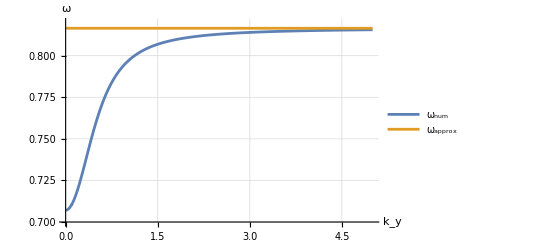

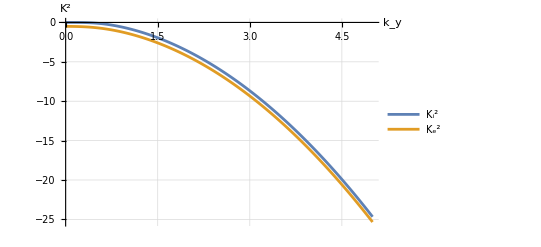

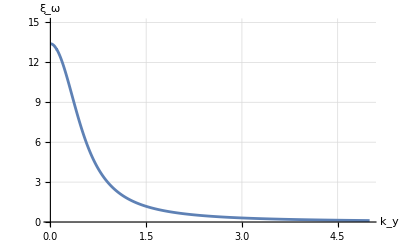

```mathematica
ListLinePlot[{ωNumlist,ωApproxlist},AxesLabel->{"k_y","ω"},PlotLegends->{"ω_num","ω_approx"},PlotRange->{{0,5},{0.7,0.82}},GridLines->Automatic]
ListLinePlot[{Ki2list,Ke2list},AxesLabel->{"k_y","K^2"},PlotLegends->{"K_i^2","K_e^2"},GridLines->Automatic]
ListLinePlot[Errorωlist,AxesLabel->{"k_y","ξ_ω"},PlotRange->{{0,5},{0,15}},GridLines->Automatic]
```

Discuss the results and the applicability of the incompressible approximation.

As for the results, it can be seen that ω_approx is constant with respect to k_y (which is obviously sensible, since the solution ω_approx does not depend on k_y) and ω_num behaves like an exponential function that further approaches  ω_approx as k_y increases until, for k_y>>k_z=1, ω_num≃ω_approx, which coincides with the concepts of the pdf files. Furthermore, the results obtained are valid for the complete regime considered of k_y (0 < k_y < 5) due to K_(i,e)<0 ∀k_y, indicating that the results are indeed surface waves, the focus of this exercise.

Regarding the applicability of the incompressible approximation, given the fact that negligible gas pressure is considered, ω_approx is an extremely satisfactory and appropriate approximation of ω_num for k_y>>k_z=1 (a condition that satisfies the phenomenon known as coronal loops), beginning at k_y≃1.65, where the error between solutions is already < 1 %, coinciding somewhat with the limit of nearly perpendicular propagation. However, if precise computations are needed, for k_y<1.65, the approximation starts to lack accuracy, especially in the k_y≤k_z=1 regime where the error between solutions varies from  2.5 % to 13.4 %. In essence, ω_approx  is an acceptable approximation in this case (depending on the accuracy needed), even if the limit of nearly perpendicular propagation is imposed in a “relaxed” manner, such as k_y≥k_z=1.